# 知識構造化法 (2015年度 秋AB)

Update: 20151022

* : 未完

+ :  新規追加

# :  演習

## 1.知識構造化とは

[実習室]

### 知識構造化法 - 導入-

「知識」も「構造」も明確な定義はなく、「知識構造化」もなんだかよくわからないが、「知識を形式的に構造化」するという立場では、大きく次の二つの考えがある:

(1) 知識を構造化するための形式記述をどのように定義すればよいかという問題、また、そのための概念をどのように定義すればよいかという問題

(2) 単なるデータの寄せ集めから、あるいは既存の知識からどのように新しい知識を創造するかという問題

この授業では、おもに(2)について、Mathematicaを利用しながら「探索的データ解析」を中心に学ぶ。 -> [4.探索的データ解析]

ある程度の理論の解説もありますが、ツールを利用して実践的な解析ができる技術や考えを身につけるための授業です。習熟度に応じLinux上でC言語も使用します。
なんらかのプログラミング経験があることが望ましいですが、初心者に対しても丁寧に指導します。

調査

プログラミング言語の経験

ruby

その他 - C、Python、... Risa/Asir、GAP、SINGULAR、...

出席 -> とらない/とる

期末試験 -> 行なわない/行う

複数回の提出課題(レポート)で評価

授業中の回答で加点

授業方針に対するリクエストは歓迎です。

### 授業概要

データを分析・評価する手法、および、それから知識を創出するための様々な手法について学ぶ。

### 学習・教育目標

図表表示法の特性を説明できる

類似度と距離の概念を説明できる

非階層的および階層的クラスタリングをソフトウエアを用いて行える

### 授業計画

このノートのセクション1-7、および10を完了することを目標とする。

### 知識構造化とは(1)

知識を構造化するための形式記述をどのように定義すればよいかという問題、また、そのための概念をどのように定義すればよいかという問題。

- 情報学基礎の現状と展望. 藤原譲. 情報知識学会誌 Vol.9 No.1 p.13. によれば、情報構造(=知識構造)の表現には以下のような関係や表現を記述できる必要がある。
(1)多重階層性: 親子関係のような階層構造をなす関係
(2)部分重複: 概念の重複を許す
(3)差分記述: 記述を簡素にするために差分を記述できる
(4)入れ子構造: 階層構造とは異なる細分化に対応する構造
(5)多項関係: ハイパーグラフのエッジに対応する関係
(6)記述、表現、分類表示の多様性: 同意語や同義語のような表現の多様性を許す
(7)様相性: modality、つまり程度を扱うことができる、または多値論理を扱うことができる
(8)非可算性: 非可算的な集合を扱える(数学でいう非可算集合より広い意味で捉えているらしい) -> 公理的集合論
(9)相対性、双対性: 実体と関係を均質化できる
(10)動態: 時間や変化の概念を扱うことができる

- 知識構造の表現法の具体例
-- 知識構造の記述 -> RDF、XML、BNF
-- 知識構造のモデル -> E-Rモデル、グラフモデル、FRBR

### 知識構造化とは(2)

単なるデータの寄せ集めから、あるいは既存の知識からどのように新しい知識を創造するかという問題、個人の思考を万人が使える知識とするためのテクニック。
- 知識の抽出: データを構造化・捨象して知識を取り出す
- 知識の表示・表現法: 図やチャートを用いて情報や思考を解りやすく示す
- 知識表現の変換: 表現された知識を別の表現に変換する

知識の抽出の例

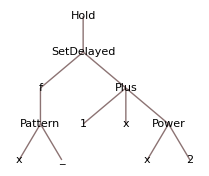
構造の抽出(構造化)
数式 -> ツリー構造化
TreeForm[Hold[f[x_] := 1 + x + x^2]]
-Graphics-

順序の付与(10章)
時系列、値の大きさ
Sort[{1,3,6,2,1}]
{1,1,2,3,6}
Ordering[{1,3,6,2,1}]
{1,5,4,2,3}

クラスの付与(6,7章)
既存のクラスに当てはめる(クラシフィケーション)
領域を分ける(クラスタリング)
FindClusters[{1,2,6,7,8,20}]
{{1,2},{6,7,8,20}}
前述の上位・下位構造の付与は階層クラスの付与とも解釈できる

分類と区分について
- division: 似たものに分けること -> 区分
- taxis: 動物を解体して腑分けすること
- taxon: 生物分類におけるある階級
- clasification: 集めて序列をつけること(カテゴリーあり) -> 分類
- clustering: 集合をいくつかの下位集合に分けること
- clasificationist: 分類体系を考える人
- clasifier: 分類体系に従って分類する人

クラスにおける代表の抽出・付与、性質の抽出(4章)
平均値、分散

知識の表示の例

箇条書き

図(3章)

関係式
f(x) = 1+x+x^2

形式記述(プログラム、アルゴリズム)

知識表現の変換の例

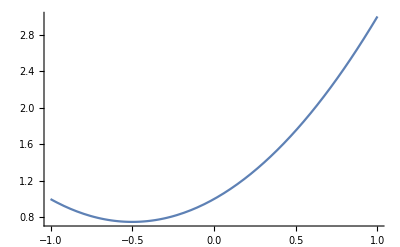
関係式を図にする
Plot[1+x+x^2,{x,-1,1}]
-Graphics-

コンパイルなどによる形式記述変換

### 知識構造化の実装例

まずは、GoogleとWolfram|alphaで検索結果の違いを見てみよう。 - 「G8」、「UN」

Wolfram Alpha

Computational knowledge engine

質問-応答システムに属する(検索システムではない)

構造化された知識ベースを持つ(専門家による知識のキュレーションが行なわれている)

入力は自然言語、数式など

計算機クラスター上でMathematicaを連携させて並列稼働させることにより動作する

エンジンはWolfram言語で記述されている

http://www.wolframalpha.com/

Google

インターネット上の資源を検索する

表示順にランキングを用いる

原則として知識のキュレーションは行わない

Sematitic web

XML

RDF: XMLの拡張として実装されている

トリプル: RDFにおける基礎的な構造: E-Rモデル

### 腕試し

再帰を使ってフィボナッチ数列の第n項を求める関数のプログラムを書く(いきなり第n項を求める式は使わない)。言語はなんでもよい。#

R
解答: fib.r

Mathematica
解答: fib.nb

Ruby
解答: fib.rb

### 提出課題(1)

1. 第1、2、3項を任意に決め、一般項を前3項を参照する式として定義することにより、数列を定義せよ

2. 1の数列の第100項を求めよ

## 1.1 課題の提出について

manabaでレポートとして提出

PDF、フォント埋め込み

学籍番号と氏名を明記

問題を明記

データの出所を明記

結果だけでなくメソッドを明記

期限: 2015/12/xx(これ以降も提出は可能、時間があれば見るが保証はない)

成績は2016/01/xxまでに提出しなければならない

共著可能

4人まで(著者数による分数カウントは行なわない)

提出は個人、提出者を第一著者にすること

複数グループの共著者になることも可能、ただし、第一著者としての提出は各課題につきひとつのみ

共著者以外の協力者は謝辞に入れること

## 1.2 Mathematicaことはじめ#

Mathematicaの言語構造は、一貫してリスト(ツリー)である。リスト構造であれば直接扱うことができる。リストより高次の構造は、予約済み関数がサポートする。

### すべては関数である

Mathematicaは、すべての表現を関数としてとらえる。

#### 関数の頭部

```mathematica
Head[Plus[a,b]]
```

Plus

関数名を表す部分を頭部(Head)という。

#### そして、すべては関数である

関数の形式は、関数名[引数...] である。数値や文字(列)は、引数をとらない特別な関数(名)として解釈できる。

関数定義を引くときは関数名で引く:

```mathematica
??Table[]
```

Information::nomatch: No symbol matching "Table[]" found.

```mathematica
??Table
```

Table[expr,{i_max}] generates a list of i_max copies of expr. 
Table[expr,{i,i_max}] generates a list of the values of expr when i runs from 1 to i_max. 
Table[expr,{i,i_min,i_max}] starts with i=i_min. 
Table[expr,{i,i_min,i_max,di}] uses steps di. 
Table[expr,{i,{i_1,i_2,…}}] uses the successive values i_1, i_2, ….
Table[expr,{i,i_min,i_max},{j,j_min,j_max},…] gives a nested list. The list associated with i is outermost.

Attributes[Table]={HoldAll,Protected}

関数名であってもシンボルとして評価できる:

```mathematica
Table
```

Table

```mathematica
Table Table
```

Table^2

1 は関数か?

```mathematica
1[1]
```

1[1]

```mathematica
1[2]+1[2]
```

2 1[2]

怒られない。

```mathematica
1[x_]:=x^2
```

SetDelayed::write: 1[x_]のタグIntegerはProtectedです．

$Failed

が、プロテクトされている。

つまり、関数表現を禁止しない代わりに、関数に対するユーザー定義を禁止し、特別な関数集合を定義している(ように見せている)。

```mathematica
1[]+1[]
```

2 1[]

```mathematica
1[1]-1[1]
```

0

```mathematica
1[a] 1[a]
```

(1[a])^2

```mathematica
(2[1]-1)^2//Expand
```

1-2 2[1]+(2[1])^2

このように、シンボルや文字列に対しても可能な限り代数的性質を持たせてある:

```mathematica
"y"+"y"
```

2 y

### 厳密解と数値解+

基本は厳密解

```mathematica
9/10
```

9/10

```mathematica
N[9/10]
```

0.9

### 代入+

変数への値の代入:

```mathematica
i=1
```

1

```mathematica
i
```

1

```mathematica
Set[j,2]
```

2

```mathematica
j
```

2

関数定義は”関数名[引数]”のパターンに定義を代入する(正しくはパターンマッチと書き換えを定義している):

```mathematica
f[x_]:=x^2
```

```mathematica
f[4]
```

16

```mathematica
SetDelayed[g[x_],x^3]
```

```mathematica
g[4]
```

64

Nullの代入:

```mathematica
t=Null
```

```mathematica
t
```

```mathematica
{t}
```

{Null}

再帰代入:

```mathematica
s={1,2,s}
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {1, 2, s}.

Hold[{1,2,s}]

```mathematica
s
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {1, 2, s}.

Hold[{1,2,s}]

### 代入の取り消し(定義消去)+

```mathematica
x=0
```

0

```mathematica
x
```

0

```mathematica
Remove[x]
```

```mathematica
x
```

x

```mathematica
f[x_]:=x^3
```

```mathematica
f[4]
```

64

```mathematica
Remove[f]
```

```mathematica
f[4]
```

f[4]

### 式の書き換え(項の置き換え)

書き換えルールの作成:

```mathematica
g->h
```

g→h

```mathematica
Rule[g,h]
```

g→h

ルールを適応して書き換え:

```mathematica
g[g[x]]
```

g[g[x]]

```mathematica
g[g[x]]/.g->h
```

h[h[x]]

```mathematica
ReplaceAll[g[g[x]],g->h]
```

h[h[x]]

```mathematica
f[g[g[x]]]/.g->h
```

f[h[h[x]]]

```mathematica
f[g][g[x]]/.g->h
```

f[h][h[x]]

評価してから置き換え:

```mathematica
{x,x,x}/.{x->Random[]}
```

{0.541974,0.541974,0.541974}

書き換えてから評価:

```mathematica
{x,x,x}/.{x:>Random[]}
```

{0.601004,0.891285,0.411149}

### 純関数

無名関数とも言う。

普通の関数定義:

```mathematica
f[x_,y_]:=x+y
```

純関数の定義:

```mathematica
Function[#1+#2](*定義のみ(再利用不可)、#1は1番目の引数、#2は2番目の引数*)
```

#1+#2&

```mathematica
Function[#1 + #2][1,2](*関数定義に直ちに引数を与えて使う*)
```

3

```mathematica
f=Function[#1 + #2](*定義を関数名に代入*)
```

#1+#2&

```mathematica
f[3,4]
```

7

```mathematica
Function[{x,y},x+y][1, 2](*引数には#でなく任意の名前を付けることができる*)
```

3

```mathematica
Function[Plus[##]][1,2,3]
(*##は引数すべてを参照する*)
```

6

Function[{x, y}, x + y][1, 2]のうちで、Function[{x,y},x+y]部分が頭部すなわち関数名となる。

```mathematica
Head[f[][][]]
```

f[][]

```mathematica
e[1]=Function[#1*#2]
```

#1 #2&

```mathematica
e[2]=Function[(#1*#2)^2]
```

(#1 #2)^2&

```mathematica
e[1][1, 2]
```

2

```mathematica
e[2][1, 2]
```

4

```mathematica
h[3,2]/.{h->Function[#1 #2]}(*一時的にhに関数を割り当てる*)
```

6

```mathematica
h[3,2]
```

h[3,2]

```mathematica
h[][3,2]/.{h[]->Function[#1 #2]}
```

6

```mathematica
h[][3,2]/.{h[]->Function[{x,y},x y]}
```

6

### 引数の参照(Slot[])+

さきほどの純関数の例での#は引数の参照である。#1は1番目、#2は2番目の要素をそれぞれ引数として参照する。

```mathematica
Function[Slot[2]][1,2,3]
```

2

```mathematica
Function[Slot[2]][x,y,z]
```

y

### 繰り返し

単純繰り返しも制御構文でなく関数 -> 処理が遅い 。

```mathematica
For[i=0,i<5,i++,i]
```

```mathematica
i
```

5

```mathematica
s=For[i=0,i<5,i++,i]
```

```mathematica
s
```

```mathematica
{s}
```

{Null}

繰り返しによる配列作成:

```mathematica
Table[i,{i,5}]
```

{1,2,3,4,5}

繰り返しによる配列作成 (多次元):

```mathematica
Table[i+j+k,{i,5},{j,4},{k,3}]
```

{{{3,4,5},{4,5,6},{5,6,7},{6,7,8}},{{4,5,6},{5,6,7},{6,7,8},{7,8,9}},{{5,6,7},{6,7,8},{7,8,9},{8,9,10}},{{6,7,8},{7,8,9},{8,9,10},{9,10,11}},{{7,8,9},{8,9,10},{9,10,11},{10,11,12}}}

繰り返しによる配列作成 (変数):

```mathematica
matc=Array[c,{2,3}]
```

{{c[1,1],c[1,2],c[1,3]},{c[2,1],c[2,2],c[2,3]}}

```mathematica
c[2,2]=5
```

5

```mathematica
matc
```

{{c[1,1],c[1,2],c[1,3]},{c[2,1],5,c[2,3]}}

```mathematica
d[3]=6
```

6

```mathematica
vecd=Array[d,5]
```

{d[1],d[2],6,d[4],d[5]}

関数の繰り返し適応:

```mathematica
Nest[Function[#+1],0,5]
```

5

```mathematica
Nest[#+1&,0,3]
```

3

```mathematica
NestList[Function[#+1],0,5]
```

{0,1,2,3,4,5}

### 条件分岐

条件分岐も制御構文でなく関数 -> 処理が遅い:

```mathematica
i=3
```

3

```mathematica
If[i<5,0,10]
```

0

```mathematica
Timing[Table[If[i<5,0,i],{i,10}]]
```

{0.,{0,0,0,0,5,6,7,8,9,10}}

```mathematica
Timing[Table[If[i<5,0,i],{i,100000}];]
```

{0.003999,Null}

項の置き換えを条件分岐のように使う ->さらに遅くなる:

```mathematica
i/.x_/;x<5->0
```

0

```mathematica
Timing[Table[i/.x_/;x<5->0,{i,10}]]
```

{0.,{0,0,0,0,5,6,7,8,9,10}}

```mathematica
Timing[Table[i/.x_/;x<5->0,{i,100000}];]
```

{0.357946,Null}

### 構造生成、構造処理(変換・変形)、構造テスト、構造アクセス

#### 構造の生成

```mathematica
t1=Table[{i,j},{i,3},{j,4}]
```

{{{1,1},{1,2},{1,3},{1,4}},{{2,1},{2,2},{2,3},{2,4}},{{3,1},{3,2},{3,3},{3,4}}}

```mathematica
Array[{##}&,{3,4}]
```

{{{1,1},{1,2},{1,3},{1,4}},{{2,1},{2,2},{2,3},{2,4}},{{3,1},{3,2},{3,3},{3,4}}}

```mathematica
Array[{##}&,{2,3,4}]
```

{{{{1,1,1},{1,1,2},{1,1,3},{1,1,4}},{{1,2,1},{1,2,2},{1,2,3},{1,2,4}},{{1,3,1},{1,3,2},{1,3,3},{1,3,4}}},{{{2,1,1},{2,1,2},{2,1,3},{2,1,4}},{{2,2,1},{2,2,2},{2,2,3},{2,2,4}},{{2,3,1},{2,3,2},{2,3,3},{2,3,4}}}}

```mathematica
tri= Table[{i,j},{i,5},{j,i}]
```

{{{1,1}},{{2,1},{2,2}},{{3,1},{3,2},{3,3}},{{4,1},{4,2},{4,3},{4,4}},{{5,1},{5,2},{5,3},{5,4},{5,5}}}

```mathematica
tri//TableForm
```

1
1 |  |  |  | 
2
1 | 2
2 |  |  | 
3
1 | 3
2 | 3
3 |  | 
4
1 | 4
2 | 4
3 | 4
4 | 
5
1 | 5
2 | 5
3 | 5
4 | 5
5

#### 構造・表現の変換・変形

Map[]:

```mathematica
t1=Table[{i,j},{i,3},{j,4}]
```

{{{1,1},{1,2},{1,3},{1,4}},{{2,1},{2,2},{2,3},{2,4}},{{3,1},{3,2},{3,3},{3,4}}}

```mathematica
ft1=Map[f[#]&,t1]
```

{f[{{1,1},{1,2},{1,3},{1,4}}],f[{{2,1},{2,2},{2,3},{2,4}}],f[{{3,1},{3,2},{3,3},{3,4}}]}

```mathematica
Flatten[ft1/.f->List,{4}]
```

{{{{1,1,1,1}},{{2,2,2,2}},{{3,3,3,3}}},{{{1,2,3,4}},{{1,2,3,4}},{{1,2,3,4}}}}

```mathematica
Map[g,t1]
```

{g[{{1,1},{1,2},{1,3},{1,4}}],g[{{2,1},{2,2},{2,3},{2,4}}],g[{{3,1},{3,2},{3,3},{3,4}}]}

```mathematica
Map[g,t1,{1}]
```

{g[{{1,1},{1,2},{1,3},{1,4}}],g[{{2,1},{2,2},{2,3},{2,4}}],g[{{3,1},{3,2},{3,3},{3,4}}]}

```mathematica
Map[g,t1,{1}]
```

{g[{{1,1},{1,2},{1,3},{1,4}}],g[{{2,1},{2,2},{2,3},{2,4}}],g[{{3,1},{3,2},{3,3},{3,4}}]}

```mathematica
Map[g,ft1,{1}]//TableForm
```

g[f[{{1,1},{1,2},{1,3},{1,4}}]]
g[f[{{2,1},{2,2},{2,3},{2,4}}]]
g[f[{{3,1},{3,2},{3,3},{3,4}}]]

20151001

答え合わせ: Map[]をすべてのレベルに行う

```mathematica
ft2=Map[f,t1,{0,Infinity}]
```

f[{f[{f[{f[1],f[1]}],f[{f[1],f[2]}],f[{f[1],f[3]}],f[{f[1],f[4]}]}],f[{f[{f[2],f[1]}],f[{f[2],f[2]}],f[{f[2],f[3]}],f[{f[2],f[4]}]}],f[{f[{f[3],f[1]}],f[{f[3],f[2]}],f[{f[3],f[3]}],f[{f[3],f[4]}]}]}]

Apply[]:

```mathematica
Apply[g,ft1,{1}]//TableForm
```

g[{{1,1},{1,2},{1,3},{1,4}}]
g[{{2,1},{2,2},{2,3},{2,4}}]
g[{{3,1},{3,2},{3,3},{3,4}}]

```mathematica
Apply[Function[Slot[2]],List[x,y,z]]
```

y

```mathematica
Apply[Function[Slot[2]],f[x,y,z]]
```

y

ApplyとMapの違い:

```mathematica
Map[f[#]&,{1,2,3}]
```

{f[1],f[2],f[3]}

```mathematica
Map[f[#]&,{1,2,3},{0}]
```

f[{1,2,3}]

```mathematica
Apply[f,{1,2,3}]
```

f[1,2,3]

```mathematica
ReplacePart[{1,2,3},0->f]
```

f[1,2,3]

```mathematica
Apply[Plus,{1,2,3}]
```

6

```mathematica
Plus[{1,2,3}]
```

{1,2,3}

外積:

```mathematica
s1=Outer[f,{1,2,3},{4,5,6}]
```

{{f[1,4],f[1,5],f[1,6]},{f[2,4],f[2,5],f[2,6]},{f[3,4],f[3,5],f[3,6]}}

```mathematica
s2=Outer[g,{1,2,3},{4,5,6},{7,8,9}]
```

{{{g[1,4,7],g[1,4,8],g[1,4,9]},{g[1,5,7],g[1,5,8],g[1,5,9]},{g[1,6,7],g[1,6,8],g[1,6,9]}},{{g[2,4,7],g[2,4,8],g[2,4,9]},{g[2,5,7],g[2,5,8],g[2,5,9]},{g[2,6,7],g[2,6,8],g[2,6,9]}},{{g[3,4,7],g[3,4,8],g[3,4,9]},{g[3,5,7],g[3,5,8],g[3,5,9]},{g[3,6,7],g[3,6,8],g[3,6,9]}}}

```mathematica
o2=Outer[h,s1,s2]
```

{{{{{h[f[1,4],g[1,4,7]],h[f[1,4],g[1,4,8]],h[f[1,4],g[1,4,9]]},{h[f[1,4],g[1,5,7]],h[f[1,4],g[1,5,8]],h[f[1,4],g[1,5,9]]},{h[f[1,4],g[1,6,7]],h[f[1,4],g[1,6,8]],h[f[1,4],g[1,6,9]]}},{{h[f[1,4],g[2,4,7]],h[f[1,4],g[2,4,8]],h[f[1,4],g[2,4,9]]},{h[f[1,4],g[2,5,7]],h[f[1,4],g[2,5,8]],h[f[1,4],g[2,5,9]]},{h[f[1,4],g[2,6,7]],h[f[1,4],g[2,6,8]],h[f[1,4],g[2,6,9]]}},{{h[f[1,4],g[3,4,7]],h[f[1,4],g[3,4,8]],h[f[1,4],g[3,4,9]]},{h[f[1,4],g[3,5,7]],h[f[1,4],g[3,5,8]],h[f[1,4],g[3,5,9]]},{h[f[1,4],g[3,6,7]],h[f[1,4],g[3,6,8]],h[f[1,4],g[3,6,9]]}}},{{{h[f[1,5],g[1,4,7]],h[f[1,5],g[1,4,8]],h[f[1,5],g[1,4,9]]},{h[f[1,5],g[1,5,7]],h[f[1,5],g[1,5,8]],h[f[1,5],g[1,5,9]]},{h[f[1,5],g[1,6,7]],h[f[1,5],g[1,6,8]],h[f[1,5],g[1,6,9]]}},{{h[f[1,5],g[2,4,7]],h[f[1,5],g[2,4,8]],h[f[1,5],g[2,4,9]]},{h[f[1,5],g[2,5,7]],h[f[1,5],g[2,5,8]],h[f[1,5],g[2,5,9]]},{h[f[1,5],g[2,6,7]],h[f[1,5],g[2,6,8]],h[f[1,5],g[2,6,9]]}},{{h[f[1,5],g[3,4,7]],h[f[1,5],g[3,4,8]],h[f[1,5],g[3,4,9]]},{h[f[1,5],g[3,5,7]],h[f[1,5],g[3,5,8]],h[f[1,5],g[3,5,9]]},{h[f[1,5],g[3,6,7]],h[f[1,5],g[3,6,8]],h[f[1,5],g[3,6,9]]}}},{{{h[f[1,6],g[1,4,7]],h[f[1,6],g[1,4,8]],h[f[1,6],g[1,4,9]]},{h[f[1,6],g[1,5,7]],h[f[1,6],g[1,5,8]],h[f[1,6],g[1,5,9]]},{h[f[1,6],g[1,6,7]],h[f[1,6],g[1,6,8]],h[f[1,6],g[1,6,9]]}},{{h[f[1,6],g[2,4,7]],h[f[1,6],g[2,4,8]],h[f[1,6],g[2,4,9]]},{h[f[1,6],g[2,5,7]],h[f[1,6],g[2,5,8]],h[f[1,6],g[2,5,9]]},{h[f[1,6],g[2,6,7]],h[f[1,6],g[2,6,8]],h[f[1,6],g[2,6,9]]}},{{h[f[1,6],g[3,4,7]],h[f[1,6],g[3,4,8]],h[f[1,6],g[3,4,9]]},{h[f[1,6],g[3,5,7]],h[f[1,6],g[3,5,8]],h[f[1,6],g[3,5,9]]},{h[f[1,6],g[3,6,7]],h[f[1,6],g[3,6,8]],h[f[1,6],g[3,6,9]]}}}},{{{{h[f[2,4],g[1,4,7]],h[f[2,4],g[1,4,8]],h[f[2,4],g[1,4,9]]},{h[f[2,4],g[1,5,7]],h[f[2,4],g[1,5,8]],h[f[2,4],g[1,5,9]]},{h[f[2,4],g[1,6,7]],h[f[2,4],g[1,6,8]],h[f[2,4],g[1,6,9]]}},{{h[f[2,4],g[2,4,7]],h[f[2,4],g[2,4,8]],h[f[2,4],g[2,4,9]]},{h[f[2,4],g[2,5,7]],h[f[2,4],g[2,5,8]],h[f[2,4],g[2,5,9]]},{h[f[2,4],g[2,6,7]],h[f[2,4],g[2,6,8]],h[f[2,4],g[2,6,9]]}},{{h[f[2,4],g[3,4,7]],h[f[2,4],g[3,4,8]],h[f[2,4],g[3,4,9]]},{h[f[2,4],g[3,5,7]],h[f[2,4],g[3,5,8]],h[f[2,4],g[3,5,9]]},{h[f[2,4],g[3,6,7]],h[f[2,4],g[3,6,8]],h[f[2,4],g[3,6,9]]}}},{{{h[f[2,5],g[1,4,7]],h[f[2,5],g[1,4,8]],h[f[2,5],g[1,4,9]]},{h[f[2,5],g[1,5,7]],h[f[2,5],g[1,5,8]],h[f[2,5],g[1,5,9]]},{h[f[2,5],g[1,6,7]],h[f[2,5],g[1,6,8]],h[f[2,5],g[1,6,9]]}},{{h[f[2,5],g[2,4,7]],h[f[2,5],g[2,4,8]],h[f[2,5],g[2,4,9]]},{h[f[2,5],g[2,5,7]],h[f[2,5],g[2,5,8]],h[f[2,5],g[2,5,9]]},{h[f[2,5],g[2,6,7]],h[f[2,5],g[2,6,8]],h[f[2,5],g[2,6,9]]}},{{h[f[2,5],g[3,4,7]],h[f[2,5],g[3,4,8]],h[f[2,5],g[3,4,9]]},{h[f[2,5],g[3,5,7]],h[f[2,5],g[3,5,8]],h[f[2,5],g[3,5,9]]},{h[f[2,5],g[3,6,7]],h[f[2,5],g[3,6,8]],h[f[2,5],g[3,6,9]]}}},{{{h[f[2,6],g[1,4,7]],h[f[2,6],g[1,4,8]],h[f[2,6],g[1,4,9]]},{h[f[2,6],g[1,5,7]],h[f[2,6],g[1,5,8]],h[f[2,6],g[1,5,9]]},{h[f[2,6],g[1,6,7]],h[f[2,6],g[1,6,8]],h[f[2,6],g[1,6,9]]}},{{h[f[2,6],g[2,4,7]],h[f[2,6],g[2,4,8]],h[f[2,6],g[2,4,9]]},{h[f[2,6],g[2,5,7]],h[f[2,6],g[2,5,8]],h[f[2,6],g[2,5,9]]},{h[f[2,6],g[2,6,7]],h[f[2,6],g[2,6,8]],h[f[2,6],g[2,6,9]]}},{{h[f[2,6],g[3,4,7]],h[f[2,6],g[3,4,8]],h[f[2,6],g[3,4,9]]},{h[f[2,6],g[3,5,7]],h[f[2,6],g[3,5,8]],h[f[2,6],g[3,5,9]]},{h[f[2,6],g[3,6,7]],h[f[2,6],g[3,6,8]],h[f[2,6],g[3,6,9]]}}}},{{{{h[f[3,4],g[1,4,7]],h[f[3,4],g[1,4,8]],h[f[3,4],g[1,4,9]]},{h[f[3,4],g[1,5,7]],h[f[3,4],g[1,5,8]],h[f[3,4],g[1,5,9]]},{h[f[3,4],g[1,6,7]],h[f[3,4],g[1,6,8]],h[f[3,4],g[1,6,9]]}},{{h[f[3,4],g[2,4,7]],h[f[3,4],g[2,4,8]],h[f[3,4],g[2,4,9]]},{h[f[3,4],g[2,5,7]],h[f[3,4],g[2,5,8]],h[f[3,4],g[2,5,9]]},{h[f[3,4],g[2,6,7]],h[f[3,4],g[2,6,8]],h[f[3,4],g[2,6,9]]}},{{h[f[3,4],g[3,4,7]],h[f[3,4],g[3,4,8]],h[f[3,4],g[3,4,9]]},{h[f[3,4],g[3,5,7]],h[f[3,4],g[3,5,8]],h[f[3,4],g[3,5,9]]},{h[f[3,4],g[3,6,7]],h[f[3,4],g[3,6,8]],h[f[3,4],g[3,6,9]]}}},{{{h[f[3,5],g[1,4,7]],h[f[3,5],g[1,4,8]],h[f[3,5],g[1,4,9]]},{h[f[3,5],g[1,5,7]],h[f[3,5],g[1,5,8]],h[f[3,5],g[1,5,9]]},{h[f[3,5],g[1,6,7]],h[f[3,5],g[1,6,8]],h[f[3,5],g[1,6,9]]}},{{h[f[3,5],g[2,4,7]],h[f[3,5],g[2,4,8]],h[f[3,5],g[2,4,9]]},{h[f[3,5],g[2,5,7]],h[f[3,5],g[2,5,8]],h[f[3,5],g[2,5,9]]},{h[f[3,5],g[2,6,7]],h[f[3,5],g[2,6,8]],h[f[3,5],g[2,6,9]]}},{{h[f[3,5],g[3,4,7]],h[f[3,5],g[3,4,8]],h[f[3,5],g[3,4,9]]},{h[f[3,5],g[3,5,7]],h[f[3,5],g[3,5,8]],h[f[3,5],g[3,5,9]]},{h[f[3,5],g[3,6,7]],h[f[3,5],g[3,6,8]],h[f[3,5],g[3,6,9]]}}},{{{h[f[3,6],g[1,4,7]],h[f[3,6],g[1,4,8]],h[f[3,6],g[1,4,9]]},{h[f[3,6],g[1,5,7]],h[f[3,6],g[1,5,8]],h[f[3,6],g[1,5,9]]},{h[f[3,6],g[1,6,7]],h[f[3,6],g[1,6,8]],h[f[3,6],g[1,6,9]]}},{{h[f[3,6],g[2,4,7]],h[f[3,6],g[2,4,8]],h[f[3,6],g[2,4,9]]},{h[f[3,6],g[2,5,7]],h[f[3,6],g[2,5,8]],h[f[3,6],g[2,5,9]]},{h[f[3,6],g[2,6,7]],h[f[3,6],g[2,6,8]],h[f[3,6],g[2,6,9]]}},{{h[f[3,6],g[3,4,7]],h[f[3,6],g[3,4,8]],h[f[3,6],g[3,4,9]]},{h[f[3,6],g[3,5,7]],h[f[3,6],g[3,5,8]],h[f[3,6],g[3,5,9]]},{h[f[3,6],g[3,6,7]],h[f[3,6],g[3,6,8]],h[f[3,6],g[3,6,9]]}}}}}

```mathematica
Outer[g,{1,2,3},{4,5,6},{7,8,9},{3,2}]
```

{{{{g[1,4,7,3],g[1,4,7,2]},{g[1,4,8,3],g[1,4,8,2]},{g[1,4,9,3],g[1,4,9,2]}},{{g[1,5,7,3],g[1,5,7,2]},{g[1,5,8,3],g[1,5,8,2]},{g[1,5,9,3],g[1,5,9,2]}},{{g[1,6,7,3],g[1,6,7,2]},{g[1,6,8,3],g[1,6,8,2]},{g[1,6,9,3],g[1,6,9,2]}}},{{{g[2,4,7,3],g[2,4,7,2]},{g[2,4,8,3],g[2,4,8,2]},{g[2,4,9,3],g[2,4,9,2]}},{{g[2,5,7,3],g[2,5,7,2]},{g[2,5,8,3],g[2,5,8,2]},{g[2,5,9,3],g[2,5,9,2]}},{{g[2,6,7,3],g[2,6,7,2]},{g[2,6,8,3],g[2,6,8,2]},{g[2,6,9,3],g[2,6,9,2]}}},{{{g[3,4,7,3],g[3,4,7,2]},{g[3,4,8,3],g[3,4,8,2]},{g[3,4,9,3],g[3,4,9,2]}},{{g[3,5,7,3],g[3,5,7,2]},{g[3,5,8,3],g[3,5,8,2]},{g[3,5,9,3],g[3,5,9,2]}},{{g[3,6,7,3],g[3,6,7,2]},{g[3,6,8,3],g[3,6,8,2]},{g[3,6,9,3],g[3,6,9,2]}}}}

内積:

```mathematica
Inner[f,{1,2,3},{4,5,6},g]
```

g[f[1,4],f[2,5],f[3,6]]

```mathematica
Inner[f,{1,2,3},{4,5,6},{7,8,9},g]
```

Inner::intpm: Positive machine-sized integer expected at position 5 in Inner[f, {1, 2, 3}, {4, 5, 6}, {7, 8, 9}, g].

Inner[f,{1,2,3},{4,5,6},{7,8,9},g]

```mathematica
Apply[g,MapThread[f,{{1,2,3},{4,5,6},{7,8,9}}]]
```

g[f[1,4,7],f[2,5,8],f[3,6,9]]

```mathematica
Inner[Times,{1,2,3},{4,5,6},Plus]
```

32

#### 構造のテスト

FullForm[]により「Mathematica式」表現を得る。

```mathematica
FullForm[2+x-x^3]
```

Plus[2,x,Times[-1,Power[x,3]]]

評価を抑制するにはHold[]を使う。

```mathematica
1 + 2*3^2
```

19

```mathematica
FullForm[Hold[1+2*3^2]]
```

Hold[Plus[1,Times[2,Power[3,2]]]]

シンボルを数える。

```mathematica
Count[s2,g,Infinity]
```

0

```mathematica
Count[s2,g,Infinity,Heads->True]
```

27

```mathematica
Count[ft2,f,Infinity,Heads->True]
```

40

Mathematicaの数式をリスト(ツリー)に展開する。

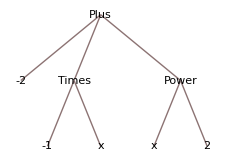

```mathematica
TreeForm[x^2-x-2]
```

Dimensions[]により配列の大きさがわかる。

```mathematica
Dimensions[s1]
```

{3,3}

```mathematica
Dimensions[s2]
```

{3,3,3}

```mathematica
Dimensions[o2]
```

{3,3,3,3,3}

Depth[]はテンソルのランク+1を返す。あるいは、ツリーの深さを返す。

```mathematica
Depth[{{2,1},{3,4}}]
```

3

```mathematica
TensorRank[{{2,1},{3,4}}]
```

2

```mathematica
Depth[o2]
```

8

TensorRank[]も使える。

```mathematica
TensorRank[o2]
```

5

```mathematica
TensorRank[{{2,1},{3,4}}]
```

2

```mathematica
TensorRank[{{2,1,{2}},{3,4,{2}}}]
```

2

```mathematica
Depth[{{2,1,{2}},{3,4,{2}}}]
```

4

```mathematica
FullForm[{{2, 1}, {3, 4}}]
```

List[List[2,1],List[3,4]]

最小構成単位はAtomであり、オブジェクトがAtomであることを判定するにはAtomQ[]を使う。

```mathematica
AtomQ[List[1,2,3]]
```

False

```mathematica
AtomQ[Complex[1,2]]
```

True

```mathematica
AtomQ[Hold[1+2]]
```

False

```mathematica
AtomQ[Hold[2]]
```

False

#### 構造へのアクセス

高次元データへのアクセス:

```mathematica
o2[[1,1,1,1,1,1]]
```

f[1,4]

変数に格納された構造の一部を直接参照して置き換え可能:

```mathematica
o2[[1,1,1,1,1,1]]=10
```

10

```mathematica
o2
```

{{{{{h[10,g[1,4,7]],h[f[1,4],g[1,4,8]],h[f[1,4],g[1,4,9]]},{h[f[1,4],g[1,5,7]],h[f[1,4],g[1,5,8]],h[f[1,4],g[1,5,9]]},{h[f[1,4],g[1,6,7]],h[f[1,4],g[1,6,8]],h[f[1,4],g[1,6,9]]}},{{h[f[1,4],g[2,4,7]],h[f[1,4],g[2,4,8]],h[f[1,4],g[2,4,9]]},{h[f[1,4],g[2,5,7]],h[f[1,4],g[2,5,8]],h[f[1,4],g[2,5,9]]},{h[f[1,4],g[2,6,7]],h[f[1,4],g[2,6,8]],h[f[1,4],g[2,6,9]]}},{{h[f[1,4],g[3,4,7]],h[f[1,4],g[3,4,8]],h[f[1,4],g[3,4,9]]},{h[f[1,4],g[3,5,7]],h[f[1,4],g[3,5,8]],h[f[1,4],g[3,5,9]]},{h[f[1,4],g[3,6,7]],h[f[1,4],g[3,6,8]],h[f[1,4],g[3,6,9]]}}},{{{h[f[1,5],g[1,4,7]],h[f[1,5],g[1,4,8]],h[f[1,5],g[1,4,9]]},{h[f[1,5],g[1,5,7]],h[f[1,5],g[1,5,8]],h[f[1,5],g[1,5,9]]},{h[f[1,5],g[1,6,7]],h[f[1,5],g[1,6,8]],h[f[1,5],g[1,6,9]]}},{{h[f[1,5],g[2,4,7]],h[f[1,5],g[2,4,8]],h[f[1,5],g[2,4,9]]},{h[f[1,5],g[2,5,7]],h[f[1,5],g[2,5,8]],h[f[1,5],g[2,5,9]]},{h[f[1,5],g[2,6,7]],h[f[1,5],g[2,6,8]],h[f[1,5],g[2,6,9]]}},{{h[f[1,5],g[3,4,7]],h[f[1,5],g[3,4,8]],h[f[1,5],g[3,4,9]]},{h[f[1,5],g[3,5,7]],h[f[1,5],g[3,5,8]],h[f[1,5],g[3,5,9]]},{h[f[1,5],g[3,6,7]],h[f[1,5],g[3,6,8]],h[f[1,5],g[3,6,9]]}}},{{{h[f[1,6],g[1,4,7]],h[f[1,6],g[1,4,8]],h[f[1,6],g[1,4,9]]},{h[f[1,6],g[1,5,7]],h[f[1,6],g[1,5,8]],h[f[1,6],g[1,5,9]]},{h[f[1,6],g[1,6,7]],h[f[1,6],g[1,6,8]],h[f[1,6],g[1,6,9]]}},{{h[f[1,6],g[2,4,7]],h[f[1,6],g[2,4,8]],h[f[1,6],g[2,4,9]]},{h[f[1,6],g[2,5,7]],h[f[1,6],g[2,5,8]],h[f[1,6],g[2,5,9]]},{h[f[1,6],g[2,6,7]],h[f[1,6],g[2,6,8]],h[f[1,6],g[2,6,9]]}},{{h[f[1,6],g[3,4,7]],h[f[1,6],g[3,4,8]],h[f[1,6],g[3,4,9]]},{h[f[1,6],g[3,5,7]],h[f[1,6],g[3,5,8]],h[f[1,6],g[3,5,9]]},{h[f[1,6],g[3,6,7]],h[f[1,6],g[3,6,8]],h[f[1,6],g[3,6,9]]}}}},{{{{h[f[2,4],g[1,4,7]],h[f[2,4],g[1,4,8]],h[f[2,4],g[1,4,9]]},{h[f[2,4],g[1,5,7]],h[f[2,4],g[1,5,8]],h[f[2,4],g[1,5,9]]},{h[f[2,4],g[1,6,7]],h[f[2,4],g[1,6,8]],h[f[2,4],g[1,6,9]]}},{{h[f[2,4],g[2,4,7]],h[f[2,4],g[2,4,8]],h[f[2,4],g[2,4,9]]},{h[f[2,4],g[2,5,7]],h[f[2,4],g[2,5,8]],h[f[2,4],g[2,5,9]]},{h[f[2,4],g[2,6,7]],h[f[2,4],g[2,6,8]],h[f[2,4],g[2,6,9]]}},{{h[f[2,4],g[3,4,7]],h[f[2,4],g[3,4,8]],h[f[2,4],g[3,4,9]]},{h[f[2,4],g[3,5,7]],h[f[2,4],g[3,5,8]],h[f[2,4],g[3,5,9]]},{h[f[2,4],g[3,6,7]],h[f[2,4],g[3,6,8]],h[f[2,4],g[3,6,9]]}}},{{{h[f[2,5],g[1,4,7]],h[f[2,5],g[1,4,8]],h[f[2,5],g[1,4,9]]},{h[f[2,5],g[1,5,7]],h[f[2,5],g[1,5,8]],h[f[2,5],g[1,5,9]]},{h[f[2,5],g[1,6,7]],h[f[2,5],g[1,6,8]],h[f[2,5],g[1,6,9]]}},{{h[f[2,5],g[2,4,7]],h[f[2,5],g[2,4,8]],h[f[2,5],g[2,4,9]]},{h[f[2,5],g[2,5,7]],h[f[2,5],g[2,5,8]],h[f[2,5],g[2,5,9]]},{h[f[2,5],g[2,6,7]],h[f[2,5],g[2,6,8]],h[f[2,5],g[2,6,9]]}},{{h[f[2,5],g[3,4,7]],h[f[2,5],g[3,4,8]],h[f[2,5],g[3,4,9]]},{h[f[2,5],g[3,5,7]],h[f[2,5],g[3,5,8]],h[f[2,5],g[3,5,9]]},{h[f[2,5],g[3,6,7]],h[f[2,5],g[3,6,8]],h[f[2,5],g[3,6,9]]}}},{{{h[f[2,6],g[1,4,7]],h[f[2,6],g[1,4,8]],h[f[2,6],g[1,4,9]]},{h[f[2,6],g[1,5,7]],h[f[2,6],g[1,5,8]],h[f[2,6],g[1,5,9]]},{h[f[2,6],g[1,6,7]],h[f[2,6],g[1,6,8]],h[f[2,6],g[1,6,9]]}},{{h[f[2,6],g[2,4,7]],h[f[2,6],g[2,4,8]],h[f[2,6],g[2,4,9]]},{h[f[2,6],g[2,5,7]],h[f[2,6],g[2,5,8]],h[f[2,6],g[2,5,9]]},{h[f[2,6],g[2,6,7]],h[f[2,6],g[2,6,8]],h[f[2,6],g[2,6,9]]}},{{h[f[2,6],g[3,4,7]],h[f[2,6],g[3,4,8]],h[f[2,6],g[3,4,9]]},{h[f[2,6],g[3,5,7]],h[f[2,6],g[3,5,8]],h[f[2,6],g[3,5,9]]},{h[f[2,6],g[3,6,7]],h[f[2,6],g[3,6,8]],h[f[2,6],g[3,6,9]]}}}},{{{{h[f[3,4],g[1,4,7]],h[f[3,4],g[1,4,8]],h[f[3,4],g[1,4,9]]},{h[f[3,4],g[1,5,7]],h[f[3,4],g[1,5,8]],h[f[3,4],g[1,5,9]]},{h[f[3,4],g[1,6,7]],h[f[3,4],g[1,6,8]],h[f[3,4],g[1,6,9]]}},{{h[f[3,4],g[2,4,7]],h[f[3,4],g[2,4,8]],h[f[3,4],g[2,4,9]]},{h[f[3,4],g[2,5,7]],h[f[3,4],g[2,5,8]],h[f[3,4],g[2,5,9]]},{h[f[3,4],g[2,6,7]],h[f[3,4],g[2,6,8]],h[f[3,4],g[2,6,9]]}},{{h[f[3,4],g[3,4,7]],h[f[3,4],g[3,4,8]],h[f[3,4],g[3,4,9]]},{h[f[3,4],g[3,5,7]],h[f[3,4],g[3,5,8]],h[f[3,4],g[3,5,9]]},{h[f[3,4],g[3,6,7]],h[f[3,4],g[3,6,8]],h[f[3,4],g[3,6,9]]}}},{{{h[f[3,5],g[1,4,7]],h[f[3,5],g[1,4,8]],h[f[3,5],g[1,4,9]]},{h[f[3,5],g[1,5,7]],h[f[3,5],g[1,5,8]],h[f[3,5],g[1,5,9]]},{h[f[3,5],g[1,6,7]],h[f[3,5],g[1,6,8]],h[f[3,5],g[1,6,9]]}},{{h[f[3,5],g[2,4,7]],h[f[3,5],g[2,4,8]],h[f[3,5],g[2,4,9]]},{h[f[3,5],g[2,5,7]],h[f[3,5],g[2,5,8]],h[f[3,5],g[2,5,9]]},{h[f[3,5],g[2,6,7]],h[f[3,5],g[2,6,8]],h[f[3,5],g[2,6,9]]}},{{h[f[3,5],g[3,4,7]],h[f[3,5],g[3,4,8]],h[f[3,5],g[3,4,9]]},{h[f[3,5],g[3,5,7]],h[f[3,5],g[3,5,8]],h[f[3,5],g[3,5,9]]},{h[f[3,5],g[3,6,7]],h[f[3,5],g[3,6,8]],h[f[3,5],g[3,6,9]]}}},{{{h[f[3,6],g[1,4,7]],h[f[3,6],g[1,4,8]],h[f[3,6],g[1,4,9]]},{h[f[3,6],g[1,5,7]],h[f[3,6],g[1,5,8]],h[f[3,6],g[1,5,9]]},{h[f[3,6],g[1,6,7]],h[f[3,6],g[1,6,8]],h[f[3,6],g[1,6,9]]}},{{h[f[3,6],g[2,4,7]],h[f[3,6],g[2,4,8]],h[f[3,6],g[2,4,9]]},{h[f[3,6],g[2,5,7]],h[f[3,6],g[2,5,8]],h[f[3,6],g[2,5,9]]},{h[f[3,6],g[2,6,7]],h[f[3,6],g[2,6,8]],h[f[3,6],g[2,6,9]]}},{{h[f[3,6],g[3,4,7]],h[f[3,6],g[3,4,8]],h[f[3,6],g[3,4,9]]},{h[f[3,6],g[3,5,7]],h[f[3,6],g[3,5,8]],h[f[3,6],g[3,5,9]]},{h[f[3,6],g[3,6,7]],h[f[3,6],g[3,6,8]],h[f[3,6],g[3,6,9]]}}}}}

ただし、基本的には関数が引数として受け取った構造に対しての書き換えは禁止されている(コピーされた構造を書き換えたものを返す):

```mathematica
l2={1,2,3}
```

{1,2,3}

```mathematica
ReplacePart[l2,{1}->10]
```

{10,2,3}

```mathematica
l2
```

{1,2,3}

一旦評価してもとの変数に代入:

```mathematica
l2=ReplacePart[l2,{1}->10]
```

{10,2,3}

```mathematica
l2
```

{10,2,3}

### グラフ

```mathematica
g=Graph[{DirectedEdge[1,2],DirectedEdge[2,2],DirectedEdge[2,3]}]
```

-Graphics-

```mathematica
Graph[{1,2,3,4},{DirectedEdge[1,2],DirectedEdge[2,2],DirectedEdge[2,3]}]
```

-Graphics-

```mathematica
a=AdjacencyMatrix[g]
```

SparseArray[<3>, {3, 3}]

```mathematica
Normal[a]
```

{{0,1,0},{0,1,1},{0,0,0}}

```mathematica
AdjacencyGraph[{{0,1,0},{0,1,1},{0,0,0}}]
```

-Graphics-

```mathematica
AdjacencyGraph[a]
```

-Graphics-

### 微分記号 ‘ (ダッシュ)と(偏)微分関数D

```mathematica
FullForm[f']
```

Derivative[1][f]

```mathematica
j[x_]:=x^3
```

```mathematica
j
```

j

```mathematica
j[a]
```

a^3

j' そのものが関数として使える

```mathematica
j'
```

3 #1^2&

```mathematica
j'[a]
```

3 a^2

```mathematica
Derivative[1][j][a]
```

3 a^2

```mathematica
FullForm[j']
```

Function[Times[3,Power[Slot[1],2]]]

Derivativeを使って直接微分する:

```mathematica
Derivative[1][x^3][x] (*jの代わりにx^3では微分しない -> 関数として定義されている必要がある*)
```

(x^3)'[x]

```mathematica
Derivative[1][x^3](*x^3 という関数名として認識される*)
```

(x^3)'

```mathematica
Function[u, u^3][x]
```

x^3

```mathematica
Derivative[1][Function[u,u^3]][x](*そこで、純関数を使う*)
```

3 x^2

```mathematica
Derivative[1][Function[u,j[u]]][x]
```

3 x^2

Dを使って直接微分する

```mathematica
D[x^3,x]
```

3 x^2

### 積分

不定積分

```mathematica
Integrate[x-x^3,x]
```

x^2/2-x^4/4

定積分

```mathematica
Integrate[x-x^3,{x,0,3}]
```

-63/4

特殊関数の積分

```mathematica
Integrate[DiracDelta[x],{x,1,3}]
```

0

```mathematica
Integrate[DiracDelta[x],{x,-Infinity,Infinity}]
```

1

```mathematica
Integrate[DiracDelta[x],{x,0,Infinity}]
```

1-HeavisideTheta[0]

```mathematica
Integrate[DiracDelta[x],{x,-Infinity,0}]
```

1-HeavisideTheta[0]

```mathematica
Integrate[Zeta[x],{x,1.5,2.5}]
```

∫_1.5^2.5 Zeta[x]ⅆx

```mathematica
NIntegrate[Zeta[x],{x,1.5,2.5}]
```

1.7431

```mathematica
Integrate[Zeta[x],{x,1.5,2.5}]//N
```

1.7431

```mathematica
4//Head
```

Integer

```mathematica
Head[4]
```

Integer

```mathematica
4//N//Head
```

Real

### 集合

listを集合として扱う場合、そのための関数を使う。

```mathematica
a={1,1,2,3}
```

{1,1,2,3}

```mathematica
b={1,1,5}
```

{1,1,5}

```mathematica
Union[a]
```

{1,2,3}

```mathematica
Intersection[a,b]
```

{1}

### 局所変数

```mathematica
h[x_]:=Module[{a},
a=2;
x^a
]
```

```mathematica
h[5]
```

25

```mathematica
a
```

a

### フィボナッチ数列ふたたび

前回の授業中課題の解答

```mathematica
fib[n_]:=If[n==1,1,If[n==2,1,fib[n-1]+fib[n-2]]]
```

```mathematica
fib[6]
```

8

Mathematicaでは、特定の引数をとる場合の関数に、直接値を代入できる。

```mathematica
fi[0]:=0
fi[1]:=1
fi[n_]:=fi[n-1]+fi[n-2]
```

```mathematica
fi[10]
```

55

以下は階乗の例。

```mathematica
fa[0]:=1
fa[n_]:=n fa[n-1]
```

```mathematica
fa[0]
```

1

```mathematica
fa[6]
```

720

```mathematica
0!
```

1

```mathematica
6!
```

720

### グラフィクス

Graphics[]関数によりグラフィクスオブジェクトを配置して表示できる。

すべてのオブジェクトがグラフィクスとして解釈されるわけでなく、Graphicsとして表示できるものはグラフィクスプリミティブのみ。

```mathematica
Remove[a]
```

```mathematica
Graphics[a]
```

-Graphics-

```mathematica
Graphics[1]
```

-Graphics-

```mathematica
Graphics[Text[a]]
```

-Graphics-

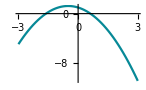

```mathematica
g=Plot[1-x-x^2,{x,-3,3}]
```

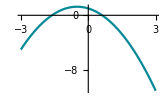

```mathematica
Graphics[g]
```

```mathematica
Head[g]
```

Graphics

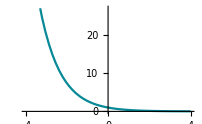

```mathematica
h=Plot[E^(-x),{x,-4,4}]
```

```mathematica
Graphics[{h,g}]
```

-Graphics-

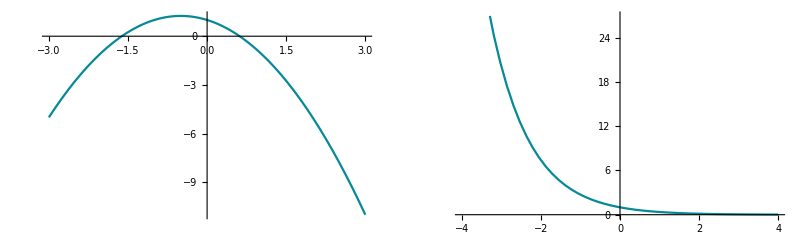

```mathematica
GraphicsGrid[{{g,h}}]
```

```mathematica
g3=Plot3D[Sin[x y], {x, 0, 3}, {y, 0, 3}, ColorFunction -> "Rainbow"]
```

-Graphics3D-

```mathematica
Slider[]
```

```mathematica
Head[Slider[]]
```

Slider

```mathematica
Dynamic[{"a->"<>ToString[a],"b->"<>ToString[b]}]
```

```mathematica
{Slider[Dynamic[a],{0,1}],Dynamic[a]}
```

{,}

```mathematica
Grid[{{Slider[Dynamic[b],{1,5}]},{Dynamic[Plot[Sin[b x],{x,-4,4}]]}}]
```

```mathematica
Manipulate[Plot[Sin[x(1+a x)],{x,0,6}],{a,0,2}]
```

```mathematica
Manipulate[Plot[Sin[x^b(1+a x)],{x,0,6}],{a,0,2},{b,0,2}]
```

### 式コピーのテクニック -- マルチプルクリック

```mathematica
Remove[f1,f2,f3,f4,y]
```

```mathematica
f1[f2[f3[f4[x]]]]
```

f1[f2[f3[f4[x]]]]

```mathematica
f1[f2[f3[f4[x,y]]]]
```

f1[f2[f3[f4[x,y]]]]

### Mathematicaの式・データ構造まとめ

Mathematicaの場合、式はリストであり、頭部の情報にデータ型を含む。データ型とは端的にはHead[]によって返されるオブジェクト(名)である。

#### 関数と関数名(頭部)

```mathematica
Head[a]
```

Symbol

```mathematica
Head[6]
```

Integer

```mathematica
Head[6.]
```

Real

```mathematica
Head[1-I]
```

Complex

```mathematica
Head["AAA"]
```

String

```mathematica
Head[fib]
```

Symbol

Headをネストさせて作用させると最終的にSymbolが得られる

```mathematica
Head[f[][][]]
```

f[][]

```mathematica
Head[f[][][]]//Head
```

f[]

```mathematica
Head[f[][][]]//Head//Head
```

f

```mathematica
Head[f[][][]]//Head//Head//Head
```

Symbol

```mathematica
Head[f[][][]]//Head//Head//Head//Head
```

Symbol

```mathematica
Head[6]//Head
```

Symbol

#### リストとツリー

Mathematicaのリストはツリー構造をなす。

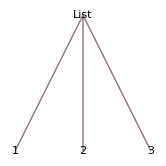

```mathematica
TreeForm[{1,2,3}]
```

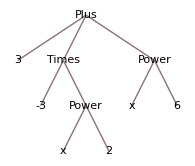

```mathematica
TreeForm[x^6-3x^2+3]
```

#### グラフ(及び高次構造)

リストでグラフは直接表現できないので、 Graph[]という予約済み関数を使う。

```mathematica
??Graph
```

RowBox[{"Graph", "[", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["e", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["e", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], "]"}] 辺 SubscriptBox[StyleBox["e", "TI"], StyleBox["j", "TI"]]のグラフを与える．
RowBox[{"Graph", "[", RowBox[{RowBox[{StyleBox["{", "TI"], RowBox[{StyleBox[SubscriptBox[StyleBox["v", "TI"], StyleBox["1", "TR"]], "TI"], ",", StyleBox[SubscriptBox[StyleBox["v", "TI"], StyleBox["2", "TR"]], "TI"], ",", StyleBox["…", "TR"]}], StyleBox["}", "TI"]}], ",", RowBox[{StyleBox["{", "TI"], RowBox[{SubscriptBox[StyleBox["e", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["e", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], StyleBox["}", "TI"]}]}], "]"}] 頂点 SubscriptBox[StyleBox["v", "TI"], StyleBox["i", "TI"]]，辺 SubscriptBox[StyleBox["e", "TI"], StyleBox["j", "TI"]]のグラフを与える．
RowBox[{"Graph", "[", RowBox[{RowBox[{"{", RowBox[{StyleBox["…", "TR"], ",", RowBox[{SubscriptBox[StyleBox["w", "TI"], StyleBox["i", "TI"]], "[", RowBox[{SubscriptBox[StyleBox["v", "TI"], StyleBox["i", "TI"]], ",", StyleBox["…", "TR"]}], "]"}], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["…", "TR"], ",", RowBox[{SubscriptBox[StyleBox["w", "TI"], StyleBox["j", "TI"]], "[", RowBox[{SubscriptBox[StyleBox["e", "TI"], StyleBox["j", "TI"]], ",", StyleBox["…", "TR"]}], "]"}], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] 頂点と辺の特性が記号ラッパー SubscriptBox[StyleBox["w", "TI"], StyleBox["k", "TI"]]で定義されているグラフを与える．

Attributes[Graph]={NHoldAll,Protected}
 
Options[Graph]={AlignmentPoint→Center,AspectRatio→Automatic,Axes→False,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ContentSelectable→Automatic,DirectedEdges→Automatic,EdgeCapacity→Automatic,EdgeCost→Automatic,EdgeLabels→Automatic,EdgeLabelStyle→Automatic,EdgeShapeFunction→Automatic,EdgeStyle→Automatic,EdgeWeight→Automatic,Editable→False,Epilog→{},Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→None,FrameTicksStyle→{},GraphHighlight→{},GraphHighlightStyle→Automatic,GraphLayout→Automatic,GraphRoot→Automatic,GraphStyle→Automatic,GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,LabelStyle→{},PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotRange→All,PlotRangeClipping→False,PlotRangePadding→Automatic,PlotRegion→Automatic,Prolog→{},Properties→{},RotateLabel→True,Ticks→Automatic,TicksStyle→{},VertexCapacity→Automatic,VertexCoordinates→Automatic,VertexLabels→Automatic,VertexLabelStyle→Automatic,VertexShape→Automatic,VertexShapeFunction→Automatic,VertexSize→Automatic,VertexStyle→Automatic,VertexWeight→Automatic}

実際に AtomQ[] ではTrueを返す。

```mathematica
AtomQ[Graph[{UndirectedEdge[1,2]}]]
```

True

#### 配列

Mathematicaにおいて、配列はリストの入れ子と変わりない。

1次元配列:

```mathematica
Table[x,{x,5}]
```

{1,2,3,4,5}

2次元配列:

```mathematica
Table[{x,y},{x,5},{y,5}]
```

{{{1,1},{1,2},{1,3},{1,4},{1,5}},{{2,1},{2,2},{2,3},{2,4},{2,5}},{{3,1},{3,2},{3,3},{3,4},{3,5}},{{4,1},{4,2},{4,3},{4,4},{4,5}},{{5,1},{5,2},{5,3},{5,4},{5,5}}}

3次元配列:

```mathematica
d3=Table[{x,y,z},{x,5},{y,5},{z,5}]
```

{{{{1,1,1},{1,1,2},{1,1,3},{1,1,4},{1,1,5}},{{1,2,1},{1,2,2},{1,2,3},{1,2,4},{1,2,5}},{{1,3,1},{1,3,2},{1,3,3},{1,3,4},{1,3,5}},{{1,4,1},{1,4,2},{1,4,3},{1,4,4},{1,4,5}},{{1,5,1},{1,5,2},{1,5,3},{1,5,4},{1,5,5}}},{{{2,1,1},{2,1,2},{2,1,3},{2,1,4},{2,1,5}},{{2,2,1},{2,2,2},{2,2,3},{2,2,4},{2,2,5}},{{2,3,1},{2,3,2},{2,3,3},{2,3,4},{2,3,5}},{{2,4,1},{2,4,2},{2,4,3},{2,4,4},{2,4,5}},{{2,5,1},{2,5,2},{2,5,3},{2,5,4},{2,5,5}}},{{{3,1,1},{3,1,2},{3,1,3},{3,1,4},{3,1,5}},{{3,2,1},{3,2,2},{3,2,3},{3,2,4},{3,2,5}},{{3,3,1},{3,3,2},{3,3,3},{3,3,4},{3,3,5}},{{3,4,1},{3,4,2},{3,4,3},{3,4,4},{3,4,5}},{{3,5,1},{3,5,2},{3,5,3},{3,5,4},{3,5,5}}},{{{4,1,1},{4,1,2},{4,1,3},{4,1,4},{4,1,5}},{{4,2,1},{4,2,2},{4,2,3},{4,2,4},{4,2,5}},{{4,3,1},{4,3,2},{4,3,3},{4,3,4},{4,3,5}},{{4,4,1},{4,4,2},{4,4,3},{4,4,4},{4,4,5}},{{4,5,1},{4,5,2},{4,5,3},{4,5,4},{4,5,5}}},{{{5,1,1},{5,1,2},{5,1,3},{5,1,4},{5,1,5}},{{5,2,1},{5,2,2},{5,2,3},{5,2,4},{5,2,5}},{{5,3,1},{5,3,2},{5,3,3},{5,3,4},{5,3,5}},{{5,4,1},{5,4,2},{5,4,3},{5,4,4},{5,4,5}},{{5,5,1},{5,5,2},{5,5,3},{5,5,4},{5,5,5}}}}

```mathematica
AtomQ[d3]
```

False

#### 構造体

Mathematicaに構造体はない。かわりにリストを入れ子(ツリー)にして表現する。

```mathematica
x={1,2,2,{1,2,{1}}}
```

{1,2,2,{1,2,{1}}}

```mathematica
x
```

{1,2,2,{1,2,{1}}}

#### ポインタ

Mathematicaでのポインタは単に変数となる。

従って、変数に対し再帰定義もできる。

```mathematica
y=.
y={1,2,y}
```

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

Hold[{1,2,y}]

ちゃんと、yには再帰構造が定義されている。

```mathematica
y
```

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

Hold[{1,2,y}]

```mathematica
y=5
y={1,2,y}
```

5

```mathematica
y
```

{1,2,5}

#### ベクトルとマトリクスの積の処理

```mathematica
Array[k,{3,3}]//TableForm
```

k[1,1] | k[1,2] | k[1,3]
k[2,1] | k[2,2] | k[2,3]
k[3,1] | k[3,2] | k[3,3]

```mathematica
Array[j,3].Array[k,{3,3}] (*[j]を横ベクトルとして扱っている*)
```

{k[1,1]+8 k[2,1]+27 k[3,1],k[1,2]+8 k[2,2]+27 k[3,2],k[1,3]+8 k[2,3]+27 k[3,3]}

```mathematica
Array[k,{3,3}].Array[j,3](*[j]を縦ベクトルとして扱っている*)
```

{k[1,1]+8 k[1,2]+27 k[1,3],k[2,1]+8 k[2,2]+27 k[2,3],k[3,1]+8 k[3,2]+27 k[3,3]}

### link集

自習に役に立つリンク

https://www.kri.sfc.keio.ac.jp/report/gakujutsu/2006/3-5/Part1/Part1.html

http://wwwmain.h.kobe-u.ac.jp/~nagasaka/mma/

http://blog.hulinks.co.jp/2010/04/nyuumon-mathematica.html

## 2.計算機とデータ構造について

[実習室]

われわれは膨大な知識を処理するために計算機に頼る。したがって知識は計算機にとっても利用可能でなくてはならないことを前提とする。

計算機にとってすべてはデータである。

### データとは

処理系が扱える表現全てがデータである。

ちなみに: 演算装置内の処理を考えるとき、「instruction」と「data」に分けて考える。ここでの「data」は別の概念と捉えたほうがよいであろう。

#### データ型

ほとんどすべての処理系やプログラミング言語では、データ型が定義されている。

型の例:

- 整数(Integer)

- 浮動小数(Real)

- 複素数(Complex)

- ブール代数

- 文字

- ポインタ

上位構造(おもにユーザーが定義する):

- 配列

-- ベクトル

-- 行列

-- テンソル

-- 文字列

- 構造体

- 列挙型

- リスト(連結セル)

#### データ構造

- 計算機から見ればデータ型の組み合わせ。

- 利用者から見ればいわゆるデータフォーマット。

### 処理系とは

一般的には、OSおよびその上で動作するアプリケーションを指す。

### データ処理とは

データ処理とは、処理対象と処理命令の定義が記述された表現を、その表現以外の知識(ルール)を用い、表現が変化しなくなるまで評価を続けることである(べつの言葉で言えば、表現評価系を用いた表現の変換)。処理対象と処理命令は、分離が曖昧であり広い意味ではすべて処理対象である。計算とほとんど同義と考えてよい。

「計算機」と「データ」の概念はチューリングマシンのそれとおなじである。「人間からの割り込みを許すチューリングマシン」としての実装が「計算機」である。

「計算機」と「データ」の実体すなわち実装は機械的および電磁気的な現象の操作・制御であり、「計算機」はとくにこれを効率的に行なうことが要求される。

#### データ処理の抽象化 -> チューリングマシン

チューリングマシンとは
アラン・チューリングによる仮想機械とそのしくみ。計算機を抽象化したもの。

チューリングマシンの部品

機械(マシン)

マシンの状態を保持するメモリ

テープの状態を読み取るヘッド

無限に長いテープ

チューリングマシンの形式的要素

M: 機械の状態を表す有限集合

T: テープに記載される記号の有限集合

b: Tの元である空白記号

Σ: b以外のTの部分集合

δ: 遷移関数: δ(m,t)=(m’,t’,h): 機械の状態がm、テープの着目位置の記号がtのとき、機械の状態をm’に、テープの着目位置の記号をt’に変更したあと、テープの着目位置をh側に一つ移動。
ただし、

m: Mの元

t: Tの元

h: 次のステップでテープ上をどちらに動くか: {L,R}

mi: 初期状態(mi∈M)

ma: 受理状態(ma∈M)

黒板で説明 <- 手書きメモ

Mathemticaのチューリングマシン関数

```mathematica
??TuringMachine
```

RowBox[{"TuringMachine", "[", RowBox[{StyleBox["rule", "TI"], ",", StyleBox["init", "TI"], ",", StyleBox["t", "TI"]}], "]"}] 指定されたルールで初期条件 StyleBox["init", "TI"] から StyleBox["t", "TI"] ステップ進んだチューリングマシンの進化を表すリストを生成する． 
RowBox[{"TuringMachine", "[", RowBox[{StyleBox["rule", "TI"], ",", StyleBox["init", "TI"]}], "]"}] StyleBox["init", "TI"] を1ステップ進化させた結果を与える．

Attributes[TuringMachine]={Protected,ReadProtected}

s色-k色チューリングマシンのすべての状態:

```mathematica
turingCurrentState[s_,k_]:=Module[
{sets,setk,current},
sets=Range[0,s-1];
setk=Range[0,k-1];
current=Flatten[Outer[List,sets,setk],1]
]
```

上記状態に対応するルールすべて:

```mathematica
turingAllRules[s_,k_]:=Module[
{(*numrule,*)numStateSet,numOperateSet,sets,setk,(*current,*)selections,next},
(*numrule=(2 s k)^(s k);*)
numStateSet=s k;
numOperateSet=2 s k;
sets=Range[0,s-1];
setk=Range[0,k-1];
selections=Tuples[Range[numOperateSet],numStateSet];
next=Flatten[Outer[List,sets,setk,{"L","R"}],2];
Map[next[[#]]&,selections]
]
```

２色ヘッド-２色テープの場合の組み合わせ

```mathematica
turingCurrentState[2,2]
```

{{0,0},{0,1},{1,0},{1,1}}

２色ヘッド-２色テープの場合の組み合わせそれぞれに対して、{0/1,0/1,L/R}の8通りのルールを作ることができる。

第2506ルール

```mathematica
turingAllRules[2,2]//Length
```

4096

```mathematica
IntegerDigits[4095,2,12]
```

{1,1,1,1,1,1,1,1,1,1,1,1}

出力の読み方:
 {{<ヘッドの状態>,<”テープの状態表示”における先頭要素に対するヘッドの位置>,<初期状態からのヘッドの移動>},{<テープの状態表示>}}

```mathematica
TuringMachine[2506,{1,{{},0}},0]
```

{{{1,1,0},{0}}}

```mathematica
TuringMachine[2506,{1,{{},0}},2]//MatrixForm
```

({1,1,0} | {0,0}
{2,2,1} | {1,0}
{1,1,0} | {1,1})

```mathematica
TuringMachine[2506,{1,{{},0}},3]//MatrixForm
```

((1
2
0) | (0
0
0)
(2
3
1) | (0
1
0)
(1
2
0) | (0
1
1)
(2
1
-1) | (0
0
1))

ルールを切り替えながらturingmachineを継続するプログラム

```mathematica
turingNext[state_,rl_/;Depth[rl]==2]:=TuringMachine[rl[[1]],state[[-1]],rl[[2]]]
```

```mathematica
turingSequence[init_,rls_]:=Module[{seed,first},
seed=FoldList[turingNext,{init},rls];
first=seed[[1,1]];
Prepend[Apply[Join,Map[Drop[#,1]&,Drop[seed,1]]],first] ]
```

```mathematica
init={{1,1,0},{0}}
```

{{1,1,0},{0}}

```mathematica
turingSequence[init,{{2506,2},{2506,1}}]
```

{{{1,1,0},{0}},{{2,1,1},{1}},{{1,1,2},{0}},{{2,1,3},{1}}}

```mathematica
TuringMachine[2506,TuringMachine[2506,init,0][[-1]],3]
```

{{{1,1,0},{0}},{{2,1,1},{1}},{{1,1,2},{0}},{{2,1,3},{1}}}

```mathematica
TuringMachine[2506,init,3]
```

{{{1,1,0},{0}},{{2,1,1},{1}},{{1,1,2},{0}},{{2,1,3},{1}}}

#### データ処理の具体化 -> 物理的な機械(計算機)による動作

データ処理(計算)を行うことは、物理的には何らかの物理状態を(自動的かつ連続的に)変化させることである。

電子計算機においてはCPU内のレジスタの状態を変化させることに相当し、広い意味では記憶装置や表示装置を含む計算機の動作を指す。

CPU内のALUにより計算(演算)された結果は、一時的にレジスタに保持され、その結果はメインメモリにコピーされる。

#### セルオートマトン(参考)

黒板で説明 <- 手書きメモ

一方、局所規則のみで自己組織的に駆動する構造がセルオートマトンである。一部の規則群がチューリング完全である。つまり、適切な規則を定義することによりチューリングマシンとして機能する。

1近傍d次元における第nルールを得る(<-Mathematicaの第nルールと合致しているかは未確認)

```mathematica
numRuleToCellList[n_,d_]:=(* n: 第nルール、d: d次元 *)
Module[{dig,stats,box,bbox,cellstat},
dig=3^d;
stats=2^dig;
bbox=Reverse[Map[IntegerDigits[#,2,dig]&,Range[0,stats-1]]];
cellstat=IntegerDigits[n,2,stats];
Transpose[{bbox,cellstat}]
]
```

```mathematica
numRuleToCellList[1,1]
```

{{{1,1,1},0},{{1,1,0},0},{{1,0,1},0},{{1,0,0},0},{{0,1,1},0},{{0,1,0},0},{{0,0,1},0},{{0,0,0},1}}

1次元のルールを表で示す

```mathematica
cellListVis1D[rule_]:=Grid[{Map[Grid[{#[[1]],{Null,#[[2]],Null}},Frame->All]&,rule]}]
```

1近傍、1次元、第0ルール

```mathematica
cellListVis1D[numRuleToCellList[0,1]]
```

1 | 1 | 1
 | 0 |  | 1 | 1 | 0
 | 0 |  | 1 | 0 | 1
 | 0 |  | 1 | 0 | 0
 | 0 |  | 0 | 1 | 1
 | 0 |  | 0 | 1 | 0
 | 0 |  | 0 | 0 | 1
 | 0 |  | 0 | 0 | 0
 | 0 |

```mathematica
??CellularAutomaton
```

RowBox[{"CellularAutomaton", "[", RowBox[{StyleBox["rule", "TI"], ",", StyleBox["init", "TI"], ",", StyleBox["t", "TI"]}], "]"}] 指定した条件でセルオートマトンを初期条件 StyleBox["init", "TI"] から StyleBox["t", "TI"] ステップ実行した進化を表すリストを生成する．
RowBox[{"CellularAutomaton", "[", RowBox[{StyleBox["rule", "TI"], ",", StyleBox["init", "TI"]}], "]"}] 1ステップ分の StyleBox["init", "TI"] の進化の結果を返す．
RowBox[{"CellularAutomaton", "[", RowBox[{StyleBox["rule", "TI"], ",", StyleBox["init", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["tspec", "TI"], ",", StyleBox["xspec", "TI"], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] StyleBox["tspec", "TI"]，StyleBox[RowBox[{"xspec", " "}], "TI"]等で指定された進化の部分だけを返す．
RowBox[{"CellularAutomaton", "[", RowBox[{StyleBox["rule", "TI"], ",", StyleBox["init", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["t", "TI"], ",", "All", ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] StyleBox["t", "TI"] ステップの間に影響を受けるであろうすべてのセルを各ステップに含む．

Attributes[CellularAutomaton]={Protected}

{0,0,0,1,0,0,0}に対してルール30を3ステップ実行する

```mathematica
CellularAutomaton[30,{0,0,0,1,0,0,0},2]
```

{{0,0,0,1,0,0,0},{0,0,1,1,1,0,0},{0,1,1,0,0,1,0}}

可視化する

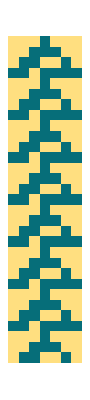

```mathematica
CellularAutomaton[30,{0,0,0,1,0,0,0},30]//ArrayPlot
```

「背景」0を無限にならべて、{1}を初期値としてルール25を50ステップ実行する

```mathematica
CellularAutomaton[25, {{1}, 0}, 50]//ArrayPlot
```

-Graphics-

#### ラムダ計算(今期やらない)

### プログラミング言語とは

(利用者が)データ処理をしやすくするための仕組みであり、広義には、人間が計算機へ指示(とくにバッチ処理)を伝えるための言語であるが、これではさまざまな仕組みがプログラミング言語になってしまう。

そこで、狭義には以下のように考えるのが適当。

コンパイラ(インタープリタ)に動作を解釈させるための言語である。

効率的にデータ処理を行うためにコンパイラ(インタープリタ)に必要とされる機能 :

抽象化(変数)
 ポインタもアドレスを格納する変数に過ぎない。

繰り返し(または再帰)
再帰表現と繰り返し表現は可換であるが、双方備えるべき。

条件分岐

### 知識(データ)の伝達と獲得

計算機 <-> 外界(人間含む)

計算機 <-> 計算機

#### いままでは、計算機上にすでにある情報(データ)を扱う話。では、外の世界の情報を計算機で扱うには? (計算機が外界の情報を手に入れる手段は?)

センサーを使う(センサーと接続可能な場合)。または、解析器付きセンサーが出力するデータを読み込む。

Linuxにおけるマウスの例
 /dev/input/mouse1

MacではControllerInformation[]が使える

```mathematica
ControllerInformation[]
```

オシロスコープの例(演習)(20151022) : 
4人までのグループをつくり、グループごとにデータを取得。他のグループはMathematicaの自習(Import[]やGet[]などの入出力について)。すべてのグループがデータを取り終わったら、終了。

#### 計算機が他の計算機に知識を伝える手段は?

ネットワーク

P2P

## 3.図表表示法

[実習室]

可視化、捨象などのテクニック。データをその特性にもとづき、適切に表現する。

### データの特性 -尺度水準-

定性値

名義尺度
値は、命名、分類のために用いられる。
数え上げ
集合 ?

順序尺度
値は、序列、順序を示す。
数えること + 序列に関する統計的扱い
位相 ?

定量値

間隔尺度
間隔に意味があるが、原点がない。
数えること + 序列に関する統計的扱い + 足し算引き算
加算に対して閉じている系(群ともちょっと違う) ?

比率尺度
原点からの距離を表す。
数えること + 序列に関する統計的扱い + 足し算引き算 + 掛け算割り算
環・体 ?

例題 : 書誌情報にはどのようなものがある? それらの尺度水準は?

20151008

### データの図表化

データの組織化と可視化
図表の中にどのように値やシンボルやアイコンを配置するか

カテゴリー

アルファベット

時間

距離

...

#### 配列系: 要素の値を表示

数表: 個体と属性の組み合わせに対して、属性値を付与する

例: G8のGDP

```mathematica
TableForm[Map[{#}&,CountryData["G8","GDP"]],TableHeadings->{CountryData["G8"],{"GDP"}}]
```

| GDP
Canada | 1.5022×10^12
France | 2.85653×10^12
Germany | 3.64947×10^12
Italy | 2.30306×10^12
Japan | 4.91069×10^12
United Kingdom | 2.66627×10^12
United States | 1.40967×10^13

配列表: 属性値の組に対して、個体を決定する
例: 周期表、時間割表

相関表: 個体の組に対して、その関係を付与する
例: 分散共分散(5章)、隣接行列

#### 座標系: 要素を位置づける

属性の数が1: おもにチャートと呼ばれる: 帯グラフ、円グラフ

属性の数が2: おもにプロットと呼ばれる: 棒グラフ、折れ線グラフ(リストプロット)
例:

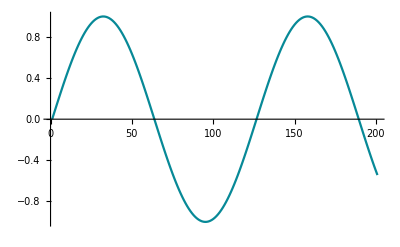

```mathematica
ListPlot[Table[Sin[t],{t,0,10,0.05}],Joined->True]
```

属性の数が多: 特殊グラフ: レーダーチャート、顔型グラフ

#### 連結系: 要素間の様々な関係

要素間の関係を視覚的に連結

時系列
例: 年表、系統樹、PERT

詳細化
例: 関連樹木(アルゴリズムなし)、決定木(アルゴリズム)

手続き
例: フローチャート

関係
例: グラフ(V,E)、配線図、引用関係図

#### 領域系: 要素の論理関係を領域として表す

特に要素間の論理関係を表す

区分
例: 地図、クラスタリング

詳細化
例: シソーラス

論理関係
例: ベン図

### 作図

#### 配列系:数表:

各国の保有商船数の上位5ヵ国#

キーワード: CountryData[]

```mathematica
(*TableForm[(worldShips=Sort[Cases[Map[{#,CountryData[#,"MerchantShips"]}&,CountryData[]],{_String,_Integer}],#1[[2]]>#2[[2]]&])[[{1,2,3,4,5}]],TableHeadings->{None,{"Country","Ships"}}]*)(*ver.9*)
```

```mathematica
TableForm[(worldShips=Sort[Cases[Map[{#,CountryData[#,"MerchantShips"]}&,Map[#[[2]]&,CountryData[]]],{_String,_Integer}],#1[[2]]>#2[[2]]&])[[{1,2,3,4,5}]],TableHeadings->{None,{"Country","Ships"}}](*ver.10*)
```

Country | Ships
Panama | 6323
Liberia | 2204
China | 1826
Malta | 1438
Singapore | 1292

#### 配列系:数表: [ヒストグラム、パレートプロット]

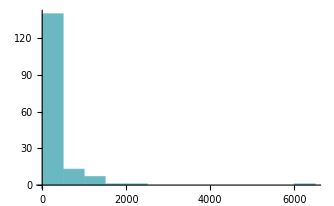

```mathematica
Histogram[Map[#[[2]]&,worldShips]]
```

```mathematica
<< StatisticalPlots`
```

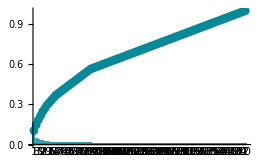

```mathematica
ParetoPlot[Map[#[[2]]&,worldShips]]
```

#### 配列系:配列表: [周期表]

族と周期の値を使って周期表を表示するスクリプト#

ElementData[]をつかう。

```mathematica
ElementData[8]
```

oxygen

```mathematica
ElementData[8,"Abbreviation"]
```

O

```mathematica
ElementData[8,"Group"] (*族が数値として返ってくる*)
```

16

```mathematica
ElementData[8,"Period"] (*周期が数値として返ってくる*)
```

2

```mathematica
{ElementData[8, "Group"], -ElementData[8, "Period"]} (*周期表における座標としてデータを取り出す*)
```

{16,-2}

```mathematica
Graphics[Table[Text[ElementData[n,"Abbreviation"],{ElementData[n,"Group"],-ElementData[n,"Period"]}],{n,118}]]
```

-Graphics-

20151022

遷移元素を除いて表示:

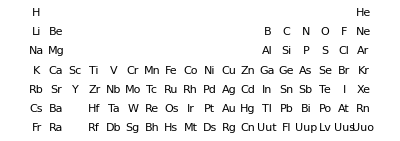

```mathematica
Graphics[Table[Text[ElementData[n,"Abbreviation"],{ElementData[n,"Group"],-ElementData[n,"Period"]}],{n,Flatten[{Range[1,56],Range[72,88],Range[104,118]}]}]]
```

不適格パターンを除いて表示:

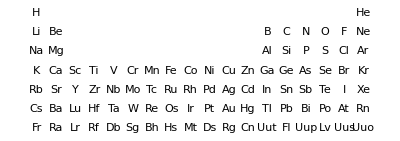

```mathematica
Graphics[Cases[Table[Text[ElementData[n,"Abbreviation"],{ElementData[n,"Group"],-ElementData[n,"Period"]}],{n,118}],Text[_String,{_Integer,_Integer}]]]
```

#### 配列系:相関表: [隣接行列]

```mathematica
l=Range[8];
```

```mathematica
e={{1,2},{3,4},{3,5},{1,7},{1,6}}
```

{{1,2},{3,4},{3,5},{1,7},{1,6}}

```mathematica
Apply[UndirectedEdge,e,2]
```

{1<->2,3<->4,3<->5,1<->7,1<->6}

```mathematica
g=Graph[l,Apply[UndirectedEdge,e,2]]
```

-Graphics-

```mathematica
AdjacencyMatrix[g]//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 1 | 1 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

#### 座標系:棒グラフ: [ヒストグラム] - 既出

#### 座標系:折れ線グラフ:

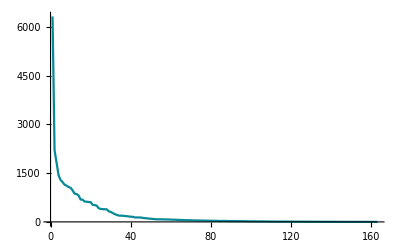

```mathematica
ListPlot[Map[#[[2]]&,worldShips],Joined->True,PlotRange->All]
```

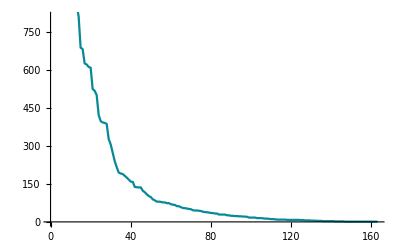

```mathematica
ListPlot[Map[#[[2]]&,worldShips],Joined->True]
```

#### 座標系:円グラフ

```mathematica
PieChart[Map[#[[2]]&,worldShips]]
```

-Graphics-

```mathematica
PieChart[Map[#[[2]]&,worldShips],ChartStyle->"Rainbow"]
```

-Graphics-

```mathematica
PieChart[{{1,2,3},{2,2,1}},ChartLabels->{"a","b","c"}]
```

-Graphics-

#### 座標系: [ベクトルプロット]

固有値、固有ベクトルの可視化

固有値、固有ベクトルとは:
 A: 行列、x: ベクトル、λ: スカラーのとき、行列Aに対して、A.x = λ.x となる非ゼロのλ、xが求まる。
これは、行列Aによるベクトルの変換において、変換により単にλ倍されるベクトルが存在することを示す。
そのときのλを固有値、ベクトルを固有ベクトルという。

単位円上のポイントがどのように変換されるのかを可視化#

```mathematica
a[0] = {{2, 1}, {1, 3}}
```

{{2,1},{1,3}}

```mathematica
(clist = Table[{Cos[th], Sin[th]}, {th, Pi/12, 2 Pi, Pi/12}]) // Length
```

24

```mathematica
aDotclist = Map[a[0].# &, clist];
```

```mathematica
g1 = Graphics[{Map[Arrow[#] &, Transpose[{clist, aDotclist}]], Map[Arrow[{{0, 0}, #}] &, clist]}];
```

```mathematica
a["eigen"] = Eigensystem[a[0]]
```

{{1/2 (5+√5),1/2 (5-√5)},{{1/2 (-1+√5),1},{1/2 (-1-√5),1}}}

```mathematica
v = a["eigen"][[1]]*Map[Normalize[#] &, a["eigen"][[2]]];
```

```mathematica
g3 = Graphics[{Red, Map[Arrow[{{0, 0}, #}] &, v]}];
```

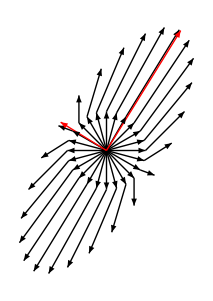

```mathematica
Show[g1, g3]
```

20151029

コードの説明:

行列Aを次のように仮定する

```mathematica
a[0] = {{2, 1}, {1, 3}}
```

{{2,1},{1,3}}

原点から単位円上へのベクトルを24個生成

```mathematica
(clist = Table[{Cos[th], Sin[th]}, {th, Pi/12, 2 Pi, Pi/12}]) // Length
```

24

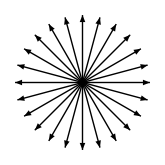

```mathematica
Graphics[Map[Arrow[{{0, 0}, #}] &, clist]]
```

24個のベクトルを行列A (a[0]) によって変換

```mathematica
aDotclist = Map[a[0].# &, clist];
```

「変換前のベクトル」と「そのベクトルの終点を始点とした変換後のベクトル」のグラフィクスオブジェクト(矢印表現)を生成

```mathematica
g1 = Graphics[{Map[Arrow[#] &, Transpose[{clist, aDotclist}]], Map[Arrow[{{0, 0}, #}] &, clist]}];
```

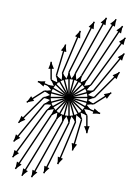

```mathematica
Graphics[g1]
```

行列A (a[0]) の固有値、固有ベクトルを求める

```mathematica
a["eigen"] = Eigensystem[a[0]]
```

{{1/2 (5+√5),1/2 (5-√5)},{{1/2 (-1+√5),1},{1/2 (-1-√5),1}}}

固有値*固有ベクトル(ノルム:1にノーマライズ)、つまり、本来ならばλ.x を求めている

```mathematica
v = a["eigen"][[1]]*Map[Normalize[#] &, a["eigen"][[2]]];
```

ベクトル λ.x をグラフィクスオブジェクト(矢印表現:赤)として保存

```mathematica
g3 = Graphics[{Red, Map[Arrow[{{0, 0}, #}] &, v]}];
```

すべてのをグラフィクスオブジェクトを表示

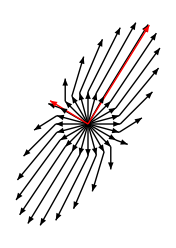

```mathematica
Show[g1, g3]
```

格子状にベクトル(座標)を発生(tbl)

```mathematica
tbl=Flatten[Table[{x,y},{x,-4,4},{y,-4,4}],1];
```

tblのa[0]による変換

```mathematica
v2=Map[a[0].#&,tbl];
```

tblの第一固有値による変換

```mathematica
v3=a["eigen"][[1,1]] tbl;
```

tblのa[0]による変換ベクトルのプロット

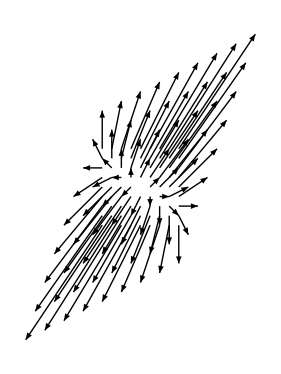

```mathematica
Graphics[ar2=MapThread[Arrow[{#1,#2}]&,{tbl,v2}]]
```

tblの第一固有値による変換によるプロット

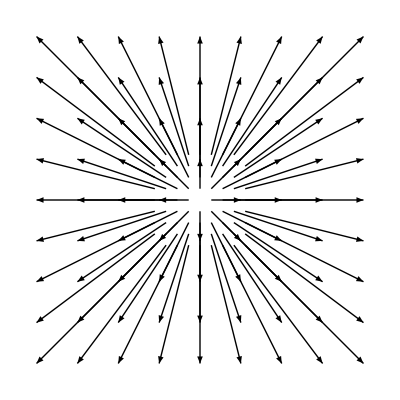

```mathematica
Graphics[ar3=MapThread[Arrow[{#1,#2}]&,{tbl,v3}]]
```

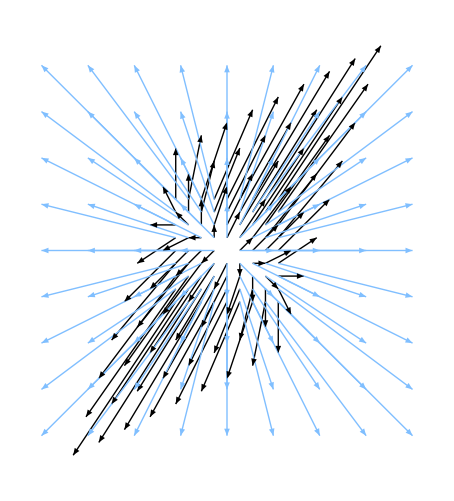

```mathematica
Graphics[{ar2,RGBColor[{0.5,0.75,1}],ar3}]
```

ベクトル {x,y} のベクトルプロット

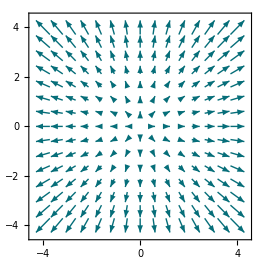

```mathematica
VectorPlot[{x, y}, {x, -4, 4}, {y, -4, 4}]
```

ベクトル {x,y} の行列 {{1,0,},{0,1}} による変換(変化無し)

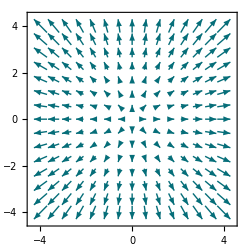

```mathematica
n=VectorPlot[{{1,0},{0,1}}.{x, y}, {x, -4, 4}, {y, -4, 4}]
```

ベクトル {x,y} の行列 a[0] による変換

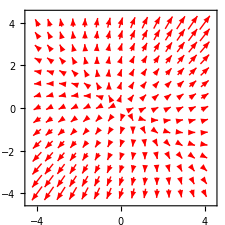

```mathematica
e=VectorPlot[a[0].{x, y}, {x, -4, 4}, {y, -4, 4},VectorStyle->Red]
```

ベクトル {x,y} の行列 a[0] の固有値による変換

プロットの重ね合わせ。

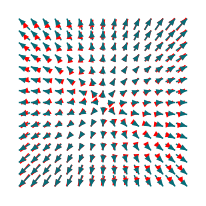

```mathematica
Graphics[{e[[1]],n[[1]]}]
```

それぞれのベクトル系列のスケールが調整される(むしろ、問題):

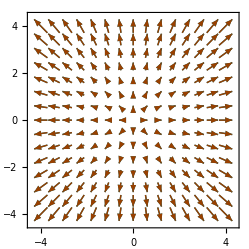

```mathematica
r=VectorPlot[{10{x, y},{x,y}}, {x, -4, 4}, {y, -4, 4}]
```

#### 座標系: [コンタープロット]

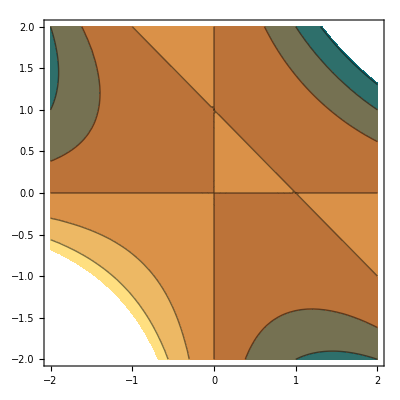

```mathematica
ContourPlot[x y (1-x-y),{x,-2,2},{y,-2,2}]
```

#### 座標系: [3Dプロット]

```mathematica
Plot3D[x y (1-x-y),{x,-2,2},{y,-2,2}]
```

-Graphics3D-

#### 連結系:グラフ: [数式の木構造]

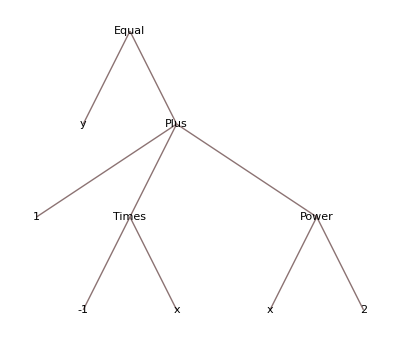

```mathematica
x=.
TreeForm[y==1-x+x^2]
```

#### 連結系:グラフ: [化学式]

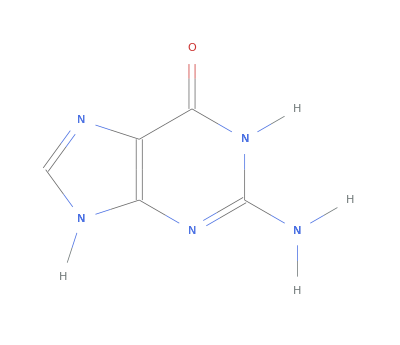

```mathematica
ChemicalData["Guanine"]
```

#### 連結系:グラフ: [崩壊図]

```mathematica
is = Select[IsotopeData[], 
   100 <= IsotopeData[#, "MassNumber"] <= 102 &];
```

```mathematica
isdata=
Map[Table[IsotopeData[#,pr],{pr,{"Symbol","DaughterNuclides"}}]&,is]
```

{{^100Kr,{rubidium-100}},{^100Rb,{strontium-100,strontium-99,strontium-98}},{^101Rb,{strontium-101,strontium-100}},{^102Rb,{strontium-102,strontium-101}},{^100Sr,{yttrium-100,yttrium-99}},{^101Sr,{yttrium-101,yttrium-100}},{^102Sr,{yttrium-102,yttrium-101}},{^100Y,{zirconium-100,zirconium-99}},{^101Y,{zirconium-101,zirconium-100}},{^102Y,{zirconium-102,zirconium-101}},{^100Zr,{niobium-100}},{^101Zr,{niobium-101}},{^102Zr,{niobium-102}},{^100Nb,{molybdenum-100}},{^101Nb,{molybdenum-101}},{^102Nb,{molybdenum-102}},{^100Mo,{ruthenium-100}},{^101Mo,{technetium-101}},{^102Mo,{technetium-102}},{^100Tc,{ruthenium-100,molybdenum-100}},{^101Tc,{ruthenium-101}},{^102Tc,{ruthenium-102}},{^100Ru,{}},{^101Ru,{}},{^102Ru,{}},{^100Rh,{ruthenium-100}},{^101Rh,{ruthenium-101}},{^102Rh,{ruthenium-102,palladium-102}},{^100Pd,{rhodium-100}},{^101Pd,{rhodium-101}},{^102Pd,{ruthenium-102}},{^100Ag,{palladium-100}},{^101Ag,{palladium-101}},{^102Ag,{palladium-102}},{^100Cd,{silver-100}},{^101Cd,{silver-101}},{^102Cd,{silver-102}},{^100In,{cadmium-100,silver-99}},{^101In,{cadmium-101,silver-100}},{^102In,{cadmium-102,silver-101}},{^100Sn,{indium-100,cadmium-99}},{^101Sn,{indium-101,cadmium-100}},{^102Sn,{indium-102,cadmium-101}}}

```mathematica
isr=Flatten[Map[Outer[List, {#[[1]]}, #[[2]]] &, isdata],2]
```

{{^100Kr,rubidium-100},{^100Rb,strontium-100},{^100Rb,strontium-99},{^100Rb,strontium-98},{^101Rb,strontium-101},{^101Rb,strontium-100},{^102Rb,strontium-102},{^102Rb,strontium-101},{^100Sr,yttrium-100},{^100Sr,yttrium-99},{^101Sr,yttrium-101},{^101Sr,yttrium-100},{^102Sr,yttrium-102},{^102Sr,yttrium-101},{^100Y,zirconium-100},{^100Y,zirconium-99},{^101Y,zirconium-101},{^101Y,zirconium-100},{^102Y,zirconium-102},{^102Y,zirconium-101},{^100Zr,niobium-100},{^101Zr,niobium-101},{^102Zr,niobium-102},{^100Nb,molybdenum-100},{^101Nb,molybdenum-101},{^102Nb,molybdenum-102},{^100Mo,ruthenium-100},{^101Mo,technetium-101},{^102Mo,technetium-102},{^100Tc,ruthenium-100},{^100Tc,molybdenum-100},{^101Tc,ruthenium-101},{^102Tc,ruthenium-102},{^100Rh,ruthenium-100},{^101Rh,ruthenium-101},{^102Rh,ruthenium-102},{^102Rh,palladium-102},{^100Pd,rhodium-100},{^101Pd,rhodium-101},{^102Pd,ruthenium-102},{^100Ag,palladium-100},{^101Ag,palladium-101},{^102Ag,palladium-102},{^100Cd,silver-100},{^101Cd,silver-101},{^102Cd,silver-102},{^100In,cadmium-100},{^100In,silver-99},{^101In,cadmium-101},{^101In,silver-100},{^102In,cadmium-102},{^102In,silver-101},{^100Sn,indium-100},{^100Sn,cadmium-99},{^101Sn,indium-101},{^101Sn,cadmium-100},{^102Sn,indium-102},{^102Sn,cadmium-101}}

```mathematica
isrl=Map[Rule[#[[1]],IsotopeData[#[[2]],"Symbol"]]&,isr]
```

{^100Kr→^100Rb,^100Rb→^100Sr,^100Rb→^99Sr,^100Rb→^98Sr,^101Rb→^101Sr,^101Rb→^100Sr,^102Rb→^102Sr,^102Rb→^101Sr,^100Sr→^100Y,^100Sr→^99Y,^101Sr→^101Y,^101Sr→^100Y,^102Sr→^102Y,^102Sr→^101Y,^100Y→^100Zr,^100Y→^99Zr,^101Y→^101Zr,^101Y→^100Zr,^102Y→^102Zr,^102Y→^101Zr,^100Zr→^100Nb,^101Zr→^101Nb,^102Zr→^102Nb,^100Nb→^100Mo,^101Nb→^101Mo,^102Nb→^102Mo,^100Mo→^100Ru,^101Mo→^101Tc,^102Mo→^102Tc,^100Tc→^100Ru,^100Tc→^100Mo,^101Tc→^101Ru,^102Tc→^102Ru,^100Rh→^100Ru,^101Rh→^101Ru,^102Rh→^102Ru,^102Rh→^102Pd,^100Pd→^100Rh,^101Pd→^101Rh,^102Pd→^102Ru,^100Ag→^100Pd,^101Ag→^101Pd,^102Ag→^102Pd,^100Cd→^100Ag,^101Cd→^101Ag,^102Cd→^102Ag,^100In→^100Cd,^100In→^99Ag,^101In→^101Cd,^101In→^100Ag,^102In→^102Cd,^102In→^101Ag,^100Sn→^100In,^100Sn→^99Cd,^101Sn→^101In,^101Sn→^100Cd,^102Sn→^102In,^102Sn→^101Cd}

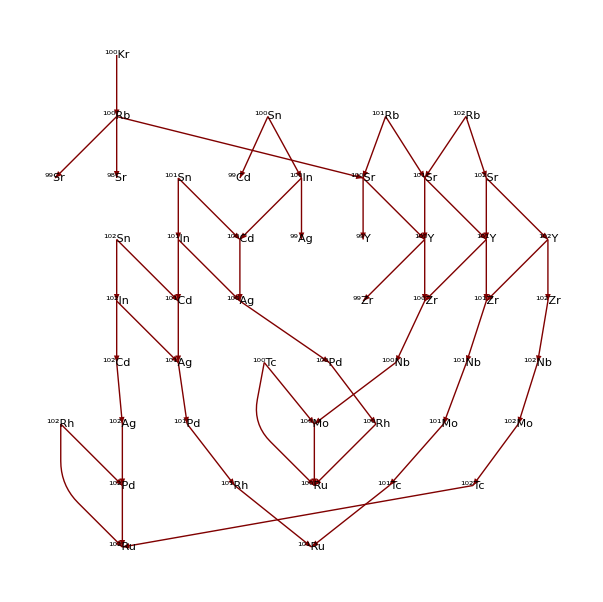

```mathematica
LayeredGraphPlot[
isrl, 
 DirectedEdges -> True, VertexLabeling -> True]
```

#### 領域系:地図: [世界地図]

いいかげんな世界地図(より正確な座標も持っている)

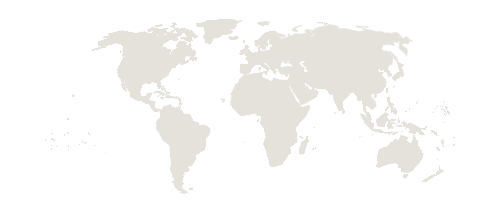

```mathematica
CountryData["World","Shape"]
```

```mathematica
coordsToXYZ[list_] := 
  Transpose[{Cos[#[[1]]]*Cos[#[[2]]], Cos[#[[1]]]*Sin[#[[2]]], 
      Sin[#[[1]]]} &@Reverse@Transpose[list*Pi/180.]];
```

```mathematica
coord3DWorld=Map[coordsToXYZ[#]&,CountryData["World","Shape"][[1]][[3]][[1]],{1}];
```

```mathematica
Graphics3D[Polygon[coord3DWorld]]
```

-Graphics3D-

#### 領域系: [ボロノイ図]

(*ver. 10 のみ*)

```mathematica
pts = RandomReal[{-1, 1}, {15, 2}]
```

{{0.774616,0.353904},{0.952953,-0.189202},{0.986992,-0.476655},{-0.83943,0.742248},{0.140579,0.418741},{0.0995463,0.592721},{0.167306,-0.140154},{-0.931496,0.514677},{0.922455,0.012253},{-0.551136,0.405318},{0.0910991,0.542896},{0.293913,0.846786},{0.145683,-0.152189},{-0.414443,0.180347},{0.0477817,-0.234918}}

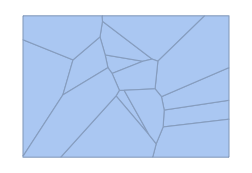

```mathematica
vg=VoronoiMesh[pts]
```

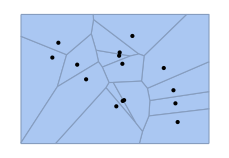

```mathematica
Show[vg,Graphics[Point[pts]]]
```

### 作図におけるチェックポイント

何を見せたいか

詳細 <-> 捨象(傾向)

どの部分を見せたいか

作図範囲

表示の順序

時系列

理論的構成

表示形式

バリアフリー

直感的なアイコン

制限があるときにどうするか

解像度

色

メディアの特徴を活かす

Web

論文(紙媒体)

論文での基本

表のタイトルは表の上

図のタイトルは図の下

チェックポイントやルールが明示してある例

「図表は英語で作るよう提言が出されています．」, ( 参照2014-10-23 http://www.jspp.org/toyama/sanka.html)

「「色盲の人にもわかるバリアフリープレゼンテーション法」のサイトhttp://www.nig.ac.jp/color/もご参照ください．」, ( 参照2014-10-23 http://www.jspp.org/toyama/sanka.html)

### 解析法と表示法は表裏一体(補間・スムージング・フィルタリング)

#### 補間

```mathematica
??ListInterpolation
```

ListInterpolation[array] 与えられた値の配列を補間する近似関数を表すInterpolatingFunctionオブジェクトを作成する．
ListInterpolation[array,{{x_min,x_max},{y_min,y_max},…}] array  の各値の座標を決めるグリッド域を指定する．

Attributes[ListInterpolation]={Protected}
 
Options[ListInterpolation]={InterpolationOrder→3,Method→Automatic,PeriodicInterpolation→False}

```mathematica
f=ListInterpolation[{1,4.1,9.2,15,26}]
```

InterpolatingFunction[{{1., 5.}}, <>]

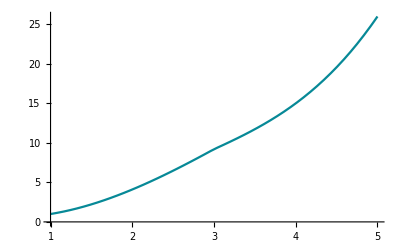

```mathematica
Plot[f[x],{x,1,5}]
```

InterpolatingFunction::dmval: 入力値{0.000122571}は補間関数のデータ範囲外です．外挿が使用されます．

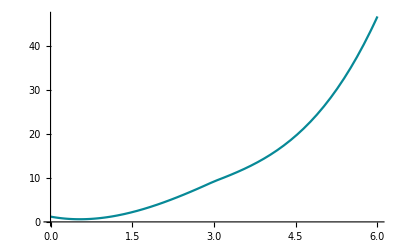

```mathematica
Plot[f[x],{x,0,6}]
```

#### 畳み込み

(f * g)(t) = ∫f(x)g(t-x)dx

see also: 内積 : f^Tg = ∫f(x)g(x)dx

```mathematica
??Convolve
```

RowBox[{"Convolve", "[", RowBox[{StyleBox["f", "TI"], ",", StyleBox["g", "TI"], ",", StyleBox["x", "TI"], ",", StyleBox["y", "TI"]}], "]"}] 式 StyleBox["f", "TI"]と StyleBox["g", "TI"] の StyleBox["x", "TI"] についてのたたみ込みを返す．
RowBox[{"Convolve", "[", RowBox[{StyleBox["f", "TI"], ",", StyleBox["g", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["y", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] 多次元たたみ込みを返す．

Attributes[Convolve]={Protected,ReadProtected}

たたみ込みは一般に関数を滑らかにする：

```mathematica
Remove[f0,f0,t0,t1,t2,t3]
```

Remove::remal: シンボルf0はすでに消去されました．

```mathematica
f0=UnitBox[t0]; (*もとの関数*)
```

```mathematica
f1=Convolve[f0,f0,t0,t1] (*一回畳み込み*)
```

UnitTriangle[t1]

```mathematica
f2=Convolve[f1,f1,t1,t2] (*2回畳み込み*)
```

Piecewise[{{1/6 (4-6 t2^2-3 t2^3), -1<t2<0}, {1/3 (2+3 t2-t2^3), t2==0}, {1/6 (-6 t2-6 t2^2-t2^3), t2==-1}, {1/6 (8-12 t2+6 t2^2-t2^3), 1<t2<2}, {1/6 (6 t2-6 t2^2+t2^3), t2==1}, {1/6 (8+12 t2+6 t2^2+t2^3), -2<t2<-1}, {1/6 (4-6 t2^2+3 t2^3), 0<t2<1}, {0, True}}]

```mathematica
f3=Convolve[f2,f2,t2,t3]; (*3回畳み込み*)
```

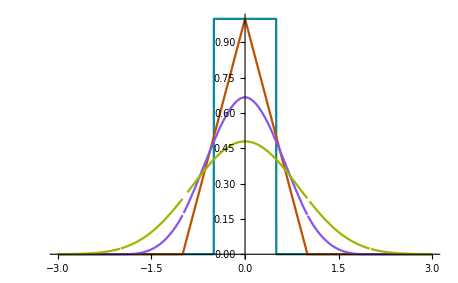

```mathematica
Plot[Evaluate[{f0,f1,f2,f3}/.{t0->x,t1->x,t2->x,t3->x}],{x,-3,3}]
```

```mathematica
Integrate[(f0/.t0->x),{x,-Infinity,Infinity}]
```

1

```mathematica
Integrate[(f1/.t1->x),{x,-Infinity,Infinity}]
```

1

```mathematica
Integrate[(f2/.t2->x),{x,-Infinity,Infinity}]
```

1

```mathematica
Integrate[(f3/.t3->x),{x,-Infinity,Infinity}]
```

1

```mathematica
??ListConvolve
```

RowBox[{"ListConvolve", "[", RowBox[{StyleBox["ker", "TI"], ",", StyleBox["list", "TI"]}], "]"}] 核 StyleBox[RowBox[{"ker", " "}], "TI"]と StyleBox["list", "TI"] のたたみ込みを形成する．
RowBox[{"ListConvolve", "[", RowBox[{StyleBox["ker", "TI"], ",", StyleBox["list", "TI"], ",", StyleBox["k", "TI"]}], "]"}] StyleBox["ker", "TI"] の StyleBox["k", "TI"] 次の要素がStyleBox["list", "TI"] の各要素と揃えられる循環たたみ込みを形成する．
RowBox[{"ListConvolve", "[", RowBox[{StyleBox["ker", "TI"], ",", StyleBox["list", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["k", "TI"], StyleBox["L", "TI"]], ",", SubscriptBox[StyleBox["k", "TI"], StyleBox["R", "TI"]]}], "}"}]}], "]"}] 最初の要素が RowBox[{RowBox[{StyleBox["list", "TI"], "[", RowBox[{"[", "1", "]"}], "]"}], " ", RowBox[{StyleBox["ker", "TI"], "[", RowBox[{"[", SubscriptBox[StyleBox["k", "TI"], StyleBox["L", "TI"]], "]"}], "]"}]}]を含み，最後の要素が RowBox[{RowBox[{StyleBox["list", "TI"], "[", RowBox[{"[", RowBox[{"-", "1"}], "]"}], "]"}], " ", RowBox[{StyleBox["ker", "TI"], "[", RowBox[{"[", SubscriptBox[StyleBox["k", "TI"], StyleBox["R", "TI"]], "]"}], "]"}]}]を含む循環たたみ込みを形成する．
RowBox[{"ListConvolve", "[", RowBox[{StyleBox["ker", "TI"], ",", StyleBox["list", "TI"], ",", StyleBox["klist", "TI"], ",", StyleBox["p", "TI"]}], "]"}] StyleBox["list", "TI"] の最後が要素 StyleBox[RowBox[{"p", " "}], "TI"]の反復で充填されるような，たたみ込みを形成する．
RowBox[{"ListConvolve", "[", RowBox[{StyleBox["ker", "TI"], ",", StyleBox["list", "TI"], ",", StyleBox["klist", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["p", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["p", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] StyleBox["list", "TI"] の最後が SubscriptBox[StyleBox["p", "TI"], StyleBox["i", "TI"]] で循環反復充填されるたたみ込みを形成する．
RowBox[{"ListConvolve", "[", RowBox[{StyleBox["ker", "TI"], ",", StyleBox["list", "TI"], ",", StyleBox["klist", "TI"], ",", StyleBox["padding", "TI"], ",", StyleBox["g", "TI"], ",", StyleBox["h", "TI"]}], "]"}] StyleBox["g", "TI"] がTimesの代りに，StyleBox["h", "TI"] がPlusの代りに使われる一般化されたたたみ込みを形成する．
RowBox[{"ListConvolve", "[", RowBox[{StyleBox["ker", "TI"], ",", StyleBox["list", "TI"], ",", StyleBox["klist", "TI"], ",", StyleBox["padding", "TI"], ",", StyleBox["g", "TI"], ",", StyleBox["h", "TI"], ",", StyleBox["lev", "TI"]}], "]"}] StyleBox["ker", "TI"] と StyleBox["list", "TI"] でレベル StyleBox["lev", "TI"] の要素を使い，たたみ込みを形成する．

Attributes[ListConvolve]={Protected}

```mathematica
ListConvolve[{x,y},{a,b,c,d,e,f}]
```

{b x+a y,c x+b y,d x+c y,e x+d y,f x+e y}

自分自身のリスト畳み込み:

```mathematica
Array[a, 10]
```

{a[1],a[2],a[3],a[4],a[5],a[6],a[7],a[8],a[9],a[10]}

を、window幅3で畳み込み。

```mathematica
Partition[Array[a,10],3,1]
```

{{a[1],a[2],a[3]},{a[2],a[3],a[4]},{a[3],a[4],a[5]},{a[4],a[5],a[6]},{a[5],a[6],a[7]},{a[6],a[7],a[8]},{a[7],a[8],a[9]},{a[8],a[9],a[10]}}

```mathematica
Map[Reverse[#] &, Partition[Array[a, 10], 3, 1], {1}]
```

{{a[3],a[2],a[1]},{a[4],a[3],a[2]},{a[5],a[4],a[3]},{a[6],a[5],a[4]},{a[7],a[6],a[5]},{a[8],a[7],a[6]},{a[9],a[8],a[7]},{a[10],a[9],a[8]}}

```mathematica
Partition[Array[a,10],3,1]*Map[Reverse[#] &, Partition[Array[a, 10], 3, 1], {1}]
```

{{a[1] a[3],a[2]^2,a[1] a[3]},{a[2] a[4],a[3]^2,a[2] a[4]},{a[3] a[5],a[4]^2,a[3] a[5]},{a[4] a[6],a[5]^2,a[4] a[6]},{a[5] a[7],a[6]^2,a[5] a[7]},{a[6] a[8],a[7]^2,a[6] a[8]},{a[7] a[9],a[8]^2,a[7] a[9]},{a[8] a[10],a[9]^2,a[8] a[10]}}

```mathematica
Map[Tr[#]&,Partition[Array[a,10],3,1]*Map[Reverse[#] &, Partition[Array[a, 10], 3, 1], {1}]]
```

{a[2]^2+2 a[1] a[3],a[3]^2+2 a[2] a[4],a[4]^2+2 a[3] a[5],a[5]^2+2 a[4] a[6],a[6]^2+2 a[5] a[7],a[7]^2+2 a[6] a[8],a[8]^2+2 a[7] a[9],a[9]^2+2 a[8] a[10]}

注意: 畳み込みは、一般的に、対象となる関数が返す値の範囲が、0 ≤ f(x) ≤ 1。
さらに、畳み込み前と畳み込み後において、マイナス無限大からプラス無限大の積分が1となるように調整できれば扱いやすい。

※畳み込みは、一種の強度 (Intensity)を取るものであり、フーリエ変換やウエーブレット変換の考えに近い。

#### 移動平均

```mathematica
??MovingAverage
```

MovingAverage[list,r] r 個の要素を平均することで計算した list の移動平均を返す．
MovingAverage[list,{w_1,w_2,…,w_r}] 重み w_i で計算した list の移動平均を返す．

Attributes[MovingAverage]={Protected,ReadProtected}

```mathematica
MovingAverage[{a,b,c,d,e},2]
```

{(a+b)/2,(b+c)/2,(c+d)/2,(d+e)/2}

#### フーリエ変換/ローパスフィルター(1次元)

フーリエ変換は、時間関数:f(t)を周波数関数:F(w)に変換する。逆フーリエ変換は変換された関数F(w)をもとの関数f(t)に戻す。

```mathematica
Integrate[E^(I w t) f[t],{t,t0,t1}]
```

∫_t0^t1 ⅇ^(ⅈ t w) f[t]ⅆt

サインカーブを生成

```mathematica
li=Table[Sin[x]//N,{x,0,30,0.05}];
```

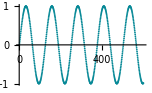

```mathematica
ListPlot[li]
```

フーリエ変換:

```mathematica
fli=Fourier[li];
```

パワースペクトル(周波数区分ごとの強度):

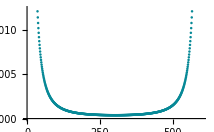

```mathematica
Abs[fli]^2//ListPlot
```

そのまま逆フーリエ変換:

```mathematica
if=InverseFourier[fli];
```

実数部をプロット:

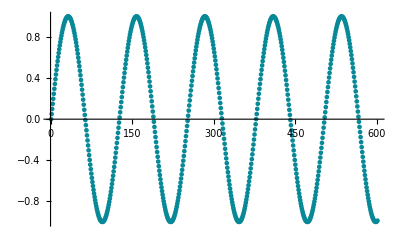

```mathematica
ListPlot[Map[Re,if]]
```

ノイズ付きサインカーブを生成

```mathematica
li=Table[Sin[x]+RandomReal[{-0.3,0.3}]//N,{x,0,30,0.05}];
```

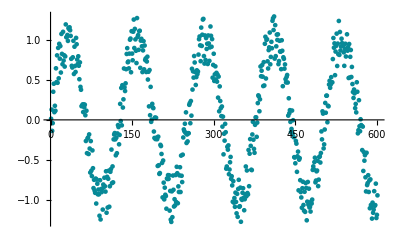

```mathematica
ListPlot[li]
```

フーリエ変換:

```mathematica
fli=Fourier[li];
```

```mathematica
fli//Length
```

601

ローパスフィルターもどきを生成:

```mathematica
flt=({Table[1,{50}],Table[0,{551}]}//Flatten);
```

ローパスフィルタをかけフーリエ逆変換:

```mathematica
iff=InverseFourier[fli flt];
```

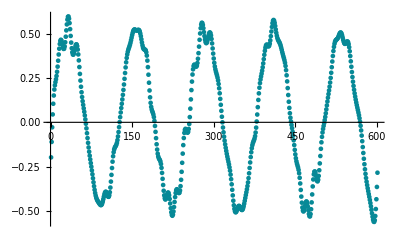

```mathematica
Map[Re,iff]//ListPlot
```

組み込みのローパスフィルター

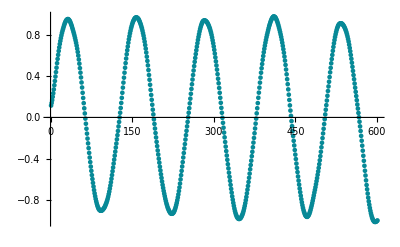

```mathematica
ListPlot[LowpassFilter[li,Pi/32]]
```

#### ガウシアンフィルター(2次元)

重み付き移動平均の一種。ひとつの要素に対して、自身と近傍の重み付き平均をその要素の新しい値とする。

ga() は各重みを計算する。

```mathematica
ga[x_,y_,s_]:=1/(2Pi s^2) E^(-(x^2+y^2)/(2s^2))
```

```mathematica
Plot3D[ga[x,y,2Pi],{x,-5,5},{y,-5,5}]
```

-Graphics3D-

```mathematica
w=Table[ga[x,y,1/Sqrt[2Pi]],{x,-1,1},{y,-1,1}]
```

{{ⅇ^(-2 π),ⅇ^-π,ⅇ^(-2 π)},{ⅇ^-π,1,ⅇ^-π},{ⅇ^(-2 π),ⅇ^-π,ⅇ^(-2 π)}}

```mathematica
totalw=Total[w,Infinity]
```

1+4 ⅇ^(-2 π)+4 ⅇ^-π

```mathematica
w/totalw
```

{{ⅇ^(-2 π)/(1+4 ⅇ^(-2 π)+4 ⅇ^-π),ⅇ^-π/(1+4 ⅇ^(-2 π)+4 ⅇ^-π),ⅇ^(-2 π)/(1+4 ⅇ^(-2 π)+4 ⅇ^-π)},{ⅇ^-π/(1+4 ⅇ^(-2 π)+4 ⅇ^-π),1/(1+4 ⅇ^(-2 π)+4 ⅇ^-π),ⅇ^-π/(1+4 ⅇ^(-2 π)+4 ⅇ^-π)},{ⅇ^(-2 π)/(1+4 ⅇ^(-2 π)+4 ⅇ^-π),ⅇ^-π/(1+4 ⅇ^(-2 π)+4 ⅇ^-π),ⅇ^(-2 π)/(1+4 ⅇ^(-2 π)+4 ⅇ^-π)}}

gat () は重みのテーブルを作成する。

```mathematica
gat[r_,s_]:=Module[{w,totalw},
w=Table[ga[x,y,s],{x,-r,r},{y,-r,r}];
totalw=Total[w,Infinity];
w/totalw
]
```

```mathematica
gat[1,1/Sqrt[2Pi]]//TableForm
```

ⅇ^(-2 π)/(1+4 ⅇ^(-2 π)+4 ⅇ^-π) | ⅇ^-π/(1+4 ⅇ^(-2 π)+4 ⅇ^-π) | ⅇ^(-2 π)/(1+4 ⅇ^(-2 π)+4 ⅇ^-π)
ⅇ^-π/(1+4 ⅇ^(-2 π)+4 ⅇ^-π) | 1/(1+4 ⅇ^(-2 π)+4 ⅇ^-π) | ⅇ^-π/(1+4 ⅇ^(-2 π)+4 ⅇ^-π)
ⅇ^(-2 π)/(1+4 ⅇ^(-2 π)+4 ⅇ^-π) | ⅇ^-π/(1+4 ⅇ^(-2 π)+4 ⅇ^-π) | ⅇ^(-2 π)/(1+4 ⅇ^(-2 π)+4 ⅇ^-π)

以下のような行列があったとき、

```mathematica
(t=Table[1,{x,3},{x,3}])//TableForm
```

1 | 1 | 1
1 | 1 | 1
1 | 1 | 1

上の行列の中央の値が以下のように変更される:

```mathematica
Total[t*gat[1,1/Sqrt[2Pi]],Infinity]//N
```

1.

Mathematicaにはより調整されたGaussianFilterが用意されている:

```mathematica
GaussianFilter[t,{1,1/Sqrt[2Pi]}]
```

{{0.127554,1.06846,3.59859},{1.06846,0.273858,1.06846},{3.59859,1.06846,0.127554}}

```mathematica
Array[a, {3, 3}]
```

{{a[1,1],a[1,2],a[1,3]},{a[2,1],a[2,2],a[2,3]},{a[3,1],a[3,2],a[3,3]}}

```mathematica
GaussianFilter[Table[1,{x,3},{x,3}],{1,1}][[2,2]]
```

1.

#### フィッテイング

```mathematica
??Fit
```

Fit[data,funs,vars] 変数 vars の関数 funs の線形な組合せで，与えられたデータの最小二乗法フィットを行う．

Attributes[Fit]={Protected}

```mathematica
l1=Table[n+RandomReal[{-1,1}],{n,20}]
```

{1.77847,2.40703,3.75922,3.76019,5.47608,6.01325,6.21187,7.34968,8.2711,9.14559,10.8581,12.3371,13.2659,14.1694,14.1663,16.3901,17.6836,18.8847,18.5385,20.8971}

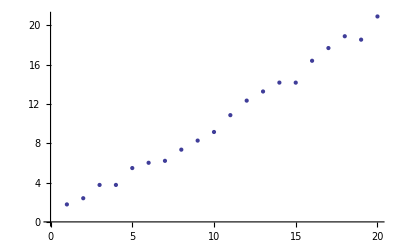

```mathematica
ListPlot[l1]
```

```mathematica
Fit[l1,{x},x]
```

1.00638 x

```mathematica
Fit[l1,{1,x},x]
```

0.004993+1.00602 x

```mathematica
Fit[l1,{1,x,x^2},x]
```

0.933295+0.752843 x+0.0120559 x^2

```mathematica
??FindFit
```

FindFit[data,expr,pars,vars] 変数 vars の関数 expr が data に最もフィットするようなパラメータ pars の数値を求める．
FindFit[data,{expr,cons},pars,vars] パラメータの制約条件 cons のもとで最高のフィットを求める．

Attributes[FindFit]={Protected}
 
Options[FindFit]={AccuracyGoal→Automatic,Compiled→Automatic,EvaluationMonitor→None,Gradient→Automatic,MaxIterations→Automatic,Method→Automatic,NormFunction→Norm,PrecisionGoal→Automatic,StepMonitor→None,WorkingPrecision→Automatic}

```mathematica
pr=Table[Prime[x], {x, 20}]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71}

```mathematica
FindFit[pr,a x Log[b+c x],{a,b,c},x]
```

{a→1.42076,b→1.65558,c→0.534645}

#### 最小自乗法の説明

3点、p1、p2、p3を直線y = b + axにフィットさせる。

```mathematica
p1={1,2};p2={2,4};p3={3,5}
```

{3,5}

```mathematica
data={p1,p2,p3}
```

{{1,2},{2,4},{3,5}}

Fit[]関数によるフィット

```mathematica
line=Fit[data,{1,x},x]
```

0.666667+1.5 x

フィットのステップ

フィットさせる関数を設定、求める係数は、a、b

```mathematica
f[x_]:=a+b x
```

説明変数の値を関数に代入

```mathematica
ft=Table[f[data[[n,1]]],{n,3}]
```

{a+b,a+2 b,a+3 b}

目的変数に値を設定

```mathematica
o=Table[data[[n,2]],{n,3}]
```

{2,4,5}

関数の出力と目的変数の値との差の自乗和を計算、この自乗和を最小にすることが目的

```mathematica
ds=Tr[(ft-o)^2]
```

(-2+a+b)^2+(-4+a+2 b)^2+(-5+a+3 b)^2

求めるべき係数のひとつ、aで微分

```mathematica
eq1=D[ds,a]//Expand
```

-22+6 a+12 b

求めるべき係数のもうひとつ、bで微分

```mathematica
eq2=D[Expand[ds],b]
```

-50+12 a+28 b

ふたつの条件を満たすa、bを求める

```mathematica
Solve[{eq1==0,eq2==0},{a,b}]
```

{{a→2/3,b→3/2}}

#### 最尤法の説明

Normal distribution:

```mathematica
nd[z_,m_,s_]:=E^(-(z-m)^2/(2s^2))
```

3点、p1、p2、p3を直線y = b + axにフィットさせる。

```mathematica
p1={1,2};p2={2,4};p3={3,5}
```

{3,5}

```mathematica
data={p1,p2,p3}
```

{{1,2},{2,4},{3,5}}

フィットさせる関数を設定、求める係数は、a、b

```mathematica
f[x_]:=a+b x
```

説明変数の値を関数に代入

```mathematica
ft=Table[f[data[[n,1]]],{n,3}]
```

{a+b,a+2 b,a+3 b}

説明変数の値に対応する確率を式で与える

```mathematica
nt=Table[nd[z[n],ft[[n]],s],{n,3}]
```

{ⅇ^(-(-a-b+z[1])^2/(2 s^2)),ⅇ^(-(-a-2 b+z[2])^2/(2 s^2)),ⅇ^(-(-a-3 b+z[3])^2/(2 s^2))}

目的変数に値を設定

```mathematica
o=Table[data[[n,2]],{n,3}]
```

{2,4,5}

目的変数の値を対応する確率密度関数に代入

```mathematica
pre=nt/.Table[z[n]->o[[n]],{n,3}]
```

{ⅇ^(-(2-a-b)^2/(2 s^2)),ⅇ^(-(4-a-2 b)^2/(2 s^2)),ⅇ^(-(5-a-3 b)^2/(2 s^2))}

確率密度関数の掛け合わせの値が最大になるよう係数を求める

=> log(確率密度関数)の足し合わせが最大になるよう係数を求める

```mathematica
Log[E,pre]
```

{Log[ⅇ^(-(2-a-b)^2/(2 s^2))],Log[ⅇ^(-(4-a-2 b)^2/(2 s^2))],Log[ⅇ^(-(5-a-3 b)^2/(2 s^2))]}

```mathematica
el=Simplify[Log[E,pre],{Element[a,Reals],Element[b,Reals],Element[s,Reals],s>0}]
```

{-(-2+a+b)^2/(2 s^2),-(-4+a+2 b)^2/(2 s^2),-(-5+a+3 b)^2/(2 s^2)}

```mathematica
e0=(Tr[el])
```

-(-2+a+b)^2/(2 s^2)-(-4+a+2 b)^2/(2 s^2)-(-5+a+3 b)^2/(2 s^2)

求めるべき係数のひとつ、aで微分

```mathematica
eq1=D[e0,a]
```

-(-2+a+b)/s^2-(-4+a+2 b)/s^2-(-5+a+3 b)/s^2

求めるべき係数のもうひとつ、bで微分

```mathematica
eq2=D[e0,b]
```

-(-2+a+b)/s^2-(2 (-4+a+2 b))/s^2-(3 (-5+a+3 b))/s^2

ふたつの条件を満たすa、bを求める

```mathematica
Solve[{eq1==0,eq2==0},{a,b}]
```

{{a→2/3,b→3/2}}

### 提出課題(2)

1. オシロスコープから得たデータをそのままプロットせよ(データの形状が分かるように縦横比を調整すること)

2. 1のデータを滑らかにしてプロットせよ(フィッティングでもよい)、ただし、もとのデータとの比較ができるようにすること

## 4.モデルの考え方と探索的データ解析

データの特徴を表す指標等を考える。モデルを仮定する場合としない場合がある。探索的データ解析はモデルを仮定しない。

### 分布モデル

#### 準備(統計の復習)

統計の基本的定理: 大数の法則、中心極限定理をもとに考えられたモデル

n次モーメント: Integrate[x^n f[x], {-Inf, +inf}, dx]は、f[x]が原点におよぼすn次モーメントである。

(モーメント)平滑指数(天野による定義、n次モーメントの値をより低い次数のモーメントの値で割ったもの): Integrate[x^n f[x],dx] / Integrate[x^m f[x],dx] ; n>m(通常、n=m+1)

確率密度分布の0次モーメントは1である。

度数分布の0次モーメント(表現がヘンだが)はサンプル総数である。

したがって、平均値は一種の平滑値でありその値は “1次モーメントの値/0次モーメントの値” となる。
(のちに、正規分布を例に詳しく見る)

#### 確率密度関数 (PDF: Probability Density Function)

PDFの-無限大から+無限大までの積分が1。

すべての区間で負の値をとらない。

```mathematica
??PDF
```

PDF[dist,x] x で評価された記号分布 dist についての確率密度関数(PDF)を返す．
PDF[dist,{x_1,x_2,…}] {x_1,x_2,…}で評価された記号分布 dist についての多変量確率密度関数を返す．
PDF[dist] 確率密度関数を純関数として返す．

Attributes[PDF]={Protected,ReadProtected}

```mathematica
PDF[NormalDistribution[0, 1], x]
```

(ⅇ^(-x^2/2))/(√(2 π))

```mathematica
Integrate[PDF[NormalDistribution[0,1],x],{x,-Infinity,Infinity}]
```

1

#### 累積分布関数 (CDF: Cumulative Distribution Function)

cdf(x) =∫_(-∞)^x pdf(t)ⅆt

PDFの-無限大からxまでの積分。x -> 無限大で、1に収束。

```mathematica
??CDF
```

CDF[dist,x] x で評価された記号分布 dist の累積分布関数を返す．
CDF[dist,{x_1,x_2,…}] {x_1,x_2,…}で評価された記号分布 dist についての多変量累積分布関数を返す．
CDF[dist] CDFを純関数として返す．

Attributes[CDF]={Protected,ReadProtected}

```mathematica
CDF[NormalDistribution[0,1],x]
```

1/2 Erfc[-x/(√2)]

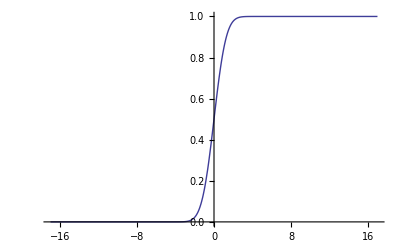

```mathematica
Plot[1/2 Erfc[-x/(√2)],{x,-16.970562748477143,16.970562748477143}]
```

#### 二重指数関数

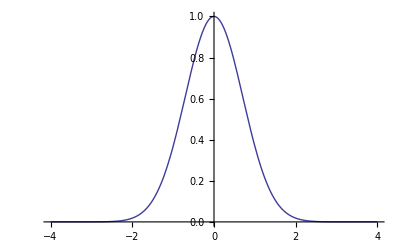

```mathematica
Plot[E^-(x^2),{x,-4,4}]
```

```mathematica
Integrate[E^-(x^2),{x,-Infinity,Infinity}]
```

√π

```mathematica
Integrate[E^-(-m+x)^2,{x,-Infinity,Infinity}]
```

√π

#### 正規分布#

正規分布の式、m:平均、s:標準偏差

```mathematica
PDF[NormalDistribution[m,s], x]
```

(ⅇ^(-(-m+x)^2/(2 s^2)))/(√(2 π) s)

正規分布の形

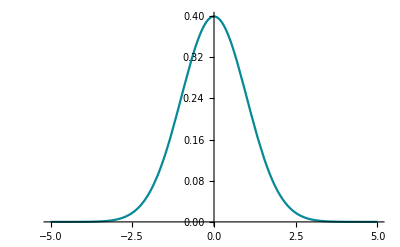

```mathematica
Plot[PDF[NormalDistribution[0,1],x],{x,-5,5}]
```

```mathematica
Integrate[PDF[NormalDistribution[0,1],x],{x,-Infinity,Infinity}] (*0次モーメント*)
```

1

```mathematica
Integrate[(x^0) PDF[NormalDistribution[0,1],x],{x,-Infinity,Infinity}] (*0次モーメント:明示的表現*)
```

1

1次モーメント / 0次モーメントは平均と一致する

```mathematica
Integrate[x PDF[NormalDistribution[m,1],x],{x,-Infinity,Infinity}](*1次モーメント*)
```

m

```mathematica
Integrate[(x^1) PDF[NormalDistribution[m,4],x],{x,-Infinity,Infinity}](*1次モーメント:明示的表現*)
```

m

度数分布の場合も同じ

```mathematica
l2={1,2,1,2,3,4,5,1,3,6}
```

{1,2,1,2,3,4,5,1,3,6}

```mathematica
Tally[l2]
```

{{1,3},{2,2},{3,2},{4,1},{5,1},{6,1}}

度数の合計 = 関数における0次モーメント

```mathematica
Map[#[[2]]&,Tally[l2]]//Tr
```

10

数値の合計 = 度数*数値要素の合計 = 関数における1次モーメント

```mathematica
Map[#[[1]]*#[[2]]&,Tally[l2]]//Tr
```

28

1次モーメント/0次モーメント = 平均

```mathematica
28/10
```

14/5

```mathematica
Mean[l2]
```

14/5

2次モーメントは分散と一致する(平均がゼロの場合)

```mathematica
Integrate[x^2 PDF[NormalDistribution[0,3],x],{x,-Infinity,Infinity}]
```

9

(x - mean(x))に対する2次モーメントは分散と一致する

```mathematica
Integrate[(x-4)^2 PDF[NormalDistribution[4,3],x],{x,-Infinity,Infinity}]
```

9

関数 CentralMoment[] は平均に対するn次モーメントを与える

```mathematica
CentralMoment[NormalDistribution[0,3],2]
```

9

```mathematica
CentralMoment[NormalDistribution[4,3],2]
```

9

正規分布の歪度(3次モーメント/2次モーメント^(3/2))は0

```mathematica
Skewness[NormalDistribution[0,1]]
```

0

正規分布の尖度(4次モーメント/2次モーメント^2)は3

```mathematica
Kurtosis[NormalDistribution[0,1]]
```

3

正規分布の変曲点は平均値±標準偏差の値と一致する

```mathematica
Solve[D[D[PDF[NormalDistribution[m,s], x],x],x]==0,{x}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→m-s},{x→m+s}}

```mathematica
Reduce[D[D[PDF[NormalDistribution[m,s], x],x],x]==0,{x}]
```

s≠0&&(x==m+s||x==m-s)

```mathematica
FourierTransform[PDF[NormalDistribution[0,t]],t,w]
```

FourierTransform[Exp[-1/2 ((#1-0)/t)^2]/(t √(2 π))&,t,w]

正規分布のフーリエ変換は正規分布となる

```mathematica
PDF[NormalDistribution[0,1]][t]
```

(ⅇ^(-t^2/2))/(√(2 π))

```mathematica
FourierTransform[PDF[NormalDistribution[0,1]][t],t,w]
```

(ⅇ^(-w^2/2))/(√(2 π))

```mathematica
PDF[NormalDistribution[0,1]][w]===FourierTransform[PDF[NormalDistribution[0,1]][t],t,w]
```

True

#### その他の分布 : 二項分布

```mathematica
PDF[BinomialDistribution[n, p], k]
```

Piecewise[{{(1-p)^(-k+n) p^k Binomial[n,k], 0≤k≤n}, {0, True}}]

```mathematica
n!/(k! (n - k)!) (* = Binomial[n,k] *)
```

(n!)/(k! (-k+n)!)

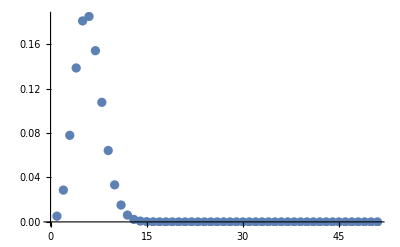

```mathematica
ListPlot[Table[PDF[BinomialDistribution[50, 0.1],k],{k,0,50}],PlotRange->All]
```

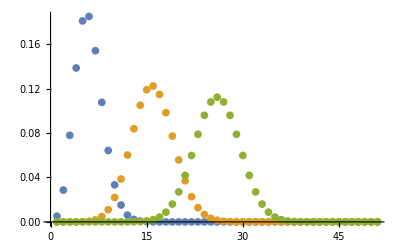

```mathematica
ListPlot[{Table[PDF[BinomialDistribution[50, 0.1],k],{k,0,50}],Table[PDF[BinomialDistribution[50, 0.3],k],{k,0,50}],Table[PDF[BinomialDistribution[50, 0.5],k],{k,0,50}]},PlotRange->All]
```

不連続なので積分できない ->  積分のかわりに足し合わせると:

```mathematica
Table[PDF[BinomialDistribution[50, 0.1], k], {k, 0, 50}]//Tr
```

1.

#### その他の分布 : 負の二項分布

```mathematica
PDF[NegativeBinomialDistribution[n, p], k]
```

Piecewise[{{(1-p)^k p^n Binomial[-1+k+n,-1+n], k≥0}, {0, True}}]

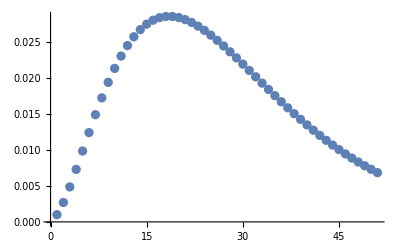

```mathematica
ListPlot[Table[PDF[NegativeBinomialDistribution[3, 0.1],k],{k,0,50}],PlotRange->All]
```

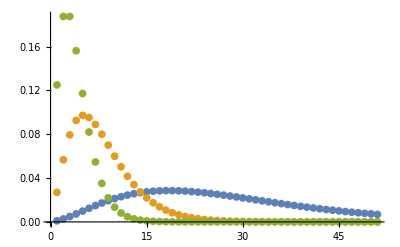

```mathematica
ListPlot[{Table[PDF[NegativeBinomialDistribution[3, 0.1],k],{k,0,50}],Table[PDF[NegativeBinomialDistribution[3, 0.3],k],{k,0,50}],Table[PDF[NegativeBinomialDistribution[3, 0.5],k],{k,0,50}]},PlotRange->All]
```

```mathematica
ListPlot3D[Table[PDF[NegativeBinomialDistribution[s, p], k],{p,0.1,0.5,0.1},{s,{2,3,4,5}},{k,0,50}],PlotRange->All]
```

-Graphics3D-

分布にはすべての事象が含まれない:

```mathematica
Integrate[PDF[NegativeBinomialDistribution[5, 0.5], k], {k, 0, Infinity}]
```

0.988035

#### その他の分布 : poisson分布

```mathematica
PDF[PoissonDistribution[μ], k]
```

Piecewise[{{(ⅇ^-μ μ^k)/(k!), k≥0}, {0, True}}]

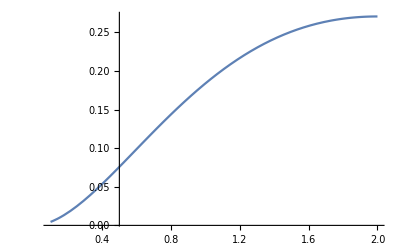

```mathematica
Plot[PDF[PoissonDistribution[n], 2],{n,0.1,2},PlotRange->All]
```

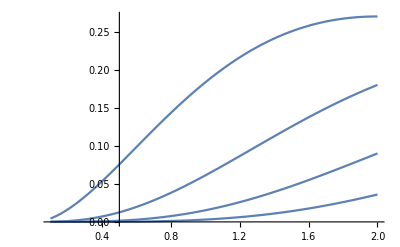

```mathematica
Plot[Table[PDF[PoissonDistribution[n], k],{k,2,5}],{n,0.1,2},PlotRange->All]
```

```mathematica
Integrate[PDF[PoissonDistribution[n], 2],{n,0,Infinity}]
```

1

#### その他の分布 : Zip族

Zipf分布: Zipfの法則 -アイテムの出現回数とそのランクを掛けたものがほぼ一定である- に基づく

```mathematica
??ZipfDistribution
```

ZipfDistribution[ρ] 母数 ρ のゼータ分布を表す．
ZipfDistribution[n,ρ] 範囲 n のZipf分布を表す．

Attributes[ZipfDistribution]={NHoldAll,Protected,ReadProtected}

下記は、データのサイズが4の場合のランクが1から4位までの生産量比

```mathematica
PDF[ZipfDistribution[4, 1], {1, 2, 3, 4}] // N
```

{0.702439,0.17561,0.0780488,0.0439024}

```mathematica
PDF[ZipfDistribution[ρ], k]
```

Piecewise[{{k^(-1-ρ)/Zeta[1+ρ], k≥1}, {0, True}}]

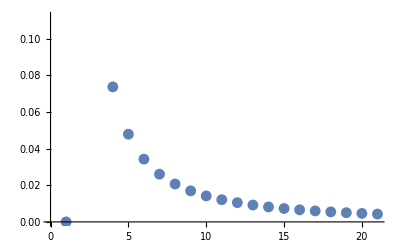

```mathematica
ListPlot[Table[PDF[ZipfDistribution[0.5], k],{k,0,20}]]
```

積分は発散しない :

```mathematica
Integrate[PDF[ZipfDistribution[0.5], k],{k,0,Infinity}]
```

0.765587

20151105

20151112(休講)

zipf関数; r=rank:ランク、f:頻度、a:係数、c:係数。
f × r = c
f × r^a = c ; a = 1
通常、aはきわめて1に近くなるとされる。aを計ることによって、不均衡の度合いを見積もれる。

```mathematica
f=zipf[rank_,a_,c_]:=c*rank^(-a)
```

```mathematica
fitargs=FindFit[Map[#[[2]]&,worldShips],zipf[rank,a,c],{a,c},rank]
```

{a→0.929126,c→5963.12}

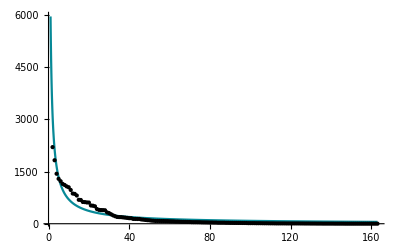

```mathematica
Plot[zipf[rank,a,c]/.fitargs,{rank,1,Length[worldShips]},Epilog->MapIndexed[Point[Flatten[{#2,#1[[2]]}]]&,worldShips],PlotRange->All]
```

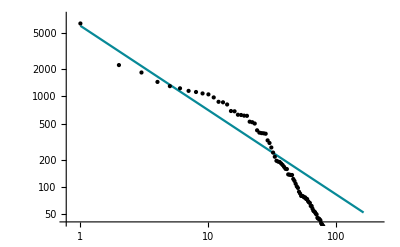

```mathematica
gobjLLP=LogLogPlot[zipf[rank,a,c]/.fitargs,{rank,1,Length[worldShips]},Epilog->MapIndexed[Point[Flatten[{Log[#2],Log[#1[[2]]]}]]&,worldShips]]
```

ロトカの法則: x:論文の件数、y:それぞれx件の貢献をした著者の割合、n:係数、c:係数のとき、
x^n × y = c

OrlovとChitashviliによれば、Zipf族の関数はつぎの定義のように一般化できる

```mathematica
orlovZ[m]:=Integrate[(Log[1+x]^(γ-1) x^α)/((1+x)^(m+1) (1+x)^β),{x,0,Infinity}]/Integrate[(Log[1+x]^(γ-1) x^(α-1))/((1+x)^(β+1)),{x,0,Infinity}]
```

```mathematica
Timing[orlovZ[m]]
```

{11.4543,(∫_0^∞ x^α (1+x)^(-1-m-β) Log[1+x]^(-1+γ)ⅆx)/(∫_0^∞ x^(-1+α) (1+x)^(-1-β) Log[1+x]^(-1+γ)ⅆx)}

Zipfの法則

```mathematica
Timing[orlovZ[m]/.{α->1,β->1,γ->1}]
```

{14.1139,ConditionalExpression[1/(m+m^2),Re[m]>0]}

Yuleの法則

```mathematica
Timing[orlovZ[m] /. {β -> α, γ -> 1}]
```

{22.4946,ConditionalExpression[(α Gamma[m] Gamma[1+α])/Gamma[1+m+α],Re[α]>0&&Re[m]>0]}

Yule-Simonの法則

```mathematica
Timing[orlovZ[m]/.{α->1,γ->1}]
```

{15.3987,ConditionalExpression[β/((-1+m+β) (m+β)),Re[β]>0&&Re[m+β]>1]}

### 探索的データ解析

#### データ分布からの知識抽出

データ解析を行う第一歩は、データの分布を概観すること

分布における代表値の位置

分布の分散度

分布の歪み

分布の尖り

分布の多峰性、単峰性

外れ値

#### 幹葉表示(分布の表現)

```mathematica
list1={5,9,1,4,6,5,13,7,15,6,8,10,4}
```

{5,9,1,4,6,5,13,7,15,6,8,10,4}

```mathematica
list2={1,9,10,8,9,15,13,4,18,7,8,12,9}
```

{1,9,10,8,9,15,13,4,18,7,8,12,9}

幹を作る

```mathematica
Max[{list1,list2}]
```

18

```mathematica
Min[{list1,list2}]
```

1

```mathematica
r=Range[0,Max[{list1,list2}]+5,5]
```

{0,5,10,15,20}

```mathematica
cat=Partition[r,2,1]
```

{{0,5},{5,10},{10,15},{15,20}}

```mathematica
stem=Drop[r,-1]
```

{0,5,10,15}

list1の葉を作る

```mathematica
l1p=Table[Select[list1,#>cat[[n,1]]&&#≤cat[[n,2]]&],{n,Length[cat]}]
```

{{5,1,4,5,4},{9,6,7,6,8,10},{13,15},{}}

```mathematica
takeLastDigit[x_]:=ToExpression[StringTake[ToString[x],-1]]
```

```mathematica
l1=Map[takeLastDigit,l1p,{2}]
```

{{5,1,4,5,4},{9,6,7,6,8,0},{3,5},{}}

list2の葉を作る

```mathematica
l2p=Table[Select[list2,#>cat[[n,1]]&&#≤cat[[n,2]]&],{n,Length[cat]}]
```

{{1,4},{9,10,8,9,7,8,9},{15,13,12},{18}}

```mathematica
l2=Map[takeLastDigit,l2p,{2}]
```

{{1,4},{9,0,8,9,7,8,9},{5,3,2},{8}}

list1の幹葉表示

```mathematica
TableForm[Transpose[{stem,l1}],TableDirections->{Column,Row,Row}]
```

0 | 5 | 1 | 4 | 5 | 4
5 | 9 | 6 | 7 | 6 | 8 | 0
10 | 3 | 5
15 |

list2の幹葉表示

```mathematica
TableForm[Transpose[{l2,stem}],TableDirections->{Column,Row,Row},TableAlignments->{Right}]
```

1 | 4 | 0
9 | 0 | 8 | 9 | 7 | 8 | 9 | 5
5 | 3 | 2 | 10
8 | 15

list1、list2の幹葉表示 -> 二つのデータ群の頻度分布の比較

```mathematica
GridBox[Transpose[{l2,stem,l1}],ColumnAlignments->{Right,Center,Left}]//DisplayForm
```

{1,4} | 0 | {5,1,4,5,4}
{9,0,8,9,7,8,9} | 5 | {9,6,7,6,8,0}
{5,3,2} | 10 | {3,5}
{8} | 15 | {}

ヒストグラムでは個々の値が分からない。一方、幹葉表示で有効なデータ個数は200-300程度。

#### 最大値(分布の範囲)

```mathematica
??Max
```

Max[x_1,x_2,…] yields the numerically largest of the x_i. 
Max[{x_1,x_2,…},{y_1,…},…] yields the largest element of any of the lists.

Attributes[Max]={Flat,NumericFunction,OneIdentity,Orderless,Protected}

#### 最小値(分布の範囲)

```mathematica
??Min
```

Min[x_1,x_2,…] yields the numerically smallest of the x_i. 
Min[{x_1,x_2,…},{y_1,…},…] yields the smallest element of any of the lists.

Attributes[Min]={Flat,NumericFunction,OneIdentity,Orderless,Protected}

#### 中央値(分布における位置)

d[M] = d[ (N+1) / 2 ]

データが奇数個の場合は一個の値、偶数個の場合は2個の平均

```mathematica
??Median
```

RowBox[{"Median", "[", StyleBox["list", "TI"], "]"}] StyleBox[RowBox[{"list", " "}], "TI"]の要素の中央値を与える．
RowBox[{"Median", "[", StyleBox["dist", "TI"], "]"}] 記号分布 StyleBox["dist", "TI"] の中央値を与える．

Attributes[Median]={Protected,ReadProtected}

```mathematica
list1
```

{5,9,1,4,6,5,13,7,15,6,8,10,4}

```mathematica
Sort[list1][[{(1+13)/2}]]//Mean
```

6

```mathematica
Median[list1]
```

6

中央値は平均値に比べ外れ値の影響を受けにくい

```mathematica
Mean[list1]//N
```

7.15385

```mathematica
Median[list1]
```

6

```mathematica
ReplacePart[list1,1->100]//Mean//N
```

14.4615

```mathematica
ReplacePart[list1,1->100]//Median
```

7

#### 最頻値(分布における位置)

最も多く出現する値、またはカテゴリー

```mathematica
??Commonest
```

Commonest[list] gives a list of the elements that are the most common in list.
Commonest[list,n] gives a list of the n most common elements in list.

Attributes[Commonest]={Protected,ReadProtected}

```mathematica
Commonest[list1]
```

{5,4,6}

#### ヒンジ値(分布の分散)

中央値と最大値、最小値の中間を表す要約値 -> 文位数

上ヒンジ値

```mathematica
list1//Sort
```

{1,4,4,5,5,6,6,7,8,9,10,13,15}

```mathematica
Sort[list1][[(1+13)(3/4)//Round]]
```

9

```mathematica
Quantile[list1,3/4]
```

9

下ヒンジ値

```mathematica
Sort[list1][[(1+13)(1/4)//Round]]
```

5

```mathematica
Quantile[list1,1/4]
```

5

```mathematica
??Quantile
```

Quantile[list,q] list の q 分位数を与える．
Quantile[list,{q_1,q_2,…}] 分位数 q_1, q_2, …のリストを与える．
Quantile[list,q,{{a,b},{c,d}}] パラメータ a，b，c，d で指定された分位数の定義を使う．
Quantile[dist,q] 記号分布 dist の分位数を与える．

Attributes[Quantile]={Protected,ReadProtected}

#### 5数要約(分布の要約)

{最小値、下ヒンジ値、中央値、上ヒンジ値、最大値}

```mathematica
fiveNumbers[list_]:=Quantile[list,Table[n/4,{n,0,4}]]
```

```mathematica
fiveNumbers[list1]
```

{1,5,6,9,15}

#### 中点要約値(分布の歪み)

(上ヒンジ値+下ヒンジ値)/2

```mathematica
Quantile[list1,Table[n/4,{n,{1,3}}]]//Mean
```

7

#### ヒンジ散布度(分布の尖り)

上ヒンジ値 -下ヒンジ値

```mathematica
Apply[Subtract,Quantile[list1,Table[n/4,{n,{3,1}}]]]
```

4

#### 分布モデルとの対応

正規分布モデルプロットに対する幹葉表示

平均値に対する中央値

(∫x d[x]ⅆx)/(∫d[x]ⅆx) <=> d[M] = d[ (N+1) / 2 ]

標準偏差に対する擬似標準偏差(ヒンジ散布度を1.35で割った値)

√(∫x^2 d[x]ⅆx) <=>  (d[ (N+1) (3/4) ] - d[ (N+1) (1/4) ]) / 1.35

歪度に対する中点要約値

(∫x^4 d[x]ⅆx)/((∫x^2 d[x]ⅆx)^2) <=> (d[H] + d[L])/2 = (d[(N+1) (3/4)] + d[(N+1) (1/4)])/2

尖度に対するヒンジ散布度(上ヒンジ値と下ヒンジ値の差)

(∫x^3 d[x]ⅆx)/((∫x^2 d[x]ⅆx)^(3/2)) <=> d[H] - d[L] = d[ (N+1) (3/4) ] - d[ (N+1) (1/4) ]

#### 分布の多峰性単峰性 (データ集合の概念化)

多峰性の判定は難しく、領域分割アルゴリズム等を利用する。

#### 箱型図(外れ値の表現)*

```mathematica
??BoxWhiskerChart
```

RowBox[{BoxWhiskerChart, "[", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], "]"}] 値 SubscriptBox[StyleBox["x", "TI"], StyleBox["i", "TI"]]の箱ひげ図を作成する．
RowBox[{BoxWhiskerChart, "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["bwspec", "TI"]}], "]"}] 記号指定 StyleBox["bwspec", "TI"] による箱ひげ図を作成する．
RowBox[{BoxWhiskerChart, "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["data", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["data", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["…", "TR"]}], "]"}] 各 SubscriptBox[StyleBox["data", "TI"], StyleBox["i", "TI"]]の記号による箱ひげ図を作成する．
RowBox[{BoxWhiskerChart, "[", RowBox[{RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["data", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["data", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["…", "TR"]}], "]"}] 複数のデータ集合RowBox[{"{", RowBox[{SubscriptBox[StyleBox["data", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["data", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]から箱ひげ図を作成する．

Attributes[BoxWhiskerChart]={Protected,ReadProtected}

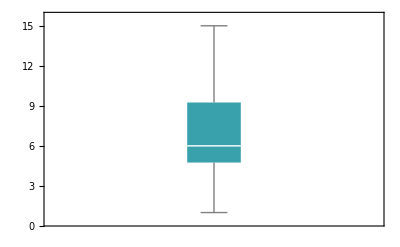

```mathematica
BoxWhiskerChart[list1]
```

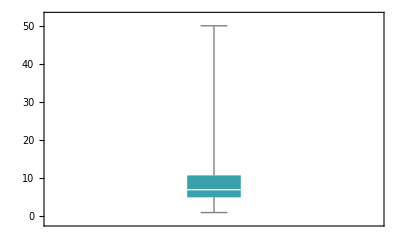

```mathematica
BoxWhiskerChart[{5,9,1,4,6,5,13,7,15,6,8,10,50}]
```

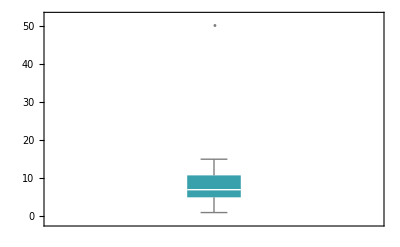

```mathematica
BoxWhiskerChart[{5,9,1,4,6,5,13,7,15,6,8,10,50},"Outliers"]
```

### ランダムネスと分布モデル(参考)

一様乱数の度数分布

```mathematica
ra=Table[Random[],{100}];
```

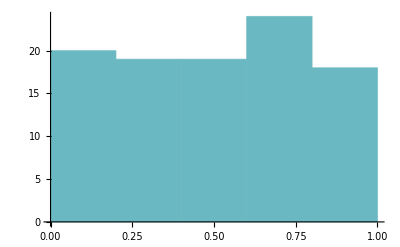

```mathematica
Histogram[ra]
```

一様乱数から分布を作る -変換法-

分布の積分の逆関数を求めることができれば、あるいは、解析的にその値を得ることができれば変換法により一様乱数から、特定の分布を得られる。

--CDFによる変換法--

```mathematica
CDF[NormalDistribution[0,1]]//FullForm
```

Function[Times[Erfc[Times[Plus[0,Times[-1,Slot[1]]],Power[Times[Sqrt[2],1],-1]]],Power[2,-1]]]

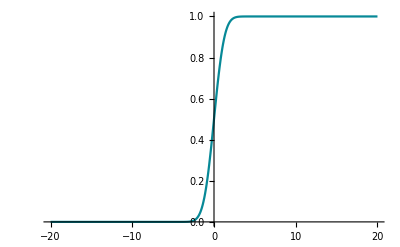

```mathematica
Plot[CDF[NormalDistribution[0,1]][x],{x,-20,20}]
```

```mathematica
ifc:=InverseFunction[CDF[NormalDistribution[0,1]]]
```

```mathematica
ira=Map[ifc[#//N]&,ra];
```

InverseFunction::ifun: 逆関数が使用されています．値は多価逆関数のため失われている可能性があります．

General::stop: この計算中に，InverseFunction :: ifunのこれ以上の出力は表示されません．

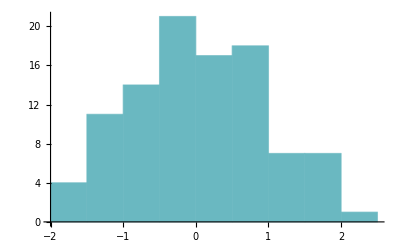

```mathematica
Histogram[ira]
```

--PDFによる変換法(積分のステップが必要)--

```mathematica
PDF[NormalDistribution[0, 1]]
```

Exp[-1/2 ((#1-0) 1/1)^2]/(1 √(2 π))&

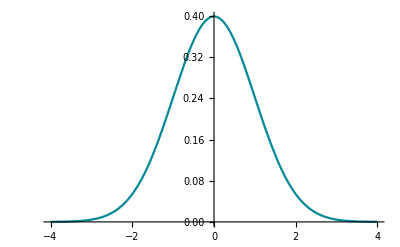

```mathematica
Plot[PDF[NormalDistribution[0, 1]][x],{x,-4,4}]
```

```mathematica
Integrate[PDF[NormalDistribution[0, 1],x],{x,-Infinity,t}]
```

1/2 (1+Erf[t/(√2)])

```mathematica
Function[Evaluate[Integrate[PDF[NormalDistribution[0, 1],x],{x,-Infinity,t}]/.t->#]]
```

1/2 (1+Erf[#1/(√2)])&

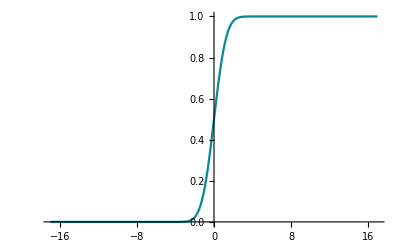

```mathematica
Plot[(1/2 (1+Erf[#1/(√2)])&)[x],{x,-16.970562748477143,16.970562748477143}]
```

```mathematica
ifp:=InverseFunction[Function[Evaluate[Integrate[PDF[NormalDistribution[0, 1],x],{x,-Infinity,t}]/.t->#]]]
```

```mathematica
ifp[0.2]
```

InverseFunction::ifun: 逆関数が使用されています．値は多価逆関数のため失われている可能性があります．

-0.841621

```mathematica
ira=Map[ifp[#//N]&,ra];
```

InverseFunction::ifun: 逆関数が使用されています．値は多価逆関数のため失われている可能性があります．

General::stop: この計算中に，InverseFunction :: ifunのこれ以上の出力は表示されません．

```mathematica
ira[[1]]
```

0.0875382

```mathematica
Histogram[ira,10]
```

-Graphics-

RandomVariate[]で分布を作る

```mathematica
rnd=RandomVariate[NormalDistribution[],100]
```

{1.12944,0.0667754,-0.685765,-1.87905,0.724557,0.403541,-2.29471,-0.158809,0.58159,0.263489,-0.611356,-1.85942,-1.61631,0.0591306,0.862338,0.0146405,0.147682,0.45561,-1.67173,1.04546,0.216582,-2.74,-0.500338,-0.297155,0.332535,1.75362,-0.627699,-0.736214,0.00484673,1.07477,1.47632,-2.20706,0.560031,-0.413896,0.11264,0.710594,1.85706,0.936879,0.500304,0.2719,0.0745312,0.574742,-0.674902,0.504498,-0.830964,-1.77589,0.944143,0.216793,-0.195488,1.46562,-1.26727,-0.911334,1.08296,0.696018,0.528526,0.176029,0.327725,-0.708677,-0.440768,0.478415,-1.24381,-0.43252,0.376459,2.25795,0.75771,-0.514604,0.711436,1.1931,-1.31523,-0.617337,1.47106,-1.82384,-0.319373,-0.586393,-1.13961,0.928071,0.18008,0.180271,0.0243893,0.451837,0.724544,-0.542178,-0.0578592,-0.0661324,-0.0165823,-0.756506,1.90902,1.46343,0.311923,-1.59495,-0.609641,1.438,0.0271522,0.56852,-0.638775,0.0678525,0.321766,0.848301,-2.48246,-0.01498}

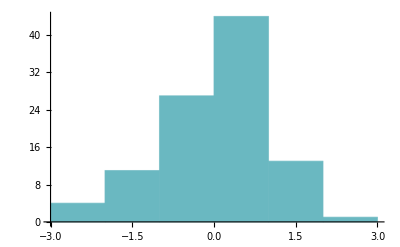

```mathematica
Histogram[rnd]
```

### 提出課題(3)

1. 任意のデータを取得し、適切な度数分布表示を行え

2. 1のデータの箱型図を作成せよ

## 休講分(20151112)のレポート課題

### 提出課題(E.1)

任意の論文の図と表に関して批判的なレポートを作成せよ。

1. 任意の論文中の任意の表を選び、表の構成について批判的に解説せよ。
一瞥して分かりやすいか、その理由、本文との対応などを述べる。

2. 任意の論文中の任意の図を選び、図の構成について批判的に解説せよ。
一瞥して分かりやすいか、その理由、本文との対応などを述べる。

## 5.様々な類似度・距離の考え方

データ間の関係(近さ、遠さ)を数量的に評価する。

### 類似度の概念

ふたつの個体が似ていることを定義する(この関数をSとする)。

三つの個体(Va、Vb、Vc)を考える。

VaとVbがVaとVcより似ているなら:
S(Va,Vb) > S(Va,Vc).00.00䀐

反射律: S(Va,Va) = 1 ; 完全に一致すれば1

対称律: S(Va,Vb) = S(Vb,Va) ; どちらから見ても類似度は同じ

### 非類似度の概念

ふたつの個体が似ていないことを定義する(この関数をDSとする)。

VaとVbがVaとVcより似ているなら:
S(Va,Vb) < S(Va,Vc).00.00䀐

反射律: DS(Va,Va) = 0 ; 完全に一致すれば0

対称律: DS(Va,Vb) = DS(Vb,Va) ; どちらから見ても非類似度は同じ

### 距離の概念

ふたつの個体のあいだの空間(距離)を定義する(この関数をDとする)。

VaとVbがVaとVcより近いなら:
D(Va,Vb) < D(Va,Vc).00.00䀐

反射律: D(Va,Va) = 0 ; 完全に一致すれば0

対称律: D(Va,Vb) = D(Vb,Va) ; どちらから見ても距離は同じ

推移律: D(Va,Vc) <= D(Va,Vb) + D(Vb,Vc); VaとVcの距離は、VaとVbの距離とVbとVcの距離の合計より小さい

### 個体間の距離・類似度

1変量

離散値(定性値)
-名義尺度、順序尺度

連続値(定量値)
-間隔尺度、比尺度

多変量

離散値(定性値)
-名義尺度、順序尺度

連続値(定量値)
-間隔尺度、比尺度

### 個体群間の距離・類似度(クラスタリングで詳しく説明)

1変量

離散値(定性値)
-名義尺度、順序尺度

連続値(定量値)
-間隔尺度、比尺度

多変量

離散値(定性値)
-名義尺度、順序尺度

連続値(定量値)
-間隔尺度、比尺度

### 名義尺度をもとにした類似度

{0,1}型データ、つまり、各カテゴリに対して1(属する)、0(属さない)の形。

m: 両方とも1

n: 両方とも0

o: {0,1}

p: {1,0}

t: アイテム数(要素数)

```mathematica
va={0,0,1,1,0}
vb={1,1,0,1,0}
```

{0,0,1,1,0}

{1,1,0,1,0}

一致係数: S(Va,Vb) = (m+n)/t

```mathematica
s[1][va_,vb_]:=Count[Map[Apply[Equal,#]&,Transpose[{va,vb}]],True]/Length[va]
```

類似比:

```mathematica
s[2][va_,vb_]:=Module[{trl,m,n,t},
trl=Transpose[{va,vb}];
m=Count[trl,{1,1}];
n=Count[trl,{0,0}];
t=Length[trl];
m/(t-n)
]
```

```mathematica
s[2][va,vb]
```

1/4

Rogers-Tanimotoの係数:

```mathematica
s[3][va_,vb_]:=Module[{trl,m,n,o,p,t},
trl=Transpose[{va,vb}];
m=Count[trl,{1,1}];
n=Count[trl,{0,0}];
o=Count[trl,{1,0}];
p=Count[trl,{0,1}];
t=Length[trl];
(m+n)/(t+o+p)
]
```

Hamannの係数:

```mathematica
s[4][va_,vb_]:=Module[{trl,m,n,o,p,t},
trl=Transpose[{va,vb}];
m=Count[trl,{1,1}];
n=Count[trl,{0,0}];
o=Count[trl,{1,0}];
p=Count[trl,{0,1}];
t=Length[trl];
((m+n)-(o+p))/t
]
```

Russel-Raoの係数:

```mathematica
s[5][va_,vb_]:=Module[{trl,m,t},
trl=Transpose[{va,vb}];
m=Count[trl,{1,1}];
t=Length[trl];
m/t
]
```

ファイ係数: S(Va,Vb) = (mn - op) / ((m+o) (p+n) (m+p) (o+n))^(1/2)

```mathematica
s[6][va_,vb_]
```

### 名義尺度による距離

{0,1}型データ、つまり、各カテゴリに対して1(属する)、0(属さない)の形。

不一致係数: D(Va,Vb) = (o+p)/t

```mathematica
d[1][va_,vb_]:=Module[{trl,o,p,t},
trl=Transpose[{va,vb}];
o=Count[trl,{1,0}];
p=Count[trl,{0,1}];
t=Length[trl];
(o+p)/t
]
```

```mathematica
d[1][va,vb]
```

3/5

ハミング距離: D(Va,Vb) = o+p

```mathematica
d[2][va_,vb_]:=Module[{trl,o,p},
trl=Transpose[{va,vb}];
o=Count[trl,{1,0}];
p=Count[trl,{0,1}];
(o+p)
]
```

```mathematica
d[2][va,vb]
```

3

```mathematica
??HammingDistance
```

HammingDistance[u,v] 文字列またはベクトル u と v のハミング距離を返す．

Attributes[HammingDistance]={Protected}
 
Options[HammingDistance]={IgnoreCase→False}

```mathematica
HammingDistance[va,vb]
```

3

### 順序尺度をもとにした類似度

スピアマンの順位相関

```mathematica
1-6/(n^3-n) Sum[(rank[va[i]]-rank[vb[i]])^2,{i,n}]
```

1-(6 ∑_i^n (rank[va[i]]-rank[vb[i]])^2)/(-n+n^3)

```mathematica
Needs["MultivariateStatistics`"]
```

```mathematica
??SpearmanRankCorrelation
```

RowBox[{"SpearmanRankCorrelation", "[", RowBox[{StyleBox["xlist", "TI"], ",", StyleBox["ylist", "TI"]}], "]"}] 実数値ベクトル StyleBox["xlist", "TI"] と StyleBox["ylist", "TI"] に対するスピアマン(Spearman)の順位相関係数 ρ を返す．

Attributes[SpearmanRankCorrelation]={Protected}
 
SpearmanRankCorrelation[{_?NumericQ},{_?NumericQ}]:=(If[TrueQ[MultivariateStatistics`Private`$SpearmanRhoMessage],MultivariateStatistics`Private`$SpearmanRhoMessage=False;Message[General::obsfun,SpearmanRankCorrelation,SpearmanRho]];Indeterminate)
 
SpearmanRankCorrelation[MultivariateStatistics`Private`args___]:=(If[TrueQ[MultivariateStatistics`Private`$SpearmanRhoMessage],MultivariateStatistics`Private`$SpearmanRhoMessage=False;Message[General::obsfun,SpearmanRankCorrelation,SpearmanRho]];Block[{MultivariateStatistics`Private`res=MultivariateStatistics`Private`iRankCorrelation[{MultivariateStatistics`Private`args},SpearmanRankCorrelation]},MultivariateStatistics`Private`res/;MultivariateStatistics`Private`res=!=$Failed])

ケンドールの順位相関

```mathematica
??KendallRankCorrelation
```

KendallRankCorrelation[xlist,ylist] 実数値ベクトル xlist と ylist に対するケンドール(Kendall)の順位相関係数 τ を返す．

Attributes[KendallRankCorrelation]={Protected}
 
KendallRankCorrelation[{_?NumericQ},{_?NumericQ}]:=(If[TrueQ[MultivariateStatistics`Private`$KendallTauMessage],MultivariateStatistics`Private`$KendallTauMessage=False;Message[General::obsfun,KendallRankCorrelation,KendallTau]];Indeterminate)
 
KendallRankCorrelation[MultivariateStatistics`Private`args___]:=(If[TrueQ[MultivariateStatistics`Private`$KendallTauMessage],MultivariateStatistics`Private`$KendallTauMessage=False;Message[General::obsfun,KendallRankCorrelation,KendallTau]];Block[{MultivariateStatistics`Private`res=MultivariateStatistics`Private`iRankCorrelation[{MultivariateStatistics`Private`args},KendallRankCorrelation]},MultivariateStatistics`Private`res/;MultivariateStatistics`Private`res=!=$Failed])

### 定量値(間隔尺度、比率尺度)をもとにした類似度

各要素は変数値

```mathematica
va={2,3,1,3,4}
vb={2,1,1,4,4}
vc=va
```

{2,3,1,3,4}

{2,1,1,4,4}

{2,3,1,3,4}

パターン類似度: S(Va,Vb) = ∑v_ai v_bi / (∑v_ai^2 v_bi^2)^(1/2)

```mathematica
s[7][va_,vb_]:=Tr[va*vb]/Sqrt[Tr[va^2]*Tr[vb^2]]
```

```mathematica
s[7][va,vb]
```

6 √(6/247)

```mathematica
s[7][va,vc]
```

1

相関係数: S(Va,Vb) = sab / (saa sbb)^(1/2) ; saa = ∑(v_ai- mean(v_a))^2 / t ; sab = ∑(v_ai - mean(v_a))(v_bi - mean(v_b)) / t

```mathematica
??Correlation
```

Correlation[v_1,v_2] ベクトル v_1とベクトル v_2の間の相関関係を返す．
Correlation[m] 行列 m の相関行列を返す．
Correlation[m_1,m_2] 行列 m_1と m_2の相関行列を返す．
Correlation[dist] 多変量記号分布 dist の相関行列を返す．
Correlation[dist,i,j] 多変量記号分布 dist の(i,j)次相関を返す．

Attributes[Correlation]={Protected,ReadProtected}

コサイン類似度: S(Va,Vb) = cos(Va,Vb)

```mathematica
1-CosineDistance[va,vb]
```

1-CosineDistance[va,vb]

内積(反射率は満たさない): S(Va,Vb) = ∑_(i=1)^(|Va|) a[i]*b[i]

```mathematica
??Inner
```

Inner[f,list_1,list_2,g] Dotを一般化したもので，f が掛け算，g が足し算の役割を担う．

Attributes[Inner]={Protected}

### 定量値(間隔尺度、比率尺度)をもとにした距離

ユークリッド距離: D(Va,Vb) = (∑(v_ai-v_bi)^2)^(1/2)

```mathematica
??EuclideanDistance
```

RowBox[{"EuclideanDistance", "[", RowBox[{StyleBox["u", "TI"], ",", StyleBox["v", "TI"]}], "]"}] ベクトル StyleBox["u", "TI"] と StyleBox["v", "TI"] の間のユークリッド(Euclidean)距離を返す．

Attributes[EuclideanDistance]={Protected}

重み付きユークリッド距離: D(Va,Vb) = (∑(ki(v_ai-v_bi))^2)^(1/2) ; k_i = 重み

標準化ユークリッド距離: D(Va,Vb) = (∑1/si(v_ai-v_bi)^2)^(1/2) ; si = ∑_(j=1)^N (v_ji-mean(v_i)) / N ; N =  個体数(a,bのふたつ)

市街距離(マンハッタン距離): D(Va,Vb) = ∑|v_ai-v_bi|

```mathematica
??ManhattanDistance
```

ManhattanDistance[u,v] ベクトル u と v の間のマンハッタン（市街地）距離を返す．

Attributes[ManhattanDistance]={Protected}

ミンコフスキー距離: D(Va,Vb,k) = (∑|v_ai-v_bi|^k)^(1/k) ; k = 1のときマンハッタン距離、k = 2のときユークリッド距離

マハラノビスの汎距離: D(Va,Vb) = (∑∑(v_ai - v_bj)w_ij(v_aj - v_bi))^(1/2) ; w_ij = 1/(u-1)∑_(r=1)^u [(v_ri-mean(v_i))(v_rj-mean(v_j))] 、分散共分散行列の逆行列

マハラノビスの汎距離: D(Va,Vb) = Sqrt[(v_a-v_b)^Tσ^-1(v_a - v_b)] ; T:転置; σ^-1: 分散共分散行列の逆行列、サンプルの大きさ (平均と分散)を考慮(標準化)した距離。

コサイン距離 : D (Va, Vb) = 1 - cos (Va, Vb)

```mathematica
??CosineDistance
```

CosineDistance[u,v] ベクトル u と v の間の余弦距離を返す．

Attributes[CosineDistance]={Protected}

(参考)分散・共分散:

ベクトルxの分散は  1/N∑_(n=1)^N (x_n-mean(x))^2 と定義される。

二つのベクトルの分散または共分散を次のように定義できる。  1/N∑_(n=1)^N (x_n-mean(x))(y_n-mean(y))

```mathematica
cov[0][x_,y_]:=Module[{mx,my},
mx=Mean[x];
my=Mean[y];
Tr[Map[#-mx&,x]*Map[#-my&,y]]/Length[x]
]
```

```mathematica
m={{1,2,3,4},{3,4,5,6}}
```

{{1,2,3,4},{3,4,5,6}}

```mathematica
cov[0][m[[1]],m[[2]]]//N
```

1.25

```mathematica
cov[0][m[[1]]/2,2 m[[2]]]//N
```

1.25

分散共分散行列とは、ベクトル集合の各ベクトル同士(ペアワイズ)の分散をすべて計算したもの。

```mathematica
Table[cov[0][m[[s]],m[[t]]],{s,Length[m]},{t,Length[m]}]
```

{{5/4,5/2},{5/2,5}}

```mathematica
Covariance[Transpose[m]]
```

{{5/3,10/3},{10/3,20/3}}

Mathematicaは、 Length[x]-1 で割っている。

分散共分散行列を返す関数: vCov[]

```mathematica
cov[0][x_,y_]:=Module[{mx,my},
mx=Mean[x];
my=Mean[y];
Tr[Map[#-mx&,x]*Map[#-my&,y]]/Length[x]
]
```

```mathematica
vCov[x_,y_]:=Table[Apply[cov[0],{x,y}[[{s,t}]]],{s,2},{t,2}]
```

```mathematica
vCov[mat_]:=Outer[cov[0],mat,mat,1]
```

```mathematica
vCov[m2[[1]],m2[[2]]]
```

{{1/2,2},{2,8}}

```mathematica
vCov[m2]
```

{{1/2,2},{2,8}}

### 文字列間の距離・類似度

#### 編集距離

編集距離(レーベンシュタイン距離): 二つの文の間で、片方の文をどのように編集すれば、もう片方の文になるかのステップをカウント。

置換に関しては、1とカウントする場合と2(削除・挿入)とカウントする場合がある。

```mathematica
??EditDistance
```

EditDistance[u,v] 文字列間あるいはベクトル u と v の間の編集距離（レーベンシュタイン距離）を返す．

Attributes[EditDistance]={Protected}
 
Options[EditDistance]={IgnoreCase→False}

```mathematica
EditDistance["C","A"]
```

1

```mathematica
EditDistance["C",""]
```

1

```mathematica
EditDistance["","A"]
```

1

```mathematica
EditDistance["ABC","ACB"]
```

2

```mathematica
EditDistance["ABCD","ADCA"]
```

2

```mathematica
EditDistance["ABCD","ADC"]
```

2

#### アライメントによる類似度

アライメントとは:
- 調整の意味。
- 二つ以上の文字列をそれらの類似度が最も高くなるようにそれぞれ編集すること。
- 編集には「ギャップの挿入」を用いる。
- DNA塩基(アミノ酸)配列間の類似度を求めるのに使われる。

なぜ、化学物質の類似性が文字列の類似性で代表できるのか? -> 黒板で説明。

20151119

20151126(休講日)

アライメントの例 -> スライド: 5回/筑波2010_3_v1.天野改.ppt(.pdf)

授業中課題: 文字列アライメント(スライド: 5回/筑波2013_3_prn.pdf)#

MathematicaにはSequenceAlignment[]がある:

```mathematica
??SequenceAlignment
```

RowBox[{"SequenceAlignment", "[", RowBox[{SubscriptBox[StyleBox["s", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["s", "TI"], StyleBox["2", "TR"]]}], "]"}] 文字列あるいはリスト SubscriptBox[StyleBox["s", "TI"], StyleBox["1", "TR"]]とリスト SubscriptBox[StyleBox["s", "TI"], StyleBox["2", "TR"]]中の一連の要素の選択的なアラインメントを求め，連続するマッチする文字列と異なる文字列を返す．

Attributes[SequenceAlignment]={Protected}
 
Options[SequenceAlignment]={GapPenalty→0,IgnoreCase→False,MergeDifferences→True,Method→Global,SimilarityRules→Automatic}

スコア行列の選択には、SimilarityRulesを使う。

```mathematica
??SimilarityRules
```

SimilarityRules SequenceAlignment等の関数のオプションで，要素ペア間で仮定する類似度スコアの規則のリストを与える．

Attributes[SimilarityRules]={Protected}

```mathematica
SequenceAlignment["ADHE","ADIE",SimilarityRules->"PAM250"]
```

{AD,{H,I},E}

アライメントしただけでは類似度は求まらない。類似度を求めるには別の関数を使う。

```mathematica
NeedlemanWunschSimilarity["ADHE", "ADIE",SimilarityRules->"PAM250"]
```

8.

#### サブ文字列出現頻度ベクトルによる距離

- N-gramやタームのカウントによるベクトル間の距離(黒板)
- codon usage
- 参考: 世の中の書籍に登場するタームを調べるには、Google Ngram Viwer を使う。

### 距離行列

複数の個体間(ペアワイズ)の距離を行列で表したもの。

```mathematica
m1={1,2}
m2={3,5}
m3={5,10}
```

{1,2}

{3,5}

{5,10}

(0 | √13 | 4 √5
√13 | 0 | √29
4 √5 | √29 | 0)

ベクトルのリストを引数とし、距離行列を返すプログラムを作成し、上記の3つのベクトルの距離行列を求めよ。#

#### 回答

```mathematica
Outer[f,{m1,m2,m3},{m1,m2,m3},1]
```

{{f[m1,m1],f[m1,m2],f[m1,m3]},{f[m2,m1],f[m2,m2],f[m2,m3]},{f[m3,m1],f[m3,m2],f[m3,m3]}}

```mathematica
Outer[f,{m1,m2,m3},{m1,m2,m3},1]
```

{{f[{1,2},{1,2}],f[{1,2},{3,5}],f[{1,2},{5,10}]},{f[{3,5},{1,2}],f[{3,5},{3,5}],f[{3,5},{5,10}]},{f[{5,10},{1,2}],f[{5,10},{3,5}],f[{5,10},{5,10}]}}

```mathematica
Outer[EuclideanDistance,{m1,m2,m3},{m1,m2,m3},1]
```

{{0,√13,4 √5},{√13,0,√29},{4 √5,√29,0}}

```mathematica
dmat[l_List]:=Outer[EuclideanDistance,l,l,1]
```

```mathematica
dmat[{m1,m2,m3}]//MatrixForm
```

(0 | √13 | 4 √5
√13 | 0 | √29
4 √5 | √29 | 0)

### 提出課題(4)

長さ1000文字以上の任意の文字列を4つ以上取得し、

1. 編集距離(またはアライメントスコア)をもとにした距離行列(またはスコア行列)と、

2. N-gram頻度ベクトルによる距離行列を求めよ。

## 6.非階層的クラスタリング

データ間の関係からより大きな構造を見抜く。

クラスタリングとは:
そもそも分類とは、狭義には次のふたつ: 1. クラシフィケーション -あらかじめ定義されたクラスにサンプルを割り当てる- 、2. クラスタリング -クラスを動的に定義しつつ(クラスタ数も変化する)、サンプルをクラスに割り当てる- 、と理解しておけばよい。広義(ふたつを合わせたもの)には、「クラシフィケーション」=「分類」を使う。

クラスタリングとは、「分けること」であるが、その方法論には「分割」と「凝集」のふたつの方向性がある。

### 非階層的クラスタリング

n個の個体を排他的なk個のクラスに割り当てる。
大域的にはkも変動するため、クラスへの割当て方の数は、整数の分割に関係する数になる。
何らかの指標があればこれらすべてをテストすれば最適解が得られるが、膨大な計算量となる。

```mathematica
Needs["Combinatorica`"]
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

```mathematica
??IntegerP*
```

RowBox[{"IntegerPartitions", "[", StyleBox["n", "TI"], "]"}] gives a list of all possible ways to partition the integer StyleBox["n", "TI"] into smaller integers. 
RowBox[{"IntegerPartitions", "[", RowBox[{StyleBox["n", "TI"], ",", StyleBox["k", "TI"]}], "]"}] gives partitions into at most StyleBox["k", "TI"] integers. 
RowBox[{"IntegerPartitions", "[", RowBox[{StyleBox["n", "TI"], ",", RowBox[{"{", StyleBox["k", "TI"], "}"}]}], "]"}] gives partitions into exactly StyleBox["k", "TI"] integers. 
RowBox[{"IntegerPartitions", "[", RowBox[{StyleBox["n", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["k", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["k", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] gives partitions into between SubscriptBox[StyleBox["k", "TI"], StyleBox["min", "TI"]] and SubscriptBox[StyleBox["k", "TI"], StyleBox["max", "TI"]] integers. 
RowBox[{"IntegerPartitions", "[", RowBox[{StyleBox["n", "TI"], ",", StyleBox["kspec", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["s", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["s", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] gives partitions involving only the SubscriptBox[StyleBox["s", "TI"], StyleBox["i", "TI"]]. 
RowBox[{"IntegerPartitions", "[", RowBox[{StyleBox["n", "TI"], ",", StyleBox["kspec", "TI"], ",", StyleBox["sspec", "TI"], ",", StyleBox["m", "TI"]}], "]"}] limits the result to the first StyleBox["m", "TI"] partitions.

Attributes[IntegerPartitions]={Protected}

n = 4 の場合、各クラスの個数の分け方は、

```mathematica
IntegerPartitions[4]
```

{{4},{3,1},{2,2},{2,1,1},{1,1,1,1}}

すべての場合においてのクラスの分け方は、

```mathematica
SetPartitions[4]//Length
```

15

n = 10 でその分け方は10万を超え、

```mathematica
SetPartitions[10]//Length
```

115975

n = 11 でその分け方は約70万、場合分けのパターンを作るだけで数秒を要する。

```mathematica
Timing[SetPartitions[11]//Length]
```

{6.11085,678570}

そこで、多くの場合ヒューリスティクなアルゴリズムが用いられる。

#### リーダーアルゴリズム

しきい値がある。クラスは未定。

最初の個体を最初のクラスターに入れる。

次の個体を対象にして，以下を繰り返す。個体が無くなれば終了。

最初から順にクラスターを対象にして，以下を繰り返す。

対象とする個体と，対象とするクラスターの最初の個体との距離を求める。距離がしきい値より小さければその個体を対象とするクラスタに入れ，2に戻る。

対象とする個体を新たなクラスターに登録する。.00.00䂉.00.00퀀䁸.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ᡰ₈.05.00.00.00.00.00읕₈.04.00昁敩嵻₈䭈₇.03h62d4rv4gk81g7d3ru.03쐚ސĀ.07.00環境
設定を表示.00.00.00䎏₆ໄ₆	.00.00.00.00.00.00.00.00.00.00䁂.00.00.00.00.00䄴ￋ兑.00.00倀䂌.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00뱚4A30₣.04.00.00.00.02.00.00.00.00.00.00䀤.00.00.00.00.00멒⇩.0b湹愮㙨搲爴㑶歧ㄸ㙮礵畲.00.00.00.00.00.00.00.03쐚ތ
.00.00怀䁼.00.00䀀䂊.00.00怀䁻.00

```mathematica
list1={5,6,1,9,2,7}
```

{5,6,1,9,2,7}

例:

しきい値を3とする

最初の個体を最初のクラスターに入れる

クラスター:{{5}}        残り:{6,1,9,2,7}

残りの個体のひとつとクラスターの代表値(最初の個体)とをを次々と比べ、しきい値より近ければクラスターに加え、そうでなければ新しくクラスターを作る。新しくクラスターができたら、また、残りの個体のひとつとクラスターを比べて行く。

6 -- {5}とくらべる -> 距離(=1)はしきい値未満 -> {5}に加える

{{5,6}}

1 -- {5,6}に加えない、新しくクラスターを作る、{5,6}の代表は5。

{{5,6},{1}}        残り:{9,2,7}

9 -- {5,6}にも{1}にも加えない、新しくクラスターを作る

{{5,6},{1},{9}}       残り:{2,7}

2 -- {1}に加える

{{5,6},{1,2},{9}}       残り:{7}

7 -- {5,6}に加える

{{5,6,7},{1,2},{9}}       残り:{}

残りがなくなったので終了

問題: 順序により結果が変わる、逆順 -- {7,2,9,1,6,5}だと

{7,2,9,1,6,5}

最初の個体を最初のクラスターに入れる

クラスター: {{7}}      残り: {2,9,1,6,5}

2 -- 新しくクラスターを作る

{{7},{2}}   ;   {9,1,6,5}

9 -- {7} に加える

{{7,9},{2}}     ;     {1,6,5}

1 -- {2}に加える

{{7,9},{2,1}}    ;     {6,5}

6 -- {7,9}に加える

{{7,9,6},{2,1}}      ;     {5}

5 -- {7,9,6}に加える

{{7,9,6,5},{2,1}}     ;     {}

回避するにはソートする。

#### 最大距離アルゴリズム

全ての個体間の距離を求め、その最大のものを二つのクラスター中心とする。

新たなクラスター中心ができなくなるまで，以下を繰り返す。

残りの全ての個体について、全てのクラスター中心との距離を求め，最小の距離のものを取り出す。この値が、最初の距離のある一定割合（たとえば１／３）以上であるとき、対応する個体の位置を新たなクラスター中心とする。

全ての個体を最も近いクラスターに入れる。.00.00.00.00.02.00.00.00.00.00￿.00.00.00.00.00.00.00.00.00.00.00.00.0b.00ꤝ⃩.04る。.00.00.00.00.00.00.00.00ꀀ䂅.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00떴헕￿￪.00:da88¿፠↕.04.00

```mathematica
list1
```

{5,6,1,9,2,7}

```mathematica
dmat[l_]:=Outer[EuclideanDistance,l,l]
```

```mathematica
TableForm[dmat[list1],TableHeadings->{list1,list1}]
```

| 5 | 6 | 1 | 9 | 2 | 7
5 | 0 | 1 | 4 | 4 | 3 | 2
6 | 1 | 0 | 5 | 3 | 4 | 1
1 | 4 | 5 | 0 | 8 | 1 | 6
9 | 4 | 3 | 8 | 0 | 7 | 2
2 | 3 | 4 | 1 | 7 | 0 | 5
7 | 2 | 1 | 6 | 2 | 5 | 0

しきい値は、たとえば、最大距離(=8)の1/3

```mathematica
8/3//N
```

2.66667

```mathematica
Max[dmat[list1]]
```

8

例:

まず、クラスターとクラスターの代表を決める

クラスター: {{1},{9}}     最初のクラスター間の距離 8 、しきい値 を8/3 = 2.7とする    残り:{5,6,2,7}

5 -- {1}との距離=4、{9}との距離=4 -> 新しくクラスターを作る

クラスター{{1},{9},{5}}       残り:{6,2,7}

6 -- クラスター{5}に対してしきい値未満(まだ反映しない)

クラスター{{1},{9},{5}}       残り:{2,7}

2 -- クラスター{1}に対してしきい値未満(まだ反映しない)

クラスター{{1},{9},{5}}       残り:{7}

7 -- クラスター{9}または{5}にに対してしきい値未満(まだ反映しない)　　　　残り:{}

クラスターができたので、クラスター代表以外の個体を最も近いクラスターに属させる

クラスター{{1},{9},{5}}  に {6,2,7} を配分

{{1,2},{9,7},{5,6}} ; 7の割り当ては{5}または{9}に対して行なうがここではクラスタのメンバー数を偏らせないように配分している。

リーダーアルゴリズムや最大距離法では、クラスター代表が固定される。「同距離」問題。

20151203

#### k-means(繰り返し法)

分割数kを決める。

各個体をランダムにクラスターに属させる。

各クラスターに属する個体の平均をクラスターの代表値とする。

各個体を最も近い代表値を持つクラスターに属させる。

3,4を繰り返すとやがて収束する。

```mathematica
list1
```

{5,6,1,9,2,7}

例:

kを3とする

クラスターをランダムに生成:{{5,6},{1,9},{2,7}}

```mathematica
cnt=Map[Mean,{{5,6},{1,9},{2,7}}]//N
```

{5.5,5.,4.5}

クラスター中心:{5.5, 5, 4.5}

各個体をもっとも近いクラスター中心をもつクラスターに属させる

```mathematica
TableForm[Outer[EuclideanDistance,list1,cnt],TableHeadings->{list1,cnt}]
```

| 5.5 | 5. | 4.5
5 | 0.5 | 0. | 0.5
6 | 0.5 | 1. | 1.5
1 | 4.5 | 4. | 3.5
9 | 3.5 | 4. | 4.5
2 | 3.5 | 3. | 2.5
7 | 1.5 | 2. | 2.5

5 -> クラス2
6 -> クラス1
1 -> クラス3
9 -> クラス1
2 -> クラス3
7 -> クラス1
{{6,9,7},{5},{1,2}}

```mathematica
cnt=Map[Mean[#]&,{{6,9,7},{5},{1,2}}]//N
```

{7.33333,5.,1.5}

クラスター中心{7.3, 5, 1.5}

```mathematica
TableForm[Outer[EuclideanDistance,list1,cnt],TableHeadings->{list1,cnt}]
```

| 7.33333 | 5. | 1.5
5 | 2.33333 | 0. | 3.5
6 | 1.33333 | 1. | 4.5
1 | 6.33333 | 4. | 0.5
9 | 1.66667 | 4. | 7.5
2 | 5.33333 | 3. | 0.5
7 | 0.333333 | 2. | 5.5

5 -> クラス2
6 -> クラス2
1 -> クラス3
9 -> クラス1
2 -> クラス3
7 -> クラス1
{{9,7},{5,6},{1,2}}

```mathematica
cnt=Map[Mean[#]&,{{9,7},{5,6},{1,2}}]//N
```

{8.,5.5,1.5}

```mathematica
TableForm[Outer[EuclideanDistance,list1,cnt],TableHeadings->{list1,cnt}]
```

| 8. | 5.5 | 1.5
5 | 3. | 0.5 | 3.5
6 | 2. | 0.5 | 4.5
1 | 7. | 4.5 | 0.5
9 | 1. | 3.5 | 7.5
2 | 6. | 3.5 | 0.5
7 | 1. | 1.5 | 5.5

5 -> クラス2
6 -> クラス2
1 -> クラス3
9 -> クラス1
2 -> クラス3
7 -> クラス1
{{9,7},{5,6},{1,2}}

収束した。

問題: 収束の判定をすると遅くなる。kが固定される。初期配置がランダムに決まるため同じ結果(精度)が得られない。

問題の回避: 繰り返しの複数回に一回ごとに収束判定。kをある範囲内で変動させることができる。

#### その他

フォギーの方法、再配置法などがあるが、k-meansに近い考え。また、k-meansは手順が単純でヒューリスティクスを導入しやすく、多くの改良がある。

Mathematicaには、よりインテリジェントなFindClusters[]が用意されている。

```mathematica
??FindClusters
```

RowBox[{"FindClusters", "[", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["e", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["e", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], "]"}] StyleBox[SubscriptBox[StyleBox["e", "TI"], "i"], "TI"] を同種の要素ごとにクラスタにまとめる．
RowBox[{"FindClusters", "[", RowBox[{"{", RowBox[{RowBox[{SubscriptBox[StyleBox["e", "TI"], StyleBox["1", "TR"]], "→", SubscriptBox[StyleBox["v", "TI"], StyleBox["1", "TR"]]}], ",", RowBox[{SubscriptBox[StyleBox["e", "TI"], StyleBox["2", "TR"]], "→", SubscriptBox[StyleBox["v", "TI"], StyleBox["2", "TR"]]}], ",", StyleBox["…", "TR"]}], "}"}], "]"}] 各クラスタの StyleBox[SubscriptBox[StyleBox["e", "TI"], "i"], "TI"] に対応する StyleBox[SubscriptBox["v", "i"], "TI"] を返す．
RowBox[{"FindClusters", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["e", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["e", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], "→", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["v", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["v", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] 同じ結果を返す．
RowBox[{"FindClusters", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["e", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["e", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["n", "TI"]}], "]"}] StyleBox[SubscriptBox[StyleBox["e", "TI"], "i"], "TI"] を厳密に StyleBox["n", "TI"] 個のクラスタに分割する．

Attributes[FindClusters]={Protected}
 
Options[FindClusters]={DistanceFunction→Automatic,Method→Automatic}

Method->”Optimize”にすると、前述のような”局所解”アルゴリズムが使われる(詳細は不明)。

```mathematica
??ClusteringComponents
```

ClusteringComponents[array] array の各要素がその要素が含まれるクラスタを表す整数指標で置換された配列を与える．
ClusteringComponents[array,n] 最高で n 個のクラスタを求める．
ClusteringComponents[array,n,level] array の指定レベルのクラスタを求める．
ClusteringComponents[image] image の値が同じような画素のクラスタを求める．
ClusteringComponents[image,n] image 中のクラスタを最高で n 個求める．

Attributes[ClusteringComponents]={Protected,ReadProtected}

### MathematicaのFindClusters[]

```mathematica
??FindClusters
```

RowBox[{"FindClusters", "[", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["e", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["e", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], "]"}] partitions the StyleBox[SubscriptBox[StyleBox["e", "TI"], "i"], "TI"] into clusters of similar elements. 
RowBox[{"FindClusters", "[", RowBox[{"{", RowBox[{RowBox[{SubscriptBox[StyleBox["e", "TI"], StyleBox["1", "TR"]], "→", SubscriptBox[StyleBox["v", "TI"], StyleBox["1", "TR"]]}], ",", RowBox[{SubscriptBox[StyleBox["e", "TI"], StyleBox["2", "TR"]], "→", SubscriptBox[StyleBox["v", "TI"], StyleBox["2", "TR"]]}], ",", StyleBox["…", "TR"]}], "}"}], "]"}] returns the StyleBox[SubscriptBox["v", "i"], "TI"] corresponding to the StyleBox[SubscriptBox[StyleBox["e", "TI"], "i"], "TI"] in each cluster. 
RowBox[{"FindClusters", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["e", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["e", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], "→", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["v", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["v", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] gives the same result. 
RowBox[{"FindClusters", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["e", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["e", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["n", "TI"]}], "]"}] partitions the StyleBox[SubscriptBox[StyleBox["e", "TI"], "i"], "TI"] into exactly StyleBox["n", "TI"] clusters.

Attributes[FindClusters]={Protected}
 
Options[FindClusters]={DistanceFunction→Automatic,Method→Automatic}

```mathematica
cdata=Table[RandomReal[],{6},{2}]
```

{{0.526512,0.589285},{0.758619,0.647851},{0.468669,0.59884},{0.985838,0.819541},{0.31016,0.305051},{0.400327,0.603764}}

```mathematica
FindClusters[cdata]
```

{{{0.526512,0.589285},{0.758619,0.647851},{0.468669,0.59884},{0.985838,0.819541},{0.31016,0.305051},{0.400327,0.603764}}}

```mathematica
FindClusters[cdata,2]
```

{{{0.526512,0.589285},{0.468669,0.59884},{0.31016,0.305051},{0.400327,0.603764}},{{0.758619,0.647851},{0.985838,0.819541}}}

```mathematica
FindClusters[cdata,2,Method->"Optimize"]
```

{{{0.526512,0.589285},{0.468669,0.59884},{0.31016,0.305051},{0.400327,0.603764}},{{0.758619,0.647851},{0.985838,0.819541}}}

```mathematica
FindClusters[cdata,2,Method->"Agglomerate"]
```

{{{0.526512,0.589285},{0.758619,0.647851},{0.468669,0.59884},{0.985838,0.819541},{0.400327,0.603764}},{{0.31016,0.305051}}}

```mathematica
Map[Length,FindClusters[cdata,DistanceFunction->(Norm[#1-#2,5]^5&)]]
```

```mathematica
FindClusters[cdata->Range[Length[cdata]],2,Method->"Agglomerate"]
```

{{1,2,3,4,6},{5}}

### 非階層クラスタ分割の適正性の指標

#### Compactness

各クラスタがどの程度コンパクトにまとまっているか:

クラスタ中心から各メンバーへの距離の合計や平均

メンバー同士の距離の合計や平均

最大距離や最小距離を使うその他の指標

#### Separativity

クラスタ間がどの程度分離できているか:

全サンプル重心から各クラスタ中心までの距離の合計や平均

クラスタ間のメンバーの距離の合計や平均

最大距離や最小距離を使うその他の指標

#### Calinski and Harabaszの指標 (Intelligent Data Analysis 12 (2008) 529–548)

値が大きいほど良い

```mathematica
(BCSM/(k-1))/(WCSM/(n-k))
```

(BCSM (-k+n))/((-1+k) WCSM)

n: 全個体数

k: クラスタ数

BCSM(Between-cluster scatter matrix):

```mathematica
Sum[n[i] d[z[i],z[tot]]^2,{i,k}]
```

∑_i^k d[z[i],z[tot]]^2 n[i]

z[i] : 各クラスター中心

z[tot] : 全サンプル中心

n[i] : 各クラスタメンバー数

WCSM(Between-cluster scatter matrix):

```mathematica
Sum[d[x[i,j],z[i]]^2,{i,k},{j,n[i]}]
```

∑_i^k ∑_j^n[i] d[x[i,j],z[i]]^2

x[i,j] : クラスタiのj番目のメンバー

#### Score Function (Intelligent Data Analysis 12 (2008) 529–548)

値が大きいほど良い

```mathematica
1-(1/(E^(E^(BCD-WCD))))
```

1-ⅇ^(-ⅇ^(BCD-WCD))

BCD(Between-cluster distance):

```mathematica
1/(n k) Sum[n[i] d[z[i],z[tot]]^2,{i,k}]
```

(∑_i^k d[z[i],z[tot]]^2 n[i])/(k n)

n: 全個体数

k: クラスタ数

WCD(Within-cluster distance):

```mathematica
1/k Sum[Sqrt[1/n[i] Sum[d[x[i,j],z[i]],{j,n[i]}]],{i,k}]
```

(∑_i^k √((∑_j^n[i] d[x[i,j],z[i]])/n[i]))/k

#### 天野の指標

```mathematica
k Product[c[i]^(r[i]/r[tot]),{i,k}] (*小さいほど良い*)
```

k ∏_i^k c[i]^(r[i]/r[tot])

```mathematica
k (Product[c[i]^(r[i]/r[tot]),{i,k}] )^(1/k)(*小さいほど良い*)
```

k (∏_i^k c[i]^(r[i]/r[tot]))^(1/k)

k: クラスタ数

c[i]: クラスタiのメンバー数

r[i] : クラスタiの平均半径

r[tot] : 全サンプルの平均半径

#### シルエット指標 (Intelligent Data Analysis 12 (2008) 529–548)

```mathematica
1/n  Sum[(b[i]-a[i])/Max[a[i],b[i]],{i,n}]
```

(∑_i^n (-a[i]+b[i])/Max[a[i],b[i]])/n

a[i] :  the average distance between point i and all other points in its own cluster

b[i] :  the minimum of the average dissimilarities between i and points in other clusters

#### 指標の重要性

クラス分けの最適化とはその評価関数が出力する指標を最大化(最小化)することと同値であるため、その指標を最大化(最小化)するメソッドが見つかれば、クラス分けのglobal solutionを見つけることができる。

### 提出課題(5)

長さ500文字以上の任意の文字列を10個以上取得し、適切な非階層クラスタリングを行なえ。

## 7.階層的クラスタリング

データ間の関係からより大きな構造(階層構造)を見抜く。

階層クラスタリングは、n個の個体を用いてすべての個体が接続する最適なツリーを構成する問題と言える。
もし、評価関数があればすべての組み合わせでツリーを構成しすべてをテストすることにより最適解が得られる。
これには非階層クラスタリングよりもさらに大きな計算資源を要する(((n-1)!)^2 と思われる)。

ヒューリスティクではあるが適切な手順を決めれば、唯一のツリーをより少ないステップで構築することができる。

### 階層的クラスタリング(凝集法) (スライド:7回/知識構造化法_中山先生7.pptx (一部使用))

#### 最短距離法

クラスター間距離:

d(C[1],C[2]) = min[x[1]∈C[1],x[2]∈C[2]] (d(x[1],x[2]))

#### 最長距離法

クラスター間距離:

d(C[1],C[2]) = max[x[1]∈C[1],x[2]∈C[2]] (d(x[1],x[2]))

#### 群平均法

クラスター間距離:

d(C[1],C[2]) = 1/(|C[1]|  |C[2]|)∑_(x[1]∈C[1])^(|C[1]|) ∑_(x[2]∈C[2])^(|C[2]|) d(x[1],x[2])

#### 重心法

クラスター間距離:

d(C[1],C[2]) = d(OverBar[C[1]],OverBar[C[2]])

#### ウォード法

d(C[1],C[2]) = E(C[1]∩C[2])-E(C[1])-E(C[2])
E(A): 集合Aの重心から各要素への距離の２乗和

### 階層的クラスタリング(分裂法) (スライド:7回/知識構造化法_中山先生8.pptx)

#### 最短スパニングツリー法

1. Minimum Spanning Tree (MST)をつくる。
MSTを求める方法には、プリム法、クラスカル法がある。

2. MSTの長いパスから順に連結を切る。

#### 最短スパニングパス法

1. Minimum Spanning Path (MSP)をつくる
MSPを求めるには、すべての単一始点最短経路より総経路長が最短のものを選ぶ。
単一始点最短経路を求める際には、すべてのノードペアにおいて直接の距離が算出されている(すなわち、距離行列においてd(a,c)<d(a,b)+d(b,c)を満たしている)ので、ダイクストラ法より簡単になる。

2. MSPの長いパスから順に連結を切る。

### クラスタツリーの適正性の指標 (今期やらない)(スライド:7回/知識構造化法_中山先生7-2.pptx)

### マルチプルアライメントによる文字列階層的クラスタリング(スライド: 7回/nara-wu-2_阿久津先生.ppt (一部使用))

#### DP

O(2^N n^N)
N: 配列の個数
n: 配列の長さ

#### CLUSTAL-W(プログレッシブアライメント)

DP+ヒューリスティクス
ただし、アミノ酸配列、塩基配列に特化

### MathematicaのAgglomerate[]

パッケージを読み込まないと関数名を検索できない。

```mathematica
Needs["HierarchicalClustering`"]
```

```mathematica
??Agglomerate
```

RowBox[{"Agglomerate", "[", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["e", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["e", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], "]"}] gives a hierarchical clustering of the elements SubscriptBox[StyleBox["e", "TI"], StyleBox["1", "TR"]], SubscriptBox[StyleBox["e", "TI"], StyleBox["2", "TR"]], StyleBox["…", "TR"].
RowBox[{"Agglomerate", "[", RowBox[{"{", RowBox[{RowBox[{SubscriptBox[StyleBox["e", "TI"], StyleBox["1", "TR"]], "->", SubscriptBox[StyleBox["v", "TI"], StyleBox["1", "TR"]]}], ",", RowBox[{SubscriptBox[StyleBox["e", "TI"], StyleBox["2", "TR"]], "->", SubscriptBox[StyleBox["v", "TI"], StyleBox["2", "TR"]]}], ",", StyleBox["…", "TR"]}], "}"}], "]"}] represents SubscriptBox[StyleBox["e", "TI"], StyleBox["i", "TI"]] with SubscriptBox[StyleBox["v", "TI"], StyleBox["i", "TI"]] in each cluster. 
RowBox[{"Agglomerate", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["e", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["e", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], "->", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["v", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["v", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] represents SubscriptBox[StyleBox["e", "TI"], StyleBox["i", "TI"]] with SubscriptBox[StyleBox["v", "TI"], StyleBox["i", "TI"]] in each cluster.

Attributes[Agglomerate]={Protected}
 
Options[Agglomerate]={DistanceFunction→Automatic,Linkage→Automatic}

```mathematica
adata=Table[RandomReal[],{6},{2}]
```

{{0.133861,0.815855},{0.448858,0.931208},{0.441595,0.26951},{0.358469,0.834887},{0.611007,0.358077},{0.679297,0.199537}}

デフォルト:

```mathematica
Agglomerate[adata]
```

Cluster[Cluster[{0.133861,0.815855},Cluster[{0.358469,0.834887},{0.448858,0.931208},0.0174477,1,1],0.0508109,1,2],Cluster[Cluster[{0.611007,0.358077},{0.679297,0.199537},0.0297984,1,1],{0.441595,0.26951},0.0365445,2,1],0.291123,3,3]

デフォルトの明示的オプション:

```mathematica
Agglomerate[adata,Linkage->"Centroid",DistanceFunction->EuclideanDistance]
```

Cluster[Cluster[{0.133861,0.815855},Cluster[{0.448858,0.931208},{0.358469,0.834887},0.13209,1,1],0.247411,1,2],Cluster[Cluster[{0.611007,0.358077},{0.679297,0.199537},0.172622,1,1],{0.441595,0.26951},0.176321,2,1],0.517111,3,3]

明示的オプションによる重みつき平均:

```mathematica
a1=Agglomerate[adata,Linkage->"WeightedAverage",DistanceFunction->EuclideanDistance]
```

Cluster[Cluster[{0.133861,0.815855},Cluster[{0.448858,0.931208},{0.358469,0.834887},0.13209,1,1],0.280433,1,2],Cluster[Cluster[{0.611007,0.358077},{0.679297,0.199537},0.172622,1,1],{0.441595,0.26951},0.219476,2,1],0.662059,3,3]

重みつき平均法の明示的式(上記と同じ結果が得られるはずだが順番が違う):

```mathematica
a2=Agglomerate[adata,Linkage->(#1 #4/(#4+#5)+#2 #5/(#4+#5)&),DistanceFunction->(Sqrt[Tr[(#2-#1)^2]]&)]
```

Cluster[Cluster[{0.133861,0.815855},Cluster[{0.448858,0.931208},{0.358469,0.834887},0.13209,1,1],0.280433,1,2],Cluster[{0.441595,0.26951},Cluster[{0.679297,0.199537},{0.611007,0.358077},0.172622,1,1],0.219476,1,2],0.662059,3,3]

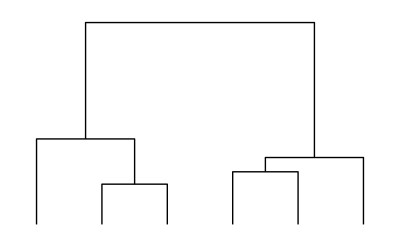

```mathematica
DendrogramPlot[a1]
```

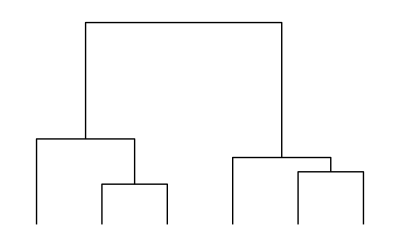

```mathematica
DendrogramPlot[a2]
```

### 演習

任意に3グループ以上(各グループは30以上のメンバー、2次元以上のデータ)のデータを発生させ、

1. 複数の条件やアルゴリズムで非階層クラスタリングを行ない(可能なら何らかの評価指標でそれぞれ評価せよ)、クラスターごとに異なる色でplotせよ。

2. また、複数の条件やアルゴリズムで階層クラスタリングを行ないデンドログラムをplotせよ。

```mathematica
(*Needs["HierarchicalClustering`"]*)
```

```mathematica
data1=RandomVariate[NormalDistribution[],{50,2}];
```

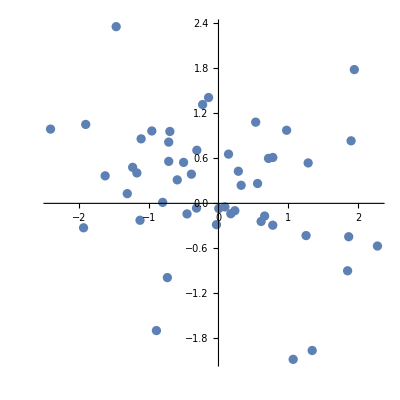

```mathematica
ListPlot[data1,AspectRatio->1]
```

```mathematica
hcl1=Agglomerate[data1];
```

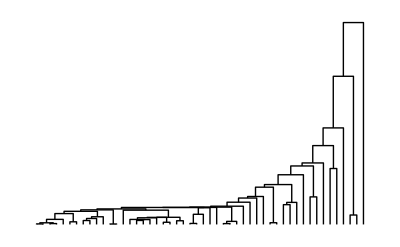

```mathematica
DendrogramPlot[hcl1]
```

### 提出課題(6)

提出課題(5)で取得したデータに対して、適切な階層クラスタリングを行ない、デンドログラムをプロットせよ。

## 8.自己組織化マップ*

機械学習によりデータ間の関係からより大きな構造を見抜く。

機械学習にはさまざまなものがあるが、ここでは自己組織化(SOM)の基本的技術であるニューラルネットワークを学ぶ。

### ニューラルネットワーク*

#### ニューロン

実際のニューロン(wikipediaから抜粋):

神経細胞の構造

樹状突起: 外部や他の細胞からの刺激を受け取る

軸索: 刺激を他の細胞に伝える

細胞体: 核を保有する細胞本体

シナプス: 軸索と樹状突起の接合部、伝達する側からは神経伝達物質が放出される、伝達される側は神経伝達物質のレセプターを持つ

神経伝達のしくみ

前シナプス細胞(シグナルを伝える細胞)の軸索を活動電位(インパルス)が伝わり、末端にある膨らみであるシナプス小頭に到達する

活動電位によりシナプス小頭の膜上に位置する電位依存性カルシウムイオンチャネルが開く

するとカルシウムイオンがシナプス内に流入し、シナプス小胞が細胞膜に接して神経伝達物質が細胞外に開口放出される

神経伝達物質はシナプス間隙を拡散し、後シナプス細胞の細胞膜上に分布する神経伝達物質受容体に結合する

後シナプス細胞(シグナルを伝えられる細胞)のイオンチャネルが開き、細胞膜内外の電位差が変化する

膜に機械的、化学的、電気的刺激を受けると、膜は脱分極を起こす。約15mV程の変化、すなわち、細胞内が細胞外に比べ-55mV程になるまで脱分極すると、膜のナトリウム透過性が急激に高まり、細胞の内外の電位が逆転する（約35mV)。これを活動電位という

軸索を通じ他の細胞に刺激を伝える(興奮する)かは、同時に受け取った刺激の総和が細胞のもつしきい値を越えるかによる

活動電位が生じた部位では次にカリウムイオンが流出し、ナトリウムイオンを能動輸送によって細胞外に排出する。その結果膜の電位は一時的に-70mVよりも下がって（過分極）から静止電位に戻る。脱分極期はあらたに脱分極が起こることがないので、絶対不応期であり、過分極期は脱分極を起こしにくい状態になるので相対不応期である。そのため、一度興奮が起きた後、次の興奮が起きるまで３m秒程の不応期があることになる

活動電位が生じた部分の隣接部では軽い脱分極が起こり、新しい活動電位を生じる。これによって、興奮は次々と伝達される。これをインパルスと呼ぶ

このインパルスが軸索に到達すると、そのインパルスは軸索末端にまで到達する

神経伝達の種類

興奮性: 興奮性シナプスは信号を受け取ると、興奮性シナプス後電位（EPSP; Excitatory PostSynaptic Potential）という信号を発生させる。EPSPは神経細胞の分極状態が崩れる電位となるため、脱分極と呼ばれる。興奮性の神経伝達物質として、アセチルコリン、グルタミン酸、ノルエピネフリンなどがある。

抑制性:抑制性シナプスは信号を受け取ると、抑制性シナプス後電位（IPSP; Inhibitory PostSynaptic Potential）という信号を発生させる。IPSPは神経細胞の分極状態が強化される電位となるため、過分極と呼ばれる。抑制性の神経伝達物質にはGABA、グリシンなどがある。

シナプス前抑制性: 興奮性シナプスが起こす興奮性シナプス後電位（EPSP）を減少させる働きを持つ。

電気シナプス: 電気シナプスとは、細胞間がイオンなどを通過させる分子で接着され、細胞間に直接イオン電流が流れることによって細胞間のシグナル伝達が行われるシナプスのことを指す。化学シナプスのように方向づけられた伝達はできないが、それよりも高速な伝達が行われ、多くの細胞が協調して動作する現象を引き起こす。

計算機におけるニューロン: 実際のニューロンを忠実に真似る必要はなく自由に設計できる:

加算器

```mathematica
adder[o_List,w_List]:=Tr[w*o]
```

```mathematica
adder[{1,2,3},{a,b,c}]
```

a+2 b+3 c

入出力関数 -シグモイド関数-

```mathematica
SGM[a_,th_]:=1/(1+E^(-a+th))
```

```mathematica
Plot3D[SGM[in,th],{in,-5,5},{th,0,1},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Plot3D[SGM[in,th],{in,-1,1},{th,0,1},AxesLabel->Automatic]
```

-Graphics3D-

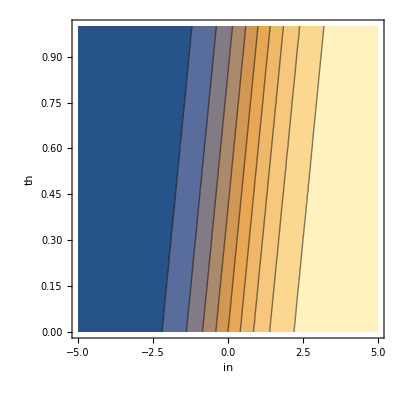

```mathematica
ContourPlot[SGM[in,th],{in,-5,5},{th,0,1},AxesLabel->Automatic]
```

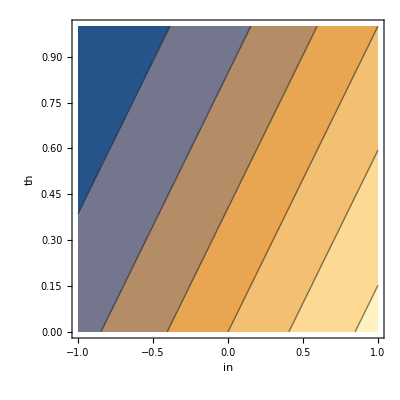

```mathematica
ContourPlot[SGM[in,th],{in,-1,1},{th,0,1},AxesLabel->Automatic]
```

ニューロンの設計

```mathematica
NER[o_List,w_List,iofunc_,th_]:=If[iofunc[adder[o,w],th]>=th,1,0]
```

```mathematica
NER[1][o_List,w_List,iofunc_,th_]:=If[iofunc[adder[o,w],th]>=th,1,0]
```

```mathematica
NER[0][o_List,w_List,iofunc_,th_]:=If[iofunc[adder[o,w],0]>=th,1,0]
```

```mathematica
ner[o_List,w_List,iofunc_,th_]:=iofunc[adder[o,w],th]
```

加算器と入出力関数(iofunc)を組み合わせニューロンを作る。
入出力関数(iofunc)は、いま、シグモイド(0 < SGM < 1)に定義されている。
かつ、ニューロン(NER)は、非線形活性化関数として機能している。
しきい値 th は、iofunc() そのものにも影響するかたちになっている。

設計したニューロンの性質:

入力を{1,1,1}、重みを{1,1,1}とする。

当然ながら、thに1より大きい値を設定すると、ニューロンの出力は、かならず 0。

```mathematica
Table[{NER[{1,1,1},{1,1,1},SGM,th],th},{th,-0.2,1.2,0.1}]//TableForm
```

1 | -0.2
1 | -0.1
1 | 0.
1 | 0.1
1 | 0.2
1 | 0.3
1 | 0.4
1 | 0.5
1 | 0.6
1 | 0.7
1 | 0.8
0 | 0.9
0 | 1.
0 | 1.1
0 | 1.2

重みが負になっても 0。

```mathematica
Table[{NER[{1,1,1},{-1,-1,-1},SGM,th],th},{th,-0.2,1.2,0.1}]//TableForm
```

1 | -0.2
1 | -0.1
1 | 0.
0 | 0.1
0 | 0.2
0 | 0.3
0 | 0.4
0 | 0.5
0 | 0.6
0 | 0.7
0 | 0.8
0 | 0.9
0 | 1.
0 | 1.1
0 | 1.2

当然ながら、thに0より小さい値を設定すると、ニューロンの出力は、かならず 1。

```mathematica
Table[{NER[{1,1,1},{1,1,1},SGM,th],th},{th,-0.2,1.2,0.1}]//TableForm
```

1 | -0.2
1 | -0.1
1 | 0.
1 | 0.1
1 | 0.2
1 | 0.3
1 | 0.4
1 | 0.5
1 | 0.6
1 | 0.7
1 | 0.8
0 | 0.9
0 | 1.
0 | 1.1
0 | 1.2

重みが負になっても 1。

```mathematica
Table[{NER[{1,1,1},{-1,-1,-1},SGM,th],th},{th,-0.2,1.2,0.1}]//TableForm
```

1 | -0.2
1 | -0.1
1 | 0.
0 | 0.1
0 | 0.2
0 | 0.3
0 | 0.4
0 | 0.5
0 | 0.6
0 | 0.7
0 | 0.8
0 | 0.9
0 | 1.
0 | 1.1
0 | 1.2

次に、重みをすべて負の値とし、thを0 <= th <= 1の間で変化させる。thが0の場合のみ、ニューロンの出力は1。

```mathematica
Table[{NER[{1,1,1},{-1,-1,-1},SGM,th],th},{th,0,1,0.1}]//TableForm
```

1 | 0.
0 | 0.1
0 | 0.2
0 | 0.3
0 | 0.4
0 | 0.5
0 | 0.6
0 | 0.7
0 | 0.8
0 | 0.9
0 | 1.

重みをすべて1とし、thを0 <= th <= 1の間で変化させる。thが0.85を越えたあたりから、ニューロンの出力は0。

```mathematica
Table[{NER[{1,1,1},{1,1,1},SGM,th],th},{th,0,1,0.05}]//TableForm
```

1 | 0.
1 | 0.05
1 | 0.1
1 | 0.15
1 | 0.2
1 | 0.25
1 | 0.3
1 | 0.35
1 | 0.4
1 | 0.45
1 | 0.5
1 | 0.55
1 | 0.6
1 | 0.65
1 | 0.7
1 | 0.75
1 | 0.8
1 | 0.85
0 | 0.9
0 | 0.95
0 | 1.

重みを適当な値にすれば、thを0 <= th <= 1の間でニューロンの出力が決まる。

```mathematica
Table[{NER[{1,0,1},{0.,0.,0.},SGM,th],th},{th,0,1,0.1}]//TableForm
```

1 | 0.
1 | 0.1
1 | 0.2
1 | 0.3
1 | 0.4
0 | 0.5
0 | 0.6
0 | 0.7
0 | 0.8
0 | 0.9
0 | 1.

```mathematica
Table[{NER[{1,0,1},{0,0,1},SGM,th],th},{th,0,1,0.1}]//TableForm
```

1 | 0.
1 | 0.1
1 | 0.2
1 | 0.3
1 | 0.4
1 | 0.5
0 | 0.6
0 | 0.7
0 | 0.8
0 | 0.9
0 | 1.

#### 教師あり学習*

ニューラルネットワークの簡単な例:

-Graphics-

学習データ: {<入力ベクトル>,<期待される出力>}

```mathematica
ldata1={
{{0,0},0},
{{1,0},0},
{{0,1},0},
{{1,1},1}
}
```

{{{0,0},0},{{1,0},0},{{0,1},0},{{1,1},1}}

```mathematica
TableForm[Map[Flatten[#]&,ldata1],TableHeadings->{Table[n,{n,4}],{"入力１","入力２","出力(期待)"}}]
```

| 入力１ | 入力２ | 出力(期待)
1 | 0 | 0 | 0
2 | 1 | 0 | 0
3 | 0 | 1 | 0
4 | 1 | 1 | 1

重みベクトル、しきい値の初期値

```mathematica
wdata[0]={1.5,-1.0}
```

{1.5,-1.}

```mathematica
thh[0]=0.8
```

0.8

```mathematica
NER[ldata1[[1,1]],wdata[0],SGM,thh[0]]
```

0

```mathematica
NER[ldata1[[2,1]],wdata[0],SGM,thh[0]]
```

0

```mathematica
NER[ldata1[[3,1]],wdata[0],SGM,thh[0]]
```

0

```mathematica
NER[ldata1[[4,1]],wdata[0],SGM,thh[0]]
```

0

上の例では、パターン4のときに期待する値が得られていない。

学習:*学習部分加筆

重みとしきい値を変化させ、学習をおこなう。

しきい値を小さくすれば、出力は大きくなる。

```mathematica
delta=.
```

```mathematica
thh[0]
```

0.8

```mathematica
ner[ldata1[[4,1]],wdata[0],SGM,thh[0]]
```

0.425557

```mathematica
delta[1]=ner[ldata1[[4,1]],wdata[0],SGM,thh[0]]-thh[0]
```

-0.374443

```mathematica
NER[ldata1[[4,1]],wdata[0],SGM,thh[0]+delta[1]]
```

1

入力に対応する重みを大きくすれば、出力は大きくなる。

```mathematica
wdata[0]
```

{1.5,-1.}

```mathematica
NER[ldata1[[4,1]],wdata[0]+0.5*ldata1[[4,1]],SGM,thh[0]]
```

0

```mathematica
NER[ldata1[[4,1]],wdata[0]+(0.5+0.5)*ldata1[[4,1]],SGM,thh[0]]
```

1

入力がない場合、しきい値を変化させ、入力がある場合、それに対応する重みを変化させることによって学習を行う。どの程度変化させるか -> デルタルールなど。

```mathematica
NER[ldata1[[4,1]],{1,1},SGM,0.6](*1*)
```

1

```mathematica
NER[ldata1[[3,1]],{1,1},SGM,0.6](*0*)
```

0

```mathematica
NER[ldata1[[2,1]],{1,1},SGM,0.6](*0*)
```

0

```mathematica
NER[ldata1[[1,1]],{1,1},SGM,0.6](*0*)
```

0

#### 分類機械と競合学習

分類機械:入力のパターンを出力の個数に分類する。出力の受ける入力の重みの総和は1。

-Graphics-

∑ w_i,1 = 1 ; ∑ w_i,2 = 1

競合学習の手順:

重みの初期値:

```mathematica
wmat[0]={
{0.5,0.5},
{0.6,0.4}
}
```

{{0.5,0.5},{0.6,0.4}}

```mathematica
TableForm[wmat[0],TableHeadings->{{"出力1","出力2"},{"入力1","入力2"}}]
```

| 入力1 | 入力2
出力1 | 0.5 | 0.5
出力2 | 0.6 | 0.4

入力パターン:

```mathematica
pdata1={
{1,0},
{0,1},
{1,1},
{1,0}
}
```

{{1,0},{0,1},{1,1},{1,0}}

```mathematica
TableForm[pdata1,TableHeadings->{Table[i,{i,4}],{"入力1","入力2"}}]
```

| 入力1 | 入力2
1 | 1 | 0
2 | 0 | 1
3 | 1 | 1
4 | 1 | 0

勝者に対する重みの変化量:
dw = l (c/n - w) ; l : 学習率、c : 入力値、n : 入力数、w : 現在の重み

学習係数 lを0.5に。

```mathematica
l=0.5
```

0.5

入力パターン1に対して学習:

入力パターン1の場合の出力1:

```mathematica
pdata1[[1]] wmat[0][[1]]//Tr
```

0.5

入力パターン1の場合の出力2:

```mathematica
pdata1[[1]] wmat[0][[2]]//Tr
```

0.6

出力2が勝者となる

そこで、w_2,1とw_2,2(下表)を変化させる。

| 入力1 | 入力2
出力1 | 0.5 | 0.5
出力2 | 0.6 | 0.4

```mathematica
dw[1][1,1]=0
```

0

```mathematica
dw[1][1,2]=0
```

0

まず、wd_2,1(出力2入力1)

pdata1[[1,1]] : パターン1:入力1
Tr[pdata1[[1]]] : パターン1:出力2への入力数
wmat[0][[2,1]] : パターン1:出力2、入力1のとき

```mathematica
dw[1][2,1]=l(pdata1[[1,1]]/Tr[pdata1[[1]]]-wmat[0][[2,1]])
```

0.2

つぎに、wd_2,2(出力2入力2)

pdata1[[1,2]] : パターン1:入力2
Tr[pdata1[[1]]] : パターン1:出力2への入力数
wmat[0][[2,2]] : パターン1:出力2、入力2のとき

```mathematica
dw[1][2,2]=l(pdata1[[1,2]]/Tr[pdata1[[1]]]-wmat[0][[2,2]])
```

-0.2

重みを更新:

```mathematica
wmat[0]
```

{{0.5,0.5},{0.6,0.4}}

```mathematica
wmat[1]=wmat[0]+{{dw[1][1,1],dw[1][1,2]},{dw[1][2,1],dw[1][2,2]}}
```

{{0.5,0.5},{0.8,0.2}}

```mathematica
TableForm[wmat[1],TableHeadings->{{"出力1","出力2"},{"入力1","入力2"}}]
```

| 入力1 | 入力2
出力1 | 0.5 | 0.5
出力2 | 0.8 | 0.2

入力パターン2に対して学習:

入力パターン2の場合の出力1:

```mathematica
pdata1[[2]] wmat[1][[1]]//Tr
```

0.5

入力パターン1の場合の出力2:

```mathematica
pdata1[[2]] wmat[1][[2]]//Tr
```

0.2

出力1が勝者となる

そこで、w_1,1とw_1,2を変化させる。

| 入力1 | 入力2
出力1 | 0.5 | 0.5
出力2 | 0.8 | 0.2

```mathematica
dw[2][2,1]=0
```

0

```mathematica
dw[2][2,2]=0
```

0

まず、wd_1,1(出力1入力1)

pdata1[[2,1]] : パターン2:入力1
Tr[pdata1[[2]]] : パターン2:出力1への入力数
wmat[1][[1,1]] : パターン2:出力1、入力1のとき

```mathematica
dw[2][1,1]=l(pdata1[[2,1]]/Tr[pdata1[[2]]]-wmat[1][[1,1]])
```

-0.25

つぎに、wd_1,2(出力1入力2)

pdata1[[2,2]] : パターン2:入力2
Tr[pdata1[[2]]] : パターン2:出力1への入力数
wmat[1][[1,2]] : パターン2:出力1、入力2のとき

```mathematica
dw[2][1,2]=l(pdata1[[2,2]]/Tr[pdata1[[2]]]-wmat[1][[1,2]])
```

0.25

重みを更新:

```mathematica
wmat[1]
```

{{0.5,0.5},{0.8,0.2}}

```mathematica
wmat[2]=wmat[1]+{{dw[2][1,1],dw[2][1,2]},{dw[2][2,1],dw[2][2,2]}}
```

{{0.25,0.75},{0.8,0.2}}

```mathematica
TableForm[wmat[2],TableHeadings->{{"出力1","出力2"},{"入力1","入力2"}}]
```

| 入力1 | 入力2
出力1 | 0.25 | 0.75
出力2 | 0.8 | 0.2

入力パターン3に対して学習:

入力パターン3の場合の出力1:

```mathematica
pdata1[[3]] wmat[2][[1]]//Tr
```

1.

入力パターン3の場合の出力2:

```mathematica
pdata1[[3]] wmat[2][[2]]//Tr
```

1.

双方を勝者として学習させる。

そこで、w_1,1とw_1,2、w_2,1とw_2,2を変化させる。

| 入力1 | 入力2
出力1 | 0.5 | 0.5
出力2 | 0.8 | 0.2

まず、wd_1,1(出力1入力1)

pdata1[[3,1]] : パターン3:入力1
Tr[pdata1[[3]]] : パターン3:出力1への入力数
wmat[2][[1,1]] : パターン3:出力1、入力1のとき

```mathematica
dw[3][1,1]=l(pdata1[[3,1]]/Tr[pdata1[[3]]]-wmat[2][[1,1]])
```

0.125

つぎに、wd_1,2(出力1入力2)

pdata1[[3,2]] : パターン3:入力2
Tr[pdata1[[3]]] : パターン3:出力1への入力数
wmat[2][[1,2]] : パターン3:出力1、入力2のとき

```mathematica
dw[3][1,2]=l(pdata1[[3,2]]/Tr[pdata1[[3]]]-wmat[2][[1,2]])
```

-0.125

つぎに、wd_2,1(出力2入力1)

pdata1[[3,1]] : パターン3:入力1
Tr[pdata1[[3]]] : パターン3:出力2への入力数
wmat[2][[2,1]] : パターン3:出力2、入力1のとき

```mathematica
dw[3][2,1]=l(pdata1[[3,1]]/Tr[pdata1[[3]]]-wmat[2][[2,1]])
```

-0.15

つぎに、wd_2,2(出力2入力2)

pdata1[[3,2]] : パターン3:入力2
Tr[pdata1[[3]]] : パターン3:出力2への入力数
wmat[2][[2,2]] : パターン3:出力2、入力2のとき

```mathematica
dw[3][2,2]=l(pdata1[[3,2]]/Tr[pdata1[[3]]]-wmat[2][[2,2]])
```

0.15

重みを更新:

```mathematica
wmat[2]
```

{{0.25,0.75},{0.8,0.2}}

```mathematica
wmat[3]=wmat[2]+{{dw[3][1,1],dw[3][1,2]},{dw[3][2,1],dw[3][2,2]}}
```

{{0.375,0.625},{0.65,0.35}}

```mathematica
TableForm[wmat[3],TableHeadings->{{"出力1","出力2"},{"入力1","入力2"}}]
```

| 入力1 | 入力2
出力1 | 0.375 | 0.625
出力2 | 0.65 | 0.35

入力パターン4に対して学習:

入力パターン4の場合の出力1:

```mathematica
pdata1[[4]] wmat[3][[1]]//Tr
```

0.375

入力パターン4の場合の出力2:

```mathematica
pdata1[[4]] wmat[3][[2]]//Tr
```

0.65

出力2が勝者となる。

| 入力1 | 入力2
出力1 | 0.375 | 0.625
出力2 | 0.65 | 0.35

そこで、w_2,1とw_2,2を変化させる。

```mathematica
dw[4][1,1]=0
```

0

```mathematica
dw[4][1,2]=0
```

0

まず、wd_2,1(出力2入力1)

pdata1[[4,1]] : パターン4:入力1
Tr[pdata1[[4]]] : パターン4:出力2への入力数
wmat[3][[2,1]] : パターン4:出力2、入力1のとき

```mathematica
dw[4][2,1]=l(pdata1[[4,1]]/Tr[pdata1[[4]]]-wmat[3][[2,1]])
```

0.175

つぎに、wd_2,2(出力2入力2)

pdata1[[4,2]] : パターン4:入力2
Tr[pdata1[[4]]] : パターン4:出力2への入力数
wmat[3][[2,2]] : パターン4:出力2、入力2のとき

```mathematica
dw[4][2,2]=l(pdata1[[4,2]]/Tr[pdata1[[4]]]-wmat[3][[2,2]])
```

-0.175

重みを更新:

```mathematica
wmat[3]
```

{{0.375,0.625},{0.65,0.35}}

```mathematica
wmat[4]=wmat[3]+{{dw[4][1,1],dw[4][1,2]},{dw[4][2,1],dw[4][2,2]}}
```

{{0.375,0.625},{0.825,0.175}}

```mathematica
TableForm[wmat[4],TableHeadings->{{"出力1","出力2"},{"入力1","入力2"}}]
```

| 入力1 | 入力2
出力1 | 0.375 | 0.625
出力2 | 0.825 | 0.175

学習後、分類機械として利用:

パターン1:

```mathematica
pdata1[[1]] wmat[4][[1]]//Tr
```

0.375

```mathematica
pdata1[[1]] wmat[4][[2]]//Tr
```

0.825

パターン2:

```mathematica
pdata1[[2]] wmat[4][[1]]//Tr
```

0.625

```mathematica
pdata1[[2]] wmat[4][[2]]//Tr
```

0.175

パターン3:

```mathematica
pdata1[[3]] wmat[4][[1]]//Tr
```

1.

```mathematica
pdata1[[3]] wmat[4][[2]]//Tr
```

1.

パターン4:

```mathematica
pdata1[[4]] wmat[4][[1]]//Tr
```

0.375

```mathematica
pdata1[[4]] wmat[4][[2]]//Tr
```

0.825

#### ニューラルネットワーク

ニューラルネットワークとは、ニューロンおよびその学習の仕組みを、多階層的に組み合わせたもの。

計算機におけるニューラルネットワーク: 実際のニューラルネットワークを忠実に真似る必要はなく自由に設計できる:

実際には、良く知られている問題以外に対応するネットワーク設計は計算量の問題もあり難しい(->Deep Learning)。

設計と解法:

情報理論に基づくフィードバックモデルの作成 -> 連立常微分方程式(ODE)の定義 -> ODEを解く
常微分方程式を定義したのちに、Maple、Mathematica、Spiceなどを使う。

ネットワークモデルを直接作成する
Mathematica、Rなどに設計ツールが実装されている(Mathematicaは、さらに別パッケージを購入する必要がある)。前述の繰り返し学習による解法の実装。

#### 自己組織化マップ

自己組織化マップとは、ニューラルネットワークの一種。マップ空間(一般的に2-3次元)のニューロンは入力空間およびマップ空間双方の属性(値)を持ち、事実上の写像が行なわれる。

http://www.brain.kyutech.ac.jp/~furukawa/note/som/som.html#2

スライド: 知識構造化法_天野加筆9-2.pptx

## 9.主成分分析と数量化III類・IV類*

データの見方を変える。

### 分散共分散

ベクトルaを仮定

```mathematica
Array[a,{3}]
```

{a[1],a[2],a[3]}

Mathematicaによる分散の計算：

```mathematica
Variance[Array[a,{3}]]
```

1/6 ((2 a[1]-a[2]-a[3]) Conjugate[a[1]]+(-a[1]+2 a[2]-a[3]) Conjugate[a[2]]+(-a[1]-a[2]+2 a[3]) Conjugate[a[3]])

分散(ベクトルaのドメインをRealに限定、ただし処理としてはインチキ)：

```mathematica
(Variance[Array[a,{3}]]//Expand)/.Conjugate[x_]->x
```

a[1]^2/3-1/3 a[1] a[2]+a[2]^2/3-1/3 a[1] a[3]-1/3 a[2] a[3]+a[3]^2/3

```mathematica
cov[0][x_,y_]:=Module[{mx,my},
mx=Mean[x];
my=Mean[y];
Tr[Map[#-mx&,x]*Map[#-my&,y]]/(Length[x])
]
```

```mathematica
cov[1][x_,y_]:=Module[{mx,my},
mx=Mean[x];
my=Mean[y];
Tr[Map[#-mx&,x]*Map[#-my&,y]]/(Length[x]-1)
]
```

```mathematica
vcov[0][l_]:=Outer[cov[0],l,l,1]
```

```mathematica
vcov[1][l_]:=Outer[cov[1],l,l,1]
```

```mathematica
l={{3,2},{3,4},{1,2}}
```

{{3,2},{3,4},{1,2}}

```mathematica
vcov[0][l]
```

{{1/4,-1/4,-1/4},{-1/4,1/4,1/4},{-1/4,1/4,1/4}}

確認：Mathematicaでは(n-1)で割っている。

```mathematica
cov[0][Array[a,{3}],Array[a,{3}]]//Simplify
```

2/9 (a[1]^2+a[2]^2-a[2] a[3]+a[3]^2-a[1] (a[2]+a[3]))

```mathematica
cov[1][Array[a,{3}],Array[a,{3}]]//Simplify
```

1/3 (a[1]^2+a[2]^2-a[2] a[3]+a[3]^2-a[1] (a[2]+a[3]))

```mathematica
Covariance[Array[a,3],Array[a,3]]/.Conjugate[x_]->x//Simplify
```

1/3 (a[1]^2+a[2]^2-a[2] a[3]+a[3]^2-a[1] (a[2]+a[3]))

```mathematica
??Covariance
```

Covariance[v_1,v_2] ベクトル v_1と v_2の間の共分散を返す．
Covariance[m] 行列 m の共分散行列を返す．
Covariance[m_1,m_2] 行列 m_1と m_2の共分散行列を返す．
Covariance[dist] 多変量記号分布 dist の共分散行列を返す．
Covariance[dist,i,j] 多変量記号分布 dist の(i,j)次共分散を返す．

Attributes[Covariance]={Protected,ReadProtected}
 
Options[Covariance]={}

実際のベクトルの例

```mathematica
x1={1,2,3,4}
x2={2,3,4,6}
```

{1,2,3,4}

{2,3,4,6}

```mathematica
Covariance[x1,x1]
```

13/6

```mathematica
Covariance[x1,x2]
```

13/6

```mathematica
Covariance[Transpose[{x1,x2}]]
```

{{5/3,13/6},{13/6,35/12}}

分散共分散：

```mathematica
Covariance[Array[a,{3,3}]]//MatrixForm
```

(1/6 ((2 a[1,1]-a[2,1]-a[3,1]) Conjugate[a[1,1]]+(-a[1,1]+2 a[2,1]-a[3,1]) Conjugate[a[2,1]]+(-a[1,1]-a[2,1]+2 a[3,1]) Conjugate[a[3,1]]) | 1/6 ((2 a[1,1]-a[2,1]-a[3,1]) Conjugate[a[1,2]]+(-a[1,1]+2 a[2,1]-a[3,1]) Conjugate[a[2,2]]+(-a[1,1]-a[2,1]+2 a[3,1]) Conjugate[a[3,2]]) | 1/6 ((2 a[1,1]-a[2,1]-a[3,1]) Conjugate[a[1,3]]+(-a[1,1]+2 a[2,1]-a[3,1]) Conjugate[a[2,3]]+(-a[1,1]-a[2,1]+2 a[3,1]) Conjugate[a[3,3]])
1/6 ((2 a[1,2]-a[2,2]-a[3,2]) Conjugate[a[1,1]]+(-a[1,2]+2 a[2,2]-a[3,2]) Conjugate[a[2,1]]+(-a[1,2]-a[2,2]+2 a[3,2]) Conjugate[a[3,1]]) | 1/6 ((2 a[1,2]-a[2,2]-a[3,2]) Conjugate[a[1,2]]+(-a[1,2]+2 a[2,2]-a[3,2]) Conjugate[a[2,2]]+(-a[1,2]-a[2,2]+2 a[3,2]) Conjugate[a[3,2]]) | 1/6 ((2 a[1,2]-a[2,2]-a[3,2]) Conjugate[a[1,3]]+(-a[1,2]+2 a[2,2]-a[3,2]) Conjugate[a[2,3]]+(-a[1,2]-a[2,2]+2 a[3,2]) Conjugate[a[3,3]])
1/6 ((2 a[1,3]-a[2,3]-a[3,3]) Conjugate[a[1,1]]+(-a[1,3]+2 a[2,3]-a[3,3]) Conjugate[a[2,1]]+(-a[1,3]-a[2,3]+2 a[3,3]) Conjugate[a[3,1]]) | 1/6 ((2 a[1,3]-a[2,3]-a[3,3]) Conjugate[a[1,2]]+(-a[1,3]+2 a[2,3]-a[3,3]) Conjugate[a[2,2]]+(-a[1,3]-a[2,3]+2 a[3,3]) Conjugate[a[3,2]]) | 1/6 ((2 a[1,3]-a[2,3]-a[3,3]) Conjugate[a[1,3]]+(-a[1,3]+2 a[2,3]-a[3,3]) Conjugate[a[2,3]]+(-a[1,3]-a[2,3]+2 a[3,3]) Conjugate[a[3,3]]))

```mathematica
Covariance[Array[a,{3,3}]]/.Conjugate[x_]->x//MatrixForm
```

(1/6 (a[1,1] (2 a[1,1]-a[2,1]-a[3,1])+a[2,1] (-a[1,1]+2 a[2,1]-a[3,1])+a[3,1] (-a[1,1]-a[2,1]+2 a[3,1])) | 1/6 (a[1,2] (2 a[1,1]-a[2,1]-a[3,1])+a[2,2] (-a[1,1]+2 a[2,1]-a[3,1])+(-a[1,1]-a[2,1]+2 a[3,1]) a[3,2]) | 1/6 (a[1,3] (2 a[1,1]-a[2,1]-a[3,1])+a[2,3] (-a[1,1]+2 a[2,1]-a[3,1])+(-a[1,1]-a[2,1]+2 a[3,1]) a[3,3])
1/6 (a[1,1] (2 a[1,2]-a[2,2]-a[3,2])+a[2,1] (-a[1,2]+2 a[2,2]-a[3,2])+a[3,1] (-a[1,2]-a[2,2]+2 a[3,2])) | 1/6 (a[1,2] (2 a[1,2]-a[2,2]-a[3,2])+a[2,2] (-a[1,2]+2 a[2,2]-a[3,2])+a[3,2] (-a[1,2]-a[2,2]+2 a[3,2])) | 1/6 (a[1,3] (2 a[1,2]-a[2,2]-a[3,2])+a[2,3] (-a[1,2]+2 a[2,2]-a[3,2])+(-a[1,2]-a[2,2]+2 a[3,2]) a[3,3])
1/6 (a[1,1] (2 a[1,3]-a[2,3]-a[3,3])+a[2,1] (-a[1,3]+2 a[2,3]-a[3,3])+a[3,1] (-a[1,3]-a[2,3]+2 a[3,3])) | 1/6 (a[1,2] (2 a[1,3]-a[2,3]-a[3,3])+a[2,2] (-a[1,3]+2 a[2,3]-a[3,3])+a[3,2] (-a[1,3]-a[2,3]+2 a[3,3])) | 1/6 (a[1,3] (2 a[1,3]-a[2,3]-a[3,3])+a[2,3] (-a[1,3]+2 a[2,3]-a[3,3])+a[3,3] (-a[1,3]-a[2,3]+2 a[3,3])))

### 主成分分析(PCA)

#### PCAの概念的理解(黒板)

もっとも簡単な方法は、分散共分散行列に対する固有ベクトルを求める(分散共分散法):

```mathematica
Eigenvectors[Covariance[{{1,1},{-1,-1}}]]//TableForm
```

1 | 1
-1 | 1

ただし、サンプル間の相対的な距離が保たれない(原点からのノルムが保たれる)。

Mathematicaではサンプル間の相対的な距離を保つPCAが行なわれる。これによりサンプルの重心が原点となる:

```mathematica
PrincipalComponents[{{1,1},{-1,-1}}]//TableForm
```

√2 | 0
-√2 | 0

```mathematica
Eigenvectors[Covariance[Array[a, {2, 2}]]]//TableForm
```

-(Conjugate[a[1,2]]-Conjugate[a[2,2]])/(Conjugate[a[1,1]]-Conjugate[a[2,1]]) | 1
-(-a[1,1]+a[2,1])/(a[1,2]-a[2,2]) | 1

実際には、さまざまな調整を含むより複雑なアルゴリズムが使われる。 -> 論文には使用したソフトウエア、バージョン、パッケージ名を記載する。

```mathematica
PrincipalComponents[Array[a,{2,2}]]//TableForm
```

((a[1,2]+1/2 (-a[1,2]-a[2,2])-((a[1,1]+1/2 (-a[1,1]-a[2,1])) (-Conjugate[a[1,1]]+1/2 Conjugate[a[1,1]+a[2,1]]+Conjugate[1/2 (-a[1,1]-a[2,1])+a[2,1]]))/(Conjugate[a[1,2]+1/2 (-a[1,2]-a[2,2])]-Conjugate[a[2,2]]+1/2 Conjugate[a[1,2]+a[2,2]])) √(a[1,1] Conjugate[a[1,1]+1/2 (-a[1,1]-a[2,1])]-a[2,1] Conjugate[a[1,1]+1/2 (-a[1,1]-a[2,1])]-a[1,1] Conjugate[1/2 (-a[1,1]-a[2,1])+a[2,1]]+a[2,1] Conjugate[1/2 (-a[1,1]-a[2,1])+a[2,1]]+a[1,2] Conjugate[a[1,2]+1/2 (-a[1,2]-a[2,2])]-a[2,2] Conjugate[a[1,2]+1/2 (-a[1,2]-a[2,2])]-a[1,2] Conjugate[1/2 (-a[1,2]-a[2,2])+a[2,2]]+a[2,2] Conjugate[1/2 (-a[1,2]-a[2,2])+a[2,2]]))/(√2 √(Abs[a[1,2]+1/2 (-a[1,2]-a[2,2])-((a[1,1]+1/2 (-a[1,1]-a[2,1])) (-Conjugate[a[1,1]]+1/2 Conjugate[a[1,1]+a[2,1]]+Conjugate[1/2 (-a[1,1]-a[2,1])+a[2,1]]))/(Conjugate[a[1,2]+1/2 (-a[1,2]-a[2,2])]-Conjugate[a[2,2]]+1/2 Conjugate[a[1,2]+a[2,2]])]^2+Abs[1/2 (-a[1,2]-a[2,2])+a[2,2]-((1/2 (-a[1,1]-a[2,1])+a[2,1]) (-Conjugate[a[1,1]]+1/2 Conjugate[a[1,1]+a[2,1]]+Conjugate[1/2 (-a[1,1]-a[2,1])+a[2,1]]))/(Conjugate[a[1,2]+1/2 (-a[1,2]-a[2,2])]-Conjugate[a[2,2]]+1/2 Conjugate[a[1,2]+a[2,2]])]^2)) | 0
((1/2 (-a[1,2]-a[2,2])+a[2,2]-((1/2 (-a[1,1]-a[2,1])+a[2,1]) (-Conjugate[a[1,1]]+1/2 Conjugate[a[1,1]+a[2,1]]+Conjugate[1/2 (-a[1,1]-a[2,1])+a[2,1]]))/(Conjugate[a[1,2]+1/2 (-a[1,2]-a[2,2])]-Conjugate[a[2,2]]+1/2 Conjugate[a[1,2]+a[2,2]])) √(a[1,1] Conjugate[a[1,1]+1/2 (-a[1,1]-a[2,1])]-a[2,1] Conjugate[a[1,1]+1/2 (-a[1,1]-a[2,1])]-a[1,1] Conjugate[1/2 (-a[1,1]-a[2,1])+a[2,1]]+a[2,1] Conjugate[1/2 (-a[1,1]-a[2,1])+a[2,1]]+a[1,2] Conjugate[a[1,2]+1/2 (-a[1,2]-a[2,2])]-a[2,2] Conjugate[a[1,2]+1/2 (-a[1,2]-a[2,2])]-a[1,2] Conjugate[1/2 (-a[1,2]-a[2,2])+a[2,2]]+a[2,2] Conjugate[1/2 (-a[1,2]-a[2,2])+a[2,2]]))/(√2 √(Abs[a[1,2]+1/2 (-a[1,2]-a[2,2])-((a[1,1]+1/2 (-a[1,1]-a[2,1])) (-Conjugate[a[1,1]]+1/2 Conjugate[a[1,1]+a[2,1]]+Conjugate[1/2 (-a[1,1]-a[2,1])+a[2,1]]))/(Conjugate[a[1,2]+1/2 (-a[1,2]-a[2,2])]-Conjugate[a[2,2]]+1/2 Conjugate[a[1,2]+a[2,2]])]^2+Abs[1/2 (-a[1,2]-a[2,2])+a[2,2]-((1/2 (-a[1,1]-a[2,1])+a[2,1]) (-Conjugate[a[1,1]]+1/2 Conjugate[a[1,1]+a[2,1]]+Conjugate[1/2 (-a[1,1]-a[2,1])+a[2,1]]))/(Conjugate[a[1,2]+1/2 (-a[1,2]-a[2,2])]-Conjugate[a[2,2]]+1/2 Conjugate[a[1,2]+a[2,2]])]^2)) | 0

#### 主成分分析による変換

##### MathematicaのPCAによる変換処理を確認する( 正則行列)

```mathematica
(d={{1,2,3,5},{2,2,3,1},{5,6,2,10},{8,8,4,2}})//MatrixForm
```

(1 | 2 | 3 | 5
2 | 2 | 3 | 1
5 | 6 | 2 | 10
8 | 8 | 4 | 2)

```mathematica
(p=PrincipalComponents[d//N])//MatrixForm
```

(3.15506 | 2.3153 | 0.43005 | 0.
4.48288 | -1.50344 | -0.378729 | 0.
-4.22829 | 4.07191 | -0.202746 | 0.
-3.40966 | -4.88378 | 0.151425 | 0.)

変換mを右からかけると考えた場合:
元のデータ行列をD、PCA後の行列をPとする。Dは変換Mを経てPとなる(D.M = P)ので変換Mは、D^-1.P (= D^-1.D.M) となる。

```mathematica
(m=Inverse[d].p)//MatrixForm
```

(3.28523 | -0.639993 | -1.93163 | 0.
-5.10643 | 0.000807604 | 2.08979 | 0.
2.54531 | -0.339917 | -0.138114 | 0.
0.489352 | 0.794687 | -0.280713 | 0.)

```mathematica
p//MatrixForm
```

(3.15506 | 2.3153 | 0.43005 | 0.
4.48288 | -1.50344 | -0.378729 | 0.
-4.22829 | 4.07191 | -0.202746 | 0.
-3.40966 | -4.88378 | 0.151425 | 0.)

```mathematica
d.m//MatrixForm (*pとおなじ*)
```

(3.15506 | 2.3153 | 0.43005 | 0.
4.48288 | -1.50344 | -0.378729 | 0.
-4.22829 | 4.07191 | -0.202746 | 0.
-3.40966 | -4.88378 | 0.151425 | 0.)

```mathematica
d[[2]].m (*mによるベクトルの変換が可能、Mathematicaは縦ベクトルとして処理*)
```

{4.48288,-1.50344,-0.378729,0.}

変換を左からかけると考えた場合:
元のデータ行列をD、PCA後の行列をPとする。Dは変換Mを経てPとなる(M.D = P)ので変換Mは、P.D^-1 (= M.D.D^-1) となる。

m.d == p

m.d.(d^-1) == m

```mathematica
(m=p.Inverse[d])//MatrixForm
```

(-1.46336 | 1.41136 | 0.623603 | -0.16529
-11.0869 | 13.8237 | 5.10061 | -4.69759
15.3863 | -20.0487 | -7.08613 | 6.98919
-2.83604 | 4.81365 | 1.36192 | -2.12631)

```mathematica
m.d//MatrixForm (*pとおなじ*)
```

(3.15506 | 2.3153 | 0.43005 | -5.55112×10^-15
4.48288 | -1.50344 | -0.378729 | 1.77636×10^-15
-4.22829 | 4.07191 | -0.202746 | -8.88178×10^-15
-3.40966 | -4.88378 | 0.151425 | 5.32907×10^-15)

```mathematica
m.d[[1]] (*第一サンプルのベクトルを取り出せない*)
```

{2.40373,8.37442,-11.0236,0.24545}

```mathematica
m.Transpose[d][[1]] (*第一成分は取り出せる*)
```

{3.15506,4.48288,-4.22829,-3.40966}

##### MathematicaのPCAによる変換処理を確認する( 正則でない行列)

逆行列の代わりに擬似逆行列を利用する。

```mathematica
m=.
```

```mathematica
(d={{1,2,3},{2,2,3},{5,6,2},{8,8,4}})//MatrixForm
```

(1 | 2 | 3
2 | 2 | 3
5 | 6 | 2
8 | 8 | 4)

```mathematica
(p=PrincipalComponents[d//N])//MatrixForm
```

(3.88915 | 0.144334 | 0.321964
3.16442 | 0.352642 | -0.334821
-1.68896 | -1.18165 | -0.0336485
-5.36461 | 0.684671 | 0.0465056)

変換mを右からかけると考えた場合:

d.m == p 
(d^-1).d.m == (d^-1).p

```mathematica
m=PseudoInverse[d].p
```

{{-2.64999,0.904186,-0.208917},{1.26816,-1.01402,0.20477},{1.59098,0.329945,-0.0192689}}

```mathematica
d.m
```

{{4.65926,-0.134017,0.142817},{2.00926,0.770169,-0.0660999},{-2.45906,-0.903296,0.145499},{-4.69077,0.441114,-0.110249}}

変換mを左からかけると考えた場合:

m.d == p 
m.d.(d^-1) == p.(d^-1)

```mathematica
(m=p.PseudoInverse[d])//MatrixForm
```

(-1.83859 | 1.01037 | -1.90623 | 1.65477
-1.50554 | 0.596846 | -1.30624 | 1.25093
0.37568 | -0.0312768 | 0.131631 | -0.33253
2.96845 | -1.57594 | 3.08084 | -2.57317)

```mathematica
m.d//MatrixForm
```

(3.88915 | 0.144334 | 0.321964
3.16442 | 0.352642 | -0.334821
-1.68896 | -1.18165 | -0.0336485
-5.36461 | 0.684671 | 0.0465056)

```mathematica
p//MatrixForm
```

(3.88915 | 0.144334 | 0.321964
3.16442 | 0.352642 | -0.334821
-1.68896 | -1.18165 | -0.0336485
-5.36461 | 0.684671 | 0.0465056)

```mathematica
d//MatrixForm
```

(1 | 2 | 3
2 | 2 | 3
5 | 6 | 2
8 | 8 | 4)

### 数量化III類*説明加筆

```mathematica
quant3[data_]:=
 Module[{n,m,f,g,T,A,B,S,v,r,u,y,x},
  n=Length[data];
  m=Length[data[[1]]];
  f[i_]:=Apply[Plus,Table[data[[i,t]],{t,1,m}]];
  g[j_]:=Apply[Plus,Table[data[[s,j]],{s,1,n}]];
  T=Apply[Plus,Table[f[i],{i,1,n}]];
  A=N[Table[data[[t,s]]/Sqrt[g[s]],{s,1,m},{t,1,n}]];
  B=N[Table[data[[t,s]]/f[t]/Sqrt[g[s]],{t,1,n},{s,1,m}]];
  S=A.B;
  v=Eigenvalues[S];
  r=Sqrt[v];
  u=Eigenvectors[S];
  y[p_]:=Table[N[u[[p,k]] Sqrt[T]/Sqrt[g[k]]],{k,1,m}];
  x[q_]:=N[B.u[[q]] Sqrt[T]/Sqrt[v[[q]]]];
  {v,y[2],x[2]}
 ];
```

### 数量化IV類*説明加筆

```mathematica
quant4[nn_List]:=
 Module[{lnn, nn1, n2, zz, zz2, nn2, esnn2},
  lnn = Length[nn];
  nn1 = Table[nn[[i,j]]+nn[[j,i]],{i,lnn},{j,lnn}];
  n2 = Plus @@ nn1;
  zz = Table[0,{lnn},{lnn-1}];
  zz2 = Table[Insert[zz[[k]],-n2[[k]],k],{k,lnn}];
  nn2 = N[nn1+zz2];
  esnn2 = Eigensystem[nn2];
  {nn1, n2, zz, zz2, nn2, esnn2}
 ];
```

## 10.ランキング*

### 単純な並べ替え

ある属性の値に注目してソートするとランキングになる。

```mathematica
list1
```

{5,9,1,4,6,5,13,7,15,6,8,10,4}

```mathematica
Sort[list1,Less]
```

{1,4,4,5,5,6,6,7,8,9,10,13,15}

```mathematica
Ordering[list1]
```

{3,4,13,1,6,5,10,8,11,2,12,7,9}

```mathematica
list1[[Ordering[list1]]]
```

{1,4,4,5,5,6,6,7,8,9,10,13,15}

ランキング:

```mathematica
Ordering[Ordering[list1]]
```

{4,10,1,2,6,5,12,8,13,7,9,11,3}

複数の属性によるソート:

```mathematica
Sort[Transpose[{list1,list2}],#1[[1]]<#2[[1]]&]//TableForm
```

1 | 10
4 | 9
4 | 8
5 | 15
5 | 1
6 | 7
6 | 9
7 | 4
8 | 8
9 | 9
10 | 12
13 | 13
15 | 18

```mathematica
Sort[Transpose[{list1,list2}],#1[[2]]<#2[[2]]&]//TableForm
```

5 | 1
7 | 4
6 | 7
8 | 8
4 | 8
4 | 9
6 | 9
9 | 9
1 | 10
10 | 12
13 | 13
5 | 15
15 | 18

```mathematica
Sort[Transpose[{list1,list2}],If[#1[[1]]==#2[[1]],#1[[2]]>#2[[2]],#1[[1]]<#2[[1]]]&]//TableForm
```

1 | 10
4 | 9
4 | 8
5 | 15
5 | 1
6 | 9
6 | 7
7 | 4
8 | 8
9 | 9
10 | 12
13 | 13
15 | 18

### Google PageRank*

個体同士が相互に影響しあうネットワークからランキングをつくる。

「Google Pagerankの数理」より:

#### programs

```mathematica
zeroSelf[mat_]:=Module[
{len,rl},
len=Length[mat];
rl=Table[{n,n}->0,{n,len}];
ReplacePart[mat,rl]
]
```

```mathematica
nextscore[{mat_,r_}]:={mat,Map[Tr,Transpose[(mat r)]]}
```

```mathematica
linkMatToH[mat_]:=Block[
{links},
links=Map[Tr,mat];
mat/links/.{Indeterminate->0}
]
```

```mathematica
hToG[mat_,alpha_]:=Block[
{n,zerolines,a,elem},
n=Length[mat];
zerolines=Position[Map[Tr,mat],0];
a=ReplacePart[Table[0,{n}],zerolines->1];
elem=Table[1,{n}];
mat*alpha+(alpha*a+(1-alpha)elem)*1/n
]
```

```mathematica
googlePageScore[linkmat_,alpha_,itr_]:=Block[
{n,rstart,h,g},
n=Length[linkmat];
rstart=Table[1/n,{n}];
h=linkMatToH[linkmat];
g=hToG[h,alpha];
Nest[nextscore,{g,rstart},itr]
]
```

```mathematica
diagonalStanderdize[m_]:=Module[
{sqtr},
sqtr=Sqrt[Tr[m,List]//N];
Table[m[[j,k]]/sqtr[[j]]/sqtr[[k]],{j,Length[m]},{k,Length[m[[1]]]}]
]
```

#### book contents

Page 41

```mathematica
n=6
```

6

```mathematica
linkmat={
{0,1,1,0,0,0},
{0,0,0,0,0,0},
{1,1,0,0,1,0},
{0,0,0,0,1,1},
{0,0,0,1,0,1},
{0,0,0,1,0,0}}
```

{{0,1,1,0,0,0},{0,0,0,0,0,0},{1,1,0,0,1,0},{0,0,0,0,1,1},{0,0,0,1,0,1},{0,0,0,1,0,0}}

```mathematica
links=Map[Tr,linkmat]
```

{2,0,3,2,2,1}

```mathematica
linkmat/links/.Indeterminate->0
```

Power::infy: 無限式1/0が見付かりました．

Infinity::indet: 不定式0\ ComplexInfinityが見付かりました．

General::stop: この計算中に，Infinity :: indetのこれ以上の出力は表示されません．

{{0,1/2,1/2,0,0,0},{0,0,0,0,0,0},{1/3,1/3,0,0,1/3,0},{0,0,0,0,1/2,1/2},{0,0,0,1/2,0,1/2},{0,0,0,1,0,0}}

```mathematica
linkMatToH[linkmat]
```

Power::infy: 無限式1/0が見付かりました．

Infinity::indet: 不定式0\ ComplexInfinityが見付かりました．

General::stop: この計算中に，Infinity :: indetのこれ以上の出力は表示されません．

{{0,1/2,1/2,0,0,0},{0,0,0,0,0,0},{1/3,1/3,0,0,1/3,0},{0,0,0,0,1/2,1/2},{0,0,0,1/2,0,1/2},{0,0,0,1,0,0}}

```mathematica
h=.;
```

```mathematica
h[0]=(linkmat/links/.{Indeterminate->0})
```

Power::infy: 無限式1/0が見付かりました．

Infinity::indet: 不定式0\ ComplexInfinityが見付かりました．

General::stop: この計算中に，Infinity :: indetのこれ以上の出力は表示されません．

{{0,1/2,1/2,0,0,0},{0,0,0,0,0,0},{1/3,1/3,0,0,1/3,0},{0,0,0,0,1/2,1/2},{0,0,0,1/2,0,1/2},{0,0,0,1,0,0}}

```mathematica
TableForm[h[0]]
```

0 | 1/2 | 1/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
1/3 | 1/3 | 0 | 0 | 1/3 | 0
0 | 0 | 0 | 0 | 1/2 | 1/2
0 | 0 | 0 | 1/2 | 0 | 1/2
0 | 0 | 0 | 1 | 0 | 0

```mathematica
r[0]=Table[1/n,{n}]
```

{1/6,1/6,1/6,1/6,1/6,1/6}

```mathematica
TableForm[h[1]=(h[0] r[0])]
```

0 | 1/12 | 1/12 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
1/18 | 1/18 | 0 | 0 | 1/18 | 0
0 | 0 | 0 | 0 | 1/12 | 1/12
0 | 0 | 0 | 1/12 | 0 | 1/12
0 | 0 | 0 | 1/6 | 0 | 0

```mathematica
r[1]=Map[Tr,Transpose[h[1]]]
```

{1/18,5/36,1/12,1/4,5/36,1/6}

```mathematica
TableForm[h[2]=(h[0] r[1])]
```

0 | 1/36 | 1/36 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
1/36 | 1/36 | 0 | 0 | 1/36 | 0
0 | 0 | 0 | 0 | 1/8 | 1/8
0 | 0 | 0 | 5/72 | 0 | 5/72
0 | 0 | 0 | 1/6 | 0 | 0

```mathematica
r[2]=Map[Tr,Transpose[h[2]]]
```

{1/36,1/18,1/36,17/72,11/72,7/36}

```mathematica
TableForm[h[3]=(h[0] r[2]//N)]
```

0. | 0.0138889 | 0.0138889 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0.00925926 | 0.00925926 | 0. | 0. | 0.00925926 | 0.
0. | 0. | 0. | 0. | 0.118056 | 0.118056
0. | 0. | 0. | 0.0763889 | 0. | 0.0763889
0. | 0. | 0. | 0.194444 | 0. | 0.

```mathematica
r[3]=Map[Tr,Transpose[h[3]]]
```

{0.00925926,0.0231481,0.0138889,0.270833,0.127315,0.194444}

```mathematica
TableForm[h[4]=(h[0] r[3]//N)]
```

0. | 0.00462963 | 0.00462963 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0.00462963 | 0.00462963 | 0. | 0. | 0.00462963 | 0.
0. | 0. | 0. | 0. | 0.135417 | 0.135417
0. | 0. | 0. | 0.0636574 | 0. | 0.0636574
0. | 0. | 0. | 0.194444 | 0. | 0.

```mathematica
r[4]=Map[Tr,Transpose[h[4]]]
```

{0.00462963,0.00925926,0.00462963,0.258102,0.140046,0.199074}

```mathematica
TableForm[h[5]=(h[0] r[4]//N)]
```

0. | 0.00231481 | 0.00231481 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0.00154321 | 0.00154321 | 0. | 0. | 0.00154321 | 0.
0. | 0. | 0. | 0. | 0.129051 | 0.129051
0. | 0. | 0. | 0.0700231 | 0. | 0.0700231
0. | 0. | 0. | 0.199074 | 0. | 0.

```mathematica
nextr[r_]:=Map[Tr,Transpose[(h[0] r)]]
```

```mathematica
nextscore[{h[0],r[0]}]
```

{{{0,1/2,1/2,0,0,0},{0,0,0,0,0,0},{1/3,1/3,0,0,1/3,0},{0,0,0,0,1/2,1/2},{0,0,0,1/2,0,1/2},{0,0,0,1,0,0}},{1/18,5/36,1/12,1/4,5/36,1/6}}

```mathematica
nextr[r[0]]
```

{1/18,5/36,1/12,1/4,5/36,1/6}

```mathematica
Nest[nextr,r[0]//N,4](*r[4]*)
```

{0.00462963,0.00925926,0.00462963,0.258102,0.140046,0.199074}

```mathematica
Nest[nextr,r[0]//N,10]
```

{0.0000214335,0.0000428669,0.0000214335,0.266512,0.133479,0.199996}

```mathematica
Nest[nextr,r[0]//N,20]
```

{2.75636×10^-9,5.51272×10^-9,2.75636×10^-9,0.266667,0.133333,0.2}

```mathematica
r[50]=Nest[nextr,r[0]//N,50]
```

{5.86229×10^-21,1.17246×10^-20,5.86229×10^-21,0.266667,0.133333,0.2}

```mathematica
TableForm[h[51]=(h[0] r[50]//N)]
```

0. | 2.93115×10^-21 | 2.93115×10^-21 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
1.9541×10^-21 | 1.9541×10^-21 | 0. | 0. | 1.9541×10^-21 | 0.
0. | 0. | 0. | 0. | 0.133333 | 0.133333
0. | 0. | 0. | 0.0666667 | 0. | 0.0666667
0. | 0. | 0. | 0.2 | 0. | 0.

```mathematica
Total[h[51]]
```

{1.9541×10^-21,4.88524×10^-21,2.93115×10^-21,0.266667,0.133333,0.2}

```mathematica
Total[h[51]//Transpose]
```

{5.86229×10^-21,0.,5.86229×10^-21,0.266667,0.133333,0.2}

Page 44

```mathematica
Nest[nextr,r[0],20]//N
```

{2.75636×10^-9,5.51272×10^-9,2.75636×10^-9,0.266667,0.133333,0.2}

```mathematica
Nest[nextr,r[0],20]//Tr//N
```

0.6

```mathematica
NestList[nextr,r[0],20]
```

{{1/6,1/6,1/6,1/6,1/6,1/6},{1/18,5/36,1/12,1/4,5/36,1/6},{1/36,1/18,1/36,17/72,11/72,7/36},{1/108,5/216,1/72,13/48,55/432,7/36},{1/216,1/108,1/216,223/864,121/864,43/216},{1/648,5/1296,1/432,155/576,677/5184,43/216},{1/1296,1/648,1/1296,2741/10368,1403/10368,259/1296},{1/3888,5/7776,1/2592,1849/6912,8239/62208,259/1296},{1/7776,1/3888,1/7776,33103/124416,16657/124416,1555/7776},{1/23328,5/46656,1/15552,22139/82944,99341/746496,1555/7776},{1/46656,1/23328,1/46656,397901/1492992,199283/1492992,9331/46656},{1/139968,5/279936,1/93312,265489/995328,1193767/8957952,9331/46656},{1/279936,1/139968,1/279936,4776871/17915904,2389465/17915904,55987/279936},{1/839808,5/1679616,1/559872,3185267/11943936,14330741/107495424,55987/279936},{1/1679616,1/839808,1/1679616,57328757/214990848,28667531/214990848,335923/1679616},{1/5038848,5/10077696,1/3359232,38221273/143327232,171986527/1289945088,335923/1679616},{1/10077696,1/5038848,1/10077696,687964255/2579890176,343991713/2579890176,2015539/10077696},{1/30233088,5/60466176,1/20155392,458649227/1719926784,2063893277/15479341056,2015539/10077696},{1/60466176,1/30233088,1/60466176,8255629085/30958682112,4127843555/30958682112,12093235/60466176},{1/181398528,5/362797056,1/120932352,5503772065/20639121408,24766888279/185752092672,12093235/60466176},{1/362797056,1/181398528,1/362797056,99067724119/371504185344,49533949609/371504185344,72559411/362797056}}

```mathematica
Nest[nextscore,{h[0],r[0]},23][[2]]//N
```

{1.53131×10^-10,3.82828×10^-10,2.29697×10^-10,0.266667,0.133333,0.2}

```mathematica
Nest[nextscore,{h[0],r[0]},23][[1]]//TableForm
```

0 | 1/2 | 1/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
1/3 | 1/3 | 0 | 0 | 1/3 | 0
0 | 0 | 0 | 0 | 1/2 | 1/2
0 | 0 | 0 | 1/2 | 0 | 1/2
0 | 0 | 0 | 1 | 0 | 0

```mathematica
2/3//N
```

0.666667

```mathematica
1/3//N
```

0.333333

```mathematica
(1/5+2/30)
```

4/15

```mathematica
(1/10+1/30)
```

2/15

π (13) Tは、(0, 0, 0, 4/15, 2/15, 1/5) ではないか。

page 47

```mathematica
zeroline=Position[Map[Tr,h[0]],0]
```

{{2}}

```mathematica
repO=Table[1/n,{n}]
```

{1/6,1/6,1/6,1/6,1/6,1/6}

```mathematica
TableForm[(s[0]=ReplacePart[h[0],zeroline->repO])]
```

0 | 1/2 | 1/2 | 0 | 0 | 0
1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6
1/3 | 1/3 | 0 | 0 | 1/3 | 0
0 | 0 | 0 | 0 | 1/2 | 1/2
0 | 0 | 0 | 1/2 | 0 | 1/2
0 | 0 | 0 | 1 | 0 | 0

page 50

```mathematica
alpha=9/10
```

9/10

```mathematica
a=ReplacePart[Table[0,{n}],zeroline->1]
```

{0,1,0,0,0,0}

```mathematica
Position[{1,1,1,2,1,2},2]
```

{{4},{6}}

```mathematica
elem=Table[1,{n}]
```

{1,1,1,1,1,1}

```mathematica
ReplacePart[{0,0,0,0,0},{{1},{3}}->w]
```

{w,0,w,0,0}

```mathematica
TableForm[(g[0]=h[0]*alpha+(alpha*a+(1-alpha)elem)*1/n)]
```

1/60 | 7/15 | 7/15 | 1/60 | 1/60 | 1/60
1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6
19/60 | 19/60 | 1/60 | 1/60 | 19/60 | 1/60
1/60 | 1/60 | 1/60 | 1/60 | 7/15 | 7/15
1/60 | 1/60 | 1/60 | 7/15 | 1/60 | 7/15
1/60 | 1/60 | 1/60 | 11/12 | 1/60 | 1/60

```mathematica
s[0]*9/10+1/10/6//TableForm
```

1/60 | 7/15 | 7/15 | 1/60 | 1/60 | 1/60
1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6
19/60 | 19/60 | 1/60 | 1/60 | 19/60 | 1/60
1/60 | 1/60 | 1/60 | 1/60 | 7/15 | 7/15
1/60 | 1/60 | 1/60 | 7/15 | 1/60 | 7/15
1/60 | 1/60 | 1/60 | 11/12 | 1/60 | 1/60

```mathematica
(scoretable=s[0]*alpha+(1-alpha)/n)//TableForm
```

1/60 | 7/15 | 7/15 | 1/60 | 1/60 | 1/60
1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6
19/60 | 19/60 | 1/60 | 1/60 | 19/60 | 1/60
1/60 | 1/60 | 1/60 | 1/60 | 7/15 | 7/15
1/60 | 1/60 | 1/60 | 7/15 | 1/60 | 7/15
1/60 | 1/60 | 1/60 | 11/12 | 1/60 | 1/60

```mathematica
TableForm[hToG[h[0],9/10]]
```

1/60 | 7/15 | 7/15 | 1/60 | 1/60 | 1/60
1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6
19/60 | 19/60 | 1/60 | 1/60 | 19/60 | 1/60
1/60 | 1/60 | 1/60 | 1/60 | 7/15 | 7/15
1/60 | 1/60 | 1/60 | 7/15 | 1/60 | 7/15
1/60 | 1/60 | 1/60 | 11/12 | 1/60 | 1/60

```mathematica
Eigenvectors[{{1,2},{5,7}}]
```

{{-7/5+1/5 (4+√19),1},{-7/5+1/5 (4-√19),1}}

```mathematica
Eigensystem[Transpose[scoretable]//N]
```

{{1.,0.610086,-0.45,-0.45,-0.370498,-0.0895875},{{0.0714721,0.103635,0.0797189,0.720409,0.395656,0.549786},{0.293146,0.50937,0.341462,-0.589081,-0.141361,-0.413537},{-1.70574×10^-15,6.60408×10^-17,2.1133×10^-15,-0.707107,0.707107,2.02151×10^-8},{-1.73389×10^-15,1.3086×10^-16,2.12647×10^-15,-0.707107,0.707107,-2.02151×10^-8},{-0.0647171,0.013887,0.0729818,-0.660587,0.737618,-0.0991832},{-0.212296,0.854071,-0.363639,0.0184,-0.30472,0.00818297}}}

```mathematica
Map[Tr,g[0]]
```

{1,1,1,1,1,1}

```mathematica
nextscore[{g[0],r[0]}][[2]]//N
```

{0.0916667,0.166667,0.116667,0.266667,0.166667,0.191667}

```mathematica
Nest[nextscore,{g[0],r[0]},25][[2]]//N
```

{0.0372124,0.0539581,0.0415062,0.37508,0.205998,0.286245}

```mathematica
(g[25]=googlePageScore[linkmat,9/10,25][[1]])//TableForm
```

Power::infy: 無限式1/0が見付かりました．

Infinity::indet: 不定式0\ ComplexInfinityが見付かりました．

General::stop: この計算中に，Infinity :: indetのこれ以上の出力は表示されません．

1/60 | 7/15 | 7/15 | 1/60 | 1/60 | 1/60
1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6
19/60 | 19/60 | 1/60 | 1/60 | 19/60 | 1/60
1/60 | 1/60 | 1/60 | 1/60 | 7/15 | 7/15
1/60 | 1/60 | 1/60 | 7/15 | 1/60 | 7/15
1/60 | 1/60 | 1/60 | 11/12 | 1/60 | 1/60

```mathematica
googlePageScore[linkmat, 9/10, 25]
```

Power::infy: 無限式1/0が見付かりました．

Infinity::indet: 不定式0\ ComplexInfinityが見付かりました．

General::stop: この計算中に，Infinity :: indetのこれ以上の出力は表示されません．

{{{1/60,7/15,7/15,1/60,1/60,1/60},{1/6,1/6,1/6,1/6,1/6,1/6},{19/60,19/60,1/60,1/60,19/60,1/60},{1/60,1/60,1/60,1/60,7/15,7/15},{1/60,1/60,1/60,7/15,1/60,7/15},{1/60,1/60,1/60,11/12,1/60,1/60}},{74918451910422413648078424655931/2013265920000000000000000000000000,27158001428676180860948606294039/503316480000000000000000000000000,41781465859271117134497254023867/1006632960000000000000000000000000,47195979567403367008991474019209/125829120000000000000000000000000,103682250141128273507375558175161/503316480000000000000000000000000,576287857013363662465766825112191/2013265920000000000000000000000000}}

```mathematica
p[25]=googlePageScore[linkmat,9/10,25][[2]]//N
```

Power::infy: 無限式1/0が見付かりました．

Infinity::indet: 不定式0\ ComplexInfinityが見付かりました．

General::stop: この計算中に，Infinity :: indetのこれ以上の出力は表示されません．

{0.0372124,0.0539581,0.0415062,0.37508,0.205998,0.286245}

```mathematica
g[25]
```

{{1/60,7/15,7/15,1/60,1/60,1/60},{1/6,1/6,1/6,1/6,1/6,1/6},{19/60,19/60,1/60,1/60,19/60,1/60},{1/60,1/60,1/60,1/60,7/15,7/15},{1/60,1/60,1/60,7/15,1/60,7/15},{1/60,1/60,1/60,11/12,1/60,1/60}}

```mathematica
Tr[p[25]]
```

1.

p .50 1.

```mathematica
p[25].g[25]
```

{0.0372122,0.0539578,0.041506,0.37508,0.205998,0.286246}

```mathematica
p[25]
```

{0.0372124,0.0539581,0.0415062,0.37508,0.205998,0.286245}

```mathematica
e[25]=Eigensystem[N[Transpose[g[25]]]]
```

{{1.,0.610086,-0.45,-0.45,-0.370498,-0.0895875},{{0.0714721,0.103635,0.0797189,0.720409,0.395656,0.549786},{0.293146,0.50937,0.341462,-0.589081,-0.141361,-0.413537},{-1.70574×10^-15,6.60408×10^-17,2.1133×10^-15,-0.707107,0.707107,2.02151×10^-8},{-1.73389×10^-15,1.3086×10^-16,2.12647×10^-15,-0.707107,0.707107,-2.02151×10^-8},{-0.0647171,0.013887,0.0729818,-0.660587,0.737618,-0.0991832},{-0.212296,0.854071,-0.363639,0.0184,-0.30472,0.00818297}}}

```mathematica
e[25][[2]][[1]]/Tr[e[25][[2]][[1]]]
```

{0.037212,0.0539573,0.0415057,0.375081,0.205998,0.286246}

#### test

```mathematica
denset={
{1,2,3},
{2,1,4},
{1,4,5}
}
```

{{1,2,3},{2,1,4},{1,4,5}}

```mathematica
?googlePageScore
```

Information::notfound: シンボル"googlePageScore"が見付かりません．

```mathematica
googlePageScore[denset,1,22]
```

{{{1/6,1/3,1/2},{2/7,1/7,4/7},{1/10,2/5,1/2}},{6208628614718595254721028166651780482423/36808298215831689884701083852300000000000,5691242896825384056355768238264548108993/18404149107915844942350541926150000000000,6405727935820775505756173069706374433197/12269432738610563294900361284100000000000}}

#### Mathematicaに組み込まれているネットワークランキング

```mathematica
??Page*
```

RowBox[{"PageRankCentrality", "[", RowBox[{StyleBox["g", "TI"], ",", StyleBox["α", "TR"]}], "]"}] グラフ StyleBox["g", "TI"] の頂点の重み StyleBox["α", "TR"] のページランク中心性のリストを与える．
RowBox[{"PageRankCentrality", "[", RowBox[{StyleBox["g", "TI"], ",", StyleBox["α", "TR"], ",", StyleBox["β", "TR"]}], "]"}] 重み StyleBox["α", "TR"] と初期中心性 StyleBox["β", "TR"] を使ったページランク中心性のリストを与える．

Attributes[PageRankCentrality]={Protected}
 
Options[PageRankCentrality]={WorkingPrecision→MachinePrecision}

### Eigenfactor*

Google PageRankを応用した、雑誌評価指標。

#### programs

```mathematica
hToE[mat_,alpha_,w_]:=Block[
{n,zerolines,a,elem},
n=Length[mat];
zerolines=Position[Map[Tr,mat],0];
a=ReplacePart[Table[0,{n}],zerolines->1];
(*elem=Table[1,{n}];*)
elem=w/Tr[w]*n;
Transpose[Transpose[mat]*alpha+(alpha*a+(1-alpha)elem)*1/n]
]
```

```mathematica
eigenPageScore[linkmat_,alpha_,w_,itr_]:=Block[
{n,rstart,h,g},
n=Length[linkmat];
rstart=Table[1/n,{n}];
h=linkMatToH[linkmat];
g=hToE[h,alpha,w];
Nest[nextscore,{g,rstart},itr]
]
```

### HITS*

二つの視点(指標)を用いる評価。

「Google Pagerankの数理」より

158ページ

```mathematica
l={{0,0,1,0,1,0},
{1,0,0,0,0,0},
{0,0,0,0,1,0},
{0,0,0,0,0,0},
{0,0,1,1,0,0},
{0,0,0,0,1,0}
}
```

{{0,0,1,0,1,0},{1,0,0,0,0,0},{0,0,0,0,1,0},{0,0,0,0,0,0},{0,0,1,1,0,0},{0,0,0,0,1,0}}

```mathematica
llT=l.Transpose[l]
```

{{2,0,1,0,1,1},{0,1,0,0,0,0},{1,0,1,0,0,1},{0,0,0,0,0,0},{1,0,0,0,2,0},{1,0,1,0,0,1}}

```mathematica
lTl=Transpose[l].l
```

{{1,0,0,0,0,0},{0,0,0,0,0,0},{0,0,2,1,1,0},{0,0,1,1,0,0},{0,0,1,0,3,0},{0,0,0,0,0,0}}

```mathematica
preAscore=Eigensystem[lTl][[2]][[1]]
```

{0,0,-1+√3,2-√3,1,0}

```mathematica
preHscore=Eigensystem[llT][[2]][[1]]
```

{√3,0,1,0,1,1}

```mathematica
preAscore/Tr[preAscore]//N
```

{0.,0.,0.366025,0.133975,0.5,0.}

```mathematica
preHscore/Tr[preHscore]//N
```

{0.366025,0.,0.211325,0.,0.211325,0.211325}

159ページ

```mathematica
prePAscore=Eigensystem[StoG[lTl,0.95]][[2]][[1]]
```

{0.00507436,0.00372267,0.579005,0.215309,0.786347,0.00372267}

```mathematica
prePAscore/Tr[prePAscore]
```

{0.00318505,0.00233663,0.363427,0.135144,0.49357,0.00233663}

```mathematica
prePHscore=Eigensystem[StoG[llT,0.95]][[2]][[1]]
```

{0.705299,0.00616667,0.409265,0.00452877,0.409265,0.409265}

```mathematica
prePHscore/Tr[prePHscore]
```

{0.362847,0.0031725,0.21055,0.00232987,0.21055,0.21055}

### Knowledge pool*

Google PageRankとほぼ目的を同じくするが、別の観点を導入した別の評価手法。

```mathematica
addKP[m_]:=Block[{l,klinked,klinking,pre},
l=Length[m];
klinking=Table[1/l,{l}];
pre=Append[m,klinking];
klinked=Table[1,{l+1}];
Append[Transpose[pre],klinked]//Transpose
]
```

```mathematica
addKP[m]
```

{{0,1,1,0,0,0,1},{0,0,0,0,0,0,1},{1,1,0,0,1,0,1},{0,0,0,0,1,1,1},{0,0,0,1,0,1,1},{0,0,0,1,0,0,1},{1/6,1/6,1/6,1/6,1/6,1/6,1}}

```mathematica
Map[#/Tr[#]&,Eigensystem[Transpose[addKP[m]]][[2]][[1]]//N,{0}]
```

{0.0535001,0.0764176,0.0535001,0.137837,0.112544,0.137837,0.428364}

## 11. 大規模データ解析と計算資源

大規模データの問題:
- 大規模ゆえに計算に時間がかかる
- データの保持とアクセスが難しい

### 計算資源

中央演算装置(CPU)

メインメモリー

ストレージ

各装置を接続するバスやブリッジ

外部通信装置

### 物理アクセス

計算資源間のコミュニケーションは、物理アクセスによって行なわれる。

情報は物理状態として保持され、情報伝達は物理アクセスによって行なわれるので、すべての情報間の距離をゼロにすることはできないし、その距離も一定ではない。このことは、複雑だが効率のよい情報伝達システムを設計しなければならないことを意味する。

データ保持の階層:

- 演算器がレジスタ(どちらもCPU内にある)の値を処理することにより演算が行なわれる。->もっとも早いアクセス

- 計算に必要な情報がレジスタに無い場合、CPU内部キャッシュが検索される。->次に早いアクセス

- 計算に必要な情報が、外部キャッシュ -> メインメモリ->ストレージ、に存在する順にアクセスは遅くなる。

- CPU<->メインメモリ : 半導体(CPU、メモリー)は電源を供給され続けることによりその状態を保ち、バスの電圧変化に応じて状態を変える。

- CPU<->ストレージ間の情報伝達は直接行なわれず、一部の情報が一旦メインメモリに保持される。 ただし、ストレージは電源が供給されなくともデータを保持しつづけることができる。

### コード解釈のレベル

バイナリ実行型ファイル
OS上でそのまま実行できる。

スクリプト/インタープリタ
スクリプトを実行するプログラムが呼び出され、そのプログラムがスクリプトを解釈する(行ごとにコンパイル/実行するイメージ)。

VMコード
仮想マシンが呼び出され、仮想マシン上でコードが実行される。この限りにおいてはスクリプトファイルの実行と変わらないが、仮想マシンは万能チューリングマシンとして設計されているので、より柔軟な対応が可能となる。これにより、スクリプト言語風のプログラムコードの実行のパフォーマンスを、コンパイルされたバイナリのそれと同程度に向上させられる。一般的にソースをVM用にコンパイルして使う。

### 計算を速くするには

- 演算器と必要なデータの距離を近くする(情報の配置を最適化する) -> メインメモリ<->レジスタ間に関してコンパイラはこれをやっている。

- 考えをさらに進めて計算機資源全体をより高度な方法で管理する -> VMはこれをやっている(JITコンパイル、TAC)。

- OSそのものが近代的なVMの機能を持てば、より効率は上がると考えられる。-> 実用的なシステムはまだない。

- 計算機を寄せ集めて使う。-> 計算機クラスター。

-- 並列計算(マルチスレッド・マルチプロセス)

-- 平行計算(複数ジョブ同時実行)

- 現在の主流は、計算機クラスター上でコンパイルしたバイナリ(メッセージパッシング機能を含む)を使う。

### 現在の主流 -計算機クラスター + MPI + OMP + ジョブ管理システム-

計算機クラスター:
PCと同じような構成の、あるいは、より簡略な構成の安価な計算ノードを、ネットワーク(この場合、とくにインターコネクトと言う)でつなぎ合わせる方式。

計算ノード:
計算ノードとは一般的にはメインメモリーを共有する単位。GPGPU、NUMA等の技術の登場により定義が曖昧になりつつある。

計算ノードのOS:
各計算ノードのOSは、MPI等をサポートする必要があるが、ユーザー管理やセキュリティ機能の必要は必ずしもないため、CNK(Compute Node Kernel)・INK(I/O Node Kernel)が使われる(loginノードは普通のOS)ことがある。

MPI (Message Passing Interface):
計算ノード間で情報をやりとりするためのインターフェイス(ミドルウエア・ライブラリ)。「コミュニケータ」と呼ばれるクラスを定義し、クラス内で同一のプロセスを並列実行する。複数のコミュニケータを連携させて実行することができる。

OMP:
プリプロセッサ処理により並列化コード(マルチスレッド)を挿入する仕組み。MPI + OMPによる並列化をハイブリッド並列化と言う。

ジョブ管理システム:
基本的に計算はユーザーにより逐次的に行なわれることはなく、複数のユーザーの複数のジョブを一旦スプールし、効率的に処理できるように、時間的・空間的に配置し直して投入する。

スレッド、プロセス、ジョブ:
プロセスとは、OSにより認識される最小の動作(の発生と消滅の)単位。
スレッドとは、プロセス内における計算単位。プロセスをマルチスレッド化することにより複数のCPUコアを使える。
ジョブとは、プロセスを人為的にまとめた単位。

クラスター用ファイルシステム:
分散ファイルシステムを各ノードで共有するタイプが主流(LustreFS、GlobalFS、ZFS)。

アムダールの法則:
ある処理が並列化によりどの程度高速化できるかは、並列化可能な処理がどの程度含まれるかによることを示したもの。

TOP500 で現在の主流を確認。

### Mathematica(に限らず近代的アプリケーション)は、マルチスレッド、マルチプロセス、マルチノード計算をサポートする。

マルチプロセス

```mathematica
$KernelCount
```

0

```mathematica
Timing[data=Parallelize[Table[PrimeQ[n!+1],{n,400,600}]]//Length]
```

{0.22997,201}

```mathematica
$KernelCount
```

8

```mathematica
Timing[data=Table[PrimeQ[n!+1],{n,400,600}]//Length]
```

{4.56931,201}

```mathematica
Kernels[]
```

{KernelObject[1,local],KernelObject[2,local],KernelObject[3,local],KernelObject[4,local],KernelObject[5,local],KernelObject[6,local],KernelObject[7,local],KernelObject[8,local]}

マルチスレッド(自動)

```mathematica
(t1=Table[RandomReal[],{4000},{4000}])//Dimensions
```

{4000,4000}

```mathematica
Timing[PrincipalComponents[t1]//Dimensions]
```

{266.90242,{4000,4000}}

```mathematica
8*8
```

64

マルチノード

[メニュー] -> [評価] -> [並列カーネル設定...] -> [並列処理] で設定できる。設定後はリモートカーネルを含めたマルチプロセスとして使える。

設定を失敗すると、同一ノード・同一ライセンスのカーネルが起動しなくなる場合があるので行なわないでください。

## 12. Mathematica on RaspberryPi*

## 計算メモ

#### Neural net

-Graphics-

-Graphics-

```mathematica
data={{1,1},{-1,-1},{0.5,-0.5},{-0.5,0.5}}
```

{{1,1},{-1,-1},{0.5,-0.5},{-0.5,0.5}}

```mathematica
PrincipalComponents[data]
```

{{1.41421,2.22045×10^-16},{-1.41421,5.55112×10^-17},{0.,0.707107},{0.,-0.707107}}

```mathematica
Map[Point[#]&,PrincipalComponents[data]]//Graphics
```

-Graphics-

```mathematica
Covariance[Transpose[data]]//MatrixForm
```

(0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0.5 | -0.5
0. | 0. | -0.5 | 0.5)

```mathematica
Covariance[data]//Eigensystem
```

{{1.33333,0.333333},{{0.707107,0.707107},{-0.707107,0.707107}}}

```mathematica
es=(Covariance[Transpose[data]]//Eigensystem)
```

{{1.,5.55112×10^-16,0.,0.},{{0.,0.,-0.707107,0.707107},{0.,0.,0.707107,0.707107},{1.,0.,0.,0.},{0.,1.,0.,0.}}}

```mathematica
es[[2]]//MatrixForm
```

(0. | 0. | -0.707107 | 0.707107
0. | 0. | 0.707107 | 0.707107
1. | 0. | 0. | 0.
0. | 1. | 0. | 0.)

```mathematica
es[[1]] es[[2]]
```

{{0.,0.,-0.707107,0.707107},{0.,0.,3.92523×10^-16,3.92523×10^-16},{0.,0.,0.,0.},{0.,0.,0.,0.}}

```mathematica
es[[1]] Transpose[es[[2]]]
```

{{0.,0.,1.,0.},{0.,0.,0.,5.55112×10^-16},{0.,0.,0.,0.},{0.,0.,0.,0.}}

```mathematica
data=Import["/Users/kouamano/gitsrc/Lecture_chishikikouzouka/data/ALL0000/F0000CH1.CSV"];
```

```mathematica
data//Length
```

2500

```mathematica
data[[1]]
```

{Record Length,2500.,,-0.05,-2.4,}

```mathematica
Map[#[[4]]&,data]//Min
```

-0.05

```mathematica
Map[#[[4]]&,data]//Max
```

0.04996

```mathematica
Map[#[[5]]&,data]//Min
```

-21.6

```mathematica
Map[#[[5]]&,data]//Max
```

22.

```mathematica
Map[{#[[4]] 100,#[[5]]}&,data][[1;;10]]
```

{{-5.,-2.4},{-4.996,-2.4},{-4.992,-2.8},{-4.988,-2.8},{-4.984,-3.2},{-4.98,-3.6},{-4.976,-3.6},{-4.972,-4.4},{-4.968,-4.4},{-4.964,-4.8}}

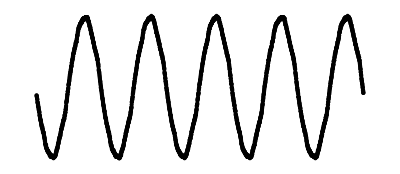

```mathematica
Graphics[Map[Point[{#[[4]] 1000,#[[5]]}]&,data][[1;;2500]]]
```